```mathematica
?ScalarMixedSpins
```

package for scalar and mixed ...
Designations(7): d t it p pp collectPP pTimes
Symbolic(9): expandSigma expandSigTimes HBasis basisH coordinates matrixTransform fullCoordinates(...) fullTransform(...) RemBasis
Traces(4): fastTr1 fastTr fastTr10 gramMatrix symGramMatrix
RhoGen(16): lastKP firstKP nextKP listKPs compoze swapToPerm generateGroup normolizeKP KPToExpr invariantKPsets squareInvariantKPsets KPsetsToExpr rhoGen invariantKPTsets listKPTs allKPs depsGen
Linerear algebra(10): RowSimplify RowReduceUpTo RowReduceUpToShow RowReduceInfo LinDeps ApplyLinDeps LinDependent LinIndependent DeleteReduced
ExplicitMatrices(13): getSi getSz getSp getSm getSx getSy KP scalar scalarSparse mixed mixedSparse explicit explicitSparse
Utilities(5):  FE foundQ firstFound printTo plusToList getInt AndRuleDelayed

```mathematica
?collectPP
```

collectPP[expr] - take expr without pp[], put d[] and t[] (and it[]) into pp[] (orderless) and collect them

```mathematica
ADR=AndRuleDelayed
```

AndRuleDelayed

### 3 spins -2.0 ->-2.0

```mathematica
τ=b0+b12 d[1,2]+b13 d[1,3]+b23 d[2,3]/.{b23->b12}
```

b0+b12 d[1,2]+b13 d[1,3]+b12 d[2,3]

```mathematica
ρ=expandSigTimes[τ,τ]
```

b0^2+6 b12^2+3 b13^2+2 b0 b12 d[1,2]-2 b12^2 d[1,2]+2 b12 b13 d[1,2]+2 b12^2 d[1,3]+2 b0 b13 d[1,3]-2 b13^2 d[1,3]+2 b0 b12 d[2,3]-2 b12^2 d[2,3]+2 b12 b13 d[2,3]

```mathematica
a0=collectPP[ρ]/.pp[__]->0/.pp[]->1;
a12=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,2]]]->0}/.pp[__]->1;
a13=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,3]]]->0}/.pp[__]->1;
```

```mathematica
a0
```

b0^2+6 b12^2+3 b13^2

```mathematica
a12
```

2 b0 b12-2 b12^2+2 b12 b13

```mathematica
a13
```

2 b12^2+2 b0 b13-2 b13^2

```mathematica
func3=6a12
```

6 (2 b0 b12-2 b12^2+2 b12 b13)

```mathematica
NMinimize[{func3/a0},{b0,b12,b13}]
```

{-4.,{b0→-1.75531,b12→1.17021,b13→-0.585104}}

### 4 spins -2.1547 -> -2.0

```mathematica
τ=b0+b12 d[1,2]+b13 d[1,3]+b14 d[1,4]+b23 d[2,3]+b24 d[2,4]+b34 d[3,4] +bb1 d[1,2]d[3,4]+bb2 d[1,3]d[2,4]+bb3 d[1,4]d[2,3]/.{b34->b12,b24->b13}
```

b0+b12 d[1,2]+b13 d[1,3]+b14 d[1,4]+b23 d[2,3]+bb3 d[1,4] d[2,3]+b13 d[2,4]+bb2 d[1,3] d[2,4]+b12 d[3,4]+bb1 d[1,2] d[3,4]

```mathematica
Sort[{b0,b12,b13,b14,b23,bb1,bb2,bb3}]
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3}

```mathematica
ρ=expandSigTimes[τ,τ]
```

b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2+2 b0 b12 d[1,2]-2 b12^2 d[1,2]+2 b13 b14 d[1,2]+2 b13 b23 d[1,2]+6 b12 bb1 d[1,2]-6 bb1^2 d[1,2]+2 b12 bb2 d[1,2]-4 bb1 bb2 d[1,2]+2 b12 bb3 d[1,2]-4 bb1 bb3 d[1,2]+4 bb2 bb3 d[1,2]+2 b0 b13 d[1,3]-2 b13^2 d[1,3]+2 b12 b14 d[1,3]+2 b12 b23 d[1,3]+2 b13 bb1 d[1,3]+6 b13 bb2 d[1,3]-4 bb1 bb2 d[1,3]-6 bb2^2 d[1,3]+2 b13 bb3 d[1,3]+4 bb1 bb3 d[1,3]-4 bb2 bb3 d[1,3]+4 b12 b13 d[1,4]+2 b0 b14 d[1,4]-2 b14^2 d[1,4]+2 b23 bb1 d[1,4]+2 b23 bb2 d[1,4]+4 bb1 bb2 d[1,4]+6 b23 bb3 d[1,4]-4 bb1 bb3 d[1,4]-4 bb2 bb3 d[1,4]-6 bb3^2 d[1,4]+4 b12 b13 d[2,3]+2 b0 b23 d[2,3]-2 b23^2 d[2,3]+2 b14 bb1 d[2,3]+2 b14 bb2 d[2,3]+4 bb1 bb2 d[2,3]+6 b14 bb3 d[2,3]-4 bb1 bb3 d[2,3]-4 bb2 bb3 d[2,3]-6 bb3^2 d[2,3]+2 b14 b23 d[1,4] d[2,3]+4 b13 bb1 d[1,4] d[2,3]-2 b14 bb1 d[1,4] d[2,3]-2 b23 bb1 d[1,4] d[2,3]+4 b12 bb2 d[1,4] d[2,3]-2 b14 bb2 d[1,4] d[2,3]-2 b23 bb2 d[1,4] d[2,3]+2 b0 bb3 d[1,4] d[2,3]-4 b14 bb3 d[1,4] d[2,3]-4 b23 bb3 d[1,4] d[2,3]+2 bb1 bb3 d[1,4] d[2,3]+2 bb2 bb3 d[1,4] d[2,3]+4 bb3^2 d[1,4] d[2,3]+2 b0 b13 d[2,4]-2 b13^2 d[2,4]+2 b12 b14 d[2,4]+2 b12 b23 d[2,4]+2 b13 bb1 d[2,4]+6 b13 bb2 d[2,4]-4 bb1 bb2 d[2,4]-6 bb2^2 d[2,4]+2 b13 bb3 d[2,4]+4 bb1 bb3 d[2,4]-4 bb2 bb3 d[2,4]+2 b13^2 d[1,3] d[2,4]-4 b13 bb1 d[1,3] d[2,4]+2 b14 bb1 d[1,3] d[2,4]+2 b23 bb1 d[1,3] d[2,4]+2 b0 bb2 d[1,3] d[2,4]-8 b13 bb2 d[1,3] d[2,4]+2 bb1 bb2 d[1,3] d[2,4]+4 bb2^2 d[1,3] d[2,4]+4 b12 bb3 d[1,3] d[2,4]-4 b13 bb3 d[1,3] d[2,4]+2 bb2 bb3 d[1,3] d[2,4]+2 b0 b12 d[3,4]-2 b12^2 d[3,4]+2 b13 b14 d[3,4]+2 b13 b23 d[3,4]+6 b12 bb1 d[3,4]-6 bb1^2 d[3,4]+2 b12 bb2 d[3,4]-4 bb1 bb2 d[3,4]+2 b12 bb3 d[3,4]-4 bb1 bb3 d[3,4]+4 bb2 bb3 d[3,4]+2 b12^2 d[1,2] d[3,4]+2 b0 bb1 d[1,2] d[3,4]-8 b12 bb1 d[1,2] d[3,4]+4 bb1^2 d[1,2] d[3,4]-4 b12 bb2 d[1,2] d[3,4]+2 b14 bb2 d[1,2] d[3,4]+2 b23 bb2 d[1,2] d[3,4]+2 bb1 bb2 d[1,2] d[3,4]-4 b12 bb3 d[1,2] d[3,4]+4 b13 bb3 d[1,2] d[3,4]+2 bb1 bb3 d[1,2] d[3,4]

```mathematica
mt=explicit[1/2,4,τ];
mr=explicit[1/2,4,ρ];
Expand[mr]===Expand[mt.mt]
```

True

```mathematica
a0=collectPP[ρ]/.pp[__]->0/.pp[]->1;
a12=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,2]]]->0}/.pp[__]->1;
a13=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,3]]]->0}/.pp[__]->1;
a14=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,4]]]->0}/.pp[__]->1;
a23=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[2,3]]]->0}/.pp[__]->1;
a24=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[2,4]]]->0}/.pp[__]->1;
a34=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[3,4]]]->0}/.pp[__]->1;
a1=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,2],d[3,4]]],0]/.pp[__]->1;
a2=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,3],d[2,4]]],0]/.pp[__]->1;
a3=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,4],d[2,3]]],0]/.pp[__]->1;
```

```mathematica
a34=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[3,4]]]->0}/.pp[__]->1;
```

```mathematica
a12-a34
```

0

```mathematica
H=d[1,2]+d[2,3]+d[3,4]
```

d[1,2]+d[2,3]+d[3,4]

```mathematica
a0
```

b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2

```mathematica
ρ//collectPP
```

(b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2) pp[]+(2 b0 b12-2 b12^2+2 b13 b14+2 b13 b23+6 b12 bb1-6 bb1^2+2 b12 bb2-4 bb1 bb2+2 b12 bb3-4 bb1 bb3+4 bb2 bb3) pp[d[1,2]]+(2 b0 b13-2 b13^2+2 b12 b14+2 b12 b23+2 b13 bb1+6 b13 bb2-4 bb1 bb2-6 bb2^2+2 b13 bb3+4 bb1 bb3-4 bb2 bb3) pp[d[1,3]]+(4 b12 b13+2 b0 b14-2 b14^2+2 b23 bb1+2 b23 bb2+4 bb1 bb2+6 b23 bb3-4 bb1 bb3-4 bb2 bb3-6 bb3^2) pp[d[1,4]]+(4 b12 b13+2 b0 b23-2 b23^2+2 b14 bb1+2 b14 bb2+4 bb1 bb2+6 b14 bb3-4 bb1 bb3-4 bb2 bb3-6 bb3^2) pp[d[2,3]]+(2 b0 b13-2 b13^2+2 b12 b14+2 b12 b23+2 b13 bb1+6 b13 bb2-4 bb1 bb2-6 bb2^2+2 b13 bb3+4 bb1 bb3-4 bb2 bb3) pp[d[2,4]]+(2 b0 b12-2 b12^2+2 b13 b14+2 b13 b23+6 b12 bb1-6 bb1^2+2 b12 bb2-4 bb1 bb2+2 b12 bb3-4 bb1 bb3+4 bb2 bb3) pp[d[3,4]]+(2 b12^2+2 b0 bb1-8 b12 bb1+4 bb1^2-4 b12 bb2+2 b14 bb2+2 b23 bb2+2 bb1 bb2-4 b12 bb3+4 b13 bb3+2 bb1 bb3) pp[d[1,2],d[3,4]]+(2 b13^2-4 b13 bb1+2 b14 bb1+2 b23 bb1+2 b0 bb2-8 b13 bb2+2 bb1 bb2+4 bb2^2+4 b12 bb3-4 b13 bb3+2 bb2 bb3) pp[d[1,3],d[2,4]]+(2 b14 b23+4 b13 bb1-2 b14 bb1-2 b23 bb1+4 b12 bb2-2 b14 bb2-2 b23 bb2+2 b0 bb3-4 b14 bb3-4 b23 bb3+2 bb1 bb3+2 bb2 bb3+4 bb3^2) pp[d[1,4],d[2,3]]

```mathematica
fastTr[H,ρ](* !!!! error, need to debug *)
```

0

```mathematica
func=collectPP[expandSigTimes[H,ρ]]/.ADR[pp[___],Except[pp[]],0]/.pp[___]->1
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

12 b0 b12-12 b12^2+12 b12 b13+12 b13 b14+6 b0 b23+12 b13 b23-6 b23^2+36 b12 bb1+6 b14 bb1-36 bb1^2+12 b12 bb2+6 b14 bb2-12 bb1 bb2+12 b12 bb3+18 b14 bb3-36 bb1 bb3+12 bb2 bb3-18 bb3^2

```mathematica
mH=explicit[1/2,4,H];
mr=explicit[1/2,4,ρ];
mHr=explicit[1/2,4,expandSigTimes[H,ρ]];
Expand[mHr]===Expand[mH.mr]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

True

```mathematica
Clear[m1];
NN=8;
mm1=Table[Subscript[m1, i,j],{i,1,NN},{j,1,NN}];
Do[If[j<i,mm1[[i,j]]=Subscript[m1, j,i]],{i,1,NN},{j,1,NN}];
mm1//TableForm
```

m1_(1,1) | m1_(1,2) | m1_(1,3) | m1_(1,4) | m1_(1,5) | m1_(1,6) | m1_(1,7) | m1_(1,8)
m1_(1,2) | m1_(2,2) | m1_(2,3) | m1_(2,4) | m1_(2,5) | m1_(2,6) | m1_(2,7) | m1_(2,8)
m1_(1,3) | m1_(2,3) | m1_(3,3) | m1_(3,4) | m1_(3,5) | m1_(3,6) | m1_(3,7) | m1_(3,8)
m1_(1,4) | m1_(2,4) | m1_(3,4) | m1_(4,4) | m1_(4,5) | m1_(4,6) | m1_(4,7) | m1_(4,8)
m1_(1,5) | m1_(2,5) | m1_(3,5) | m1_(4,5) | m1_(5,5) | m1_(5,6) | m1_(5,7) | m1_(5,8)
m1_(1,6) | m1_(2,6) | m1_(3,6) | m1_(4,6) | m1_(5,6) | m1_(6,6) | m1_(6,7) | m1_(6,8)
m1_(1,7) | m1_(2,7) | m1_(3,7) | m1_(4,7) | m1_(5,7) | m1_(6,7) | m1_(7,7) | m1_(7,8)
m1_(1,8) | m1_(2,8) | m1_(3,8) | m1_(4,8) | m1_(5,8) | m1_(6,8) | m1_(7,8) | m1_(8,8)

```mathematica
bbb={b0,b12,b13,b14,b23,bb1,bb2,bb3}
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3}

```mathematica
(FF=mm1/.SolveAlways[func==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(0 | 6 | 0 | 0 | 3 | 0 | 0 | 0
6 | -12 | 6 | 0 | 0 | 18 | 6 | 6
0 | 6 | 0 | 6 | 6 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 3 | 3 | 9
3 | 0 | 6 | 0 | -6 | 0 | 0 | 0
0 | 18 | 0 | 3 | 0 | -36 | -6 | -18
0 | 6 | 0 | 3 | 0 | -6 | 0 | 6
0 | 6 | 0 | 9 | 0 | -18 | 6 | -18)

```mathematica
(NO=mm1/.SolveAlways[a0==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 9 | 3 | 3
0 | 0 | 0 | 0 | 0 | 3 | 9 | 3
0 | 0 | 0 | 0 | 0 | 3 | 3 | 9)

```mathematica
(CC=mm1/.SolveAlways[(a12-a23)==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
1 | -2 | -2 | 0 | 0 | 3 | 1 | 1
0 | -2 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | -1 | -3
-1 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 3 | 0 | -1 | 0 | -6 | -4 | 0
0 | 1 | 0 | -1 | 0 | -4 | 0 | 4
0 | 1 | 0 | -3 | 0 | 0 | 4 | 6)

```mathematica
Eigensystem[m123//N]
```

{{-9.64746,9.32858,3.12444,-3.12252,1.63186,-1.31489,8.88178×10^-15,1.2837×10^-16},{{-0.0419068,0.392554,0.094839,-0.118108,-0.0117404,-0.805666,-0.410716,0.057261},{0.0121328,0.103776,-0.0567969,-0.312877,-0.00940561,-0.0723079,0.433146,0.833687},{-0.328289,-0.316681,0.468984,0.122912,0.70904,-0.179806,0.141919,0.0409464},{0.227202,-0.567076,-0.502089,0.291263,0.142369,-0.182223,-0.367037,0.318883},{0.109795,-0.383481,0.316928,0.312873,-0.562651,-0.401706,0.400613,-0.0641816},{0.369629,-0.352083,-0.0743666,-0.740322,0.13394,-0.189653,0.143154,-0.333771},{0.221349,-0.199215,0.619779,-0.199215,-0.199215,0.287754,-0.531239,0.287754},{0.800641,0.320256,0.160128,0.320256,0.320256,-3.27172×10^-18,0.160128,0.}}}

```mathematica
NMinimize[func/a0,bbb]
```

{-6.4641,{b0→-3.9743,b12→3.61933,b13→-0.969795,b14→1.32477,b23→1.32477,bb1→-3.61933,bb2→0.969795,bb3→-1.32477}}

```mathematica
-6.464101615137753/3
```

-2.1547

```mathematica
NMinimize[{func/a0,a12==a23},bbb]
```

{-6.,{b0→1.72662,b12→-1.1511,b13→0.575551,b14→-1.15112,b23→-1.15107,bb1→1.15112,bb2→-0.575561,bb3→1.15112}}

```mathematica
Urs=((FF+λ0 NO+λ1 CC).bbb)~FE~(#==0&);
AppendTo[Urs,bbb.NO.bbb==1];
AppendTo[Urs,bbb.CC.bbb==0];
Urs//TableForm
```

b0 λ0+b23 (3-λ1)+b12 (6+λ1)==0
b13 (6-2 λ1)+b12 (-12+6 λ0-2 λ1)+b0 (6+λ1)+bb2 (6+λ1)+bb3 (6+λ1)+bb1 (18+3 λ1)==0
6 b13 λ0+b12 (6-2 λ1)+b14 (6+λ1)+b23 (6+λ1)==0
3 b14 λ0+bb3 (9-3 λ1)+bb1 (3-λ1)+bb2 (3-λ1)+b13 (6+λ1)==0
b0 (3-λ1)+b13 (6+λ1)+b23 (-6+3 λ0+2 λ1)==0
bb3 (-18+3 λ0)+bb1 (-36+9 λ0-6 λ1)+bb2 (-6+3 λ0-4 λ1)+b14 (3-λ1)+b12 (18+3 λ1)==0
9 bb2 λ0+bb1 (-6+3 λ0-4 λ1)+b14 (3-λ1)+b12 (6+λ1)+bb3 (6+3 λ0+4 λ1)==0
bb1 (-18+3 λ0)+b14 (9-3 λ1)+b12 (6+λ1)+bb2 (6+3 λ0+4 λ1)+bb3 (-18+9 λ0+6 λ1)==0
b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+bb1 (9 bb1+3 bb2+3 bb3)+bb2 (3 bb1+9 bb2+3 bb3)+bb3 (3 bb1+3 bb2+9 bb3)==1
b0 (b12-b23)+b13 (-2 b12+b14+b23)+b23 (-b0+b13+2 b23)+bb1 (3 b12-b14-6 bb1-4 bb2)+b14 (b13-bb1-bb2-3 bb3)+b12 (b0-2 b12-2 b13+3 bb1+bb2+bb3)+bb2 (b12-b14-4 bb1+4 bb3)+bb3 (b12-3 b14+4 bb2+6 bb3)==0

```mathematica
vars=bbb;
AppendTo[vars,λ0];
AppendTo[vars,λ1];
vars
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3,λ0,λ1}

```mathematica
ares=Solve[Urs,vars];
```

$Aborted

```mathematica
res=NSolve[Urs,vars];
```

```mathematica
res//Length
```

57

```mathematica
(res2=Table[{Re[func/.res[[i]]],Im[func/.res[[i]]]//Abs},{i,1,Length[res]}]//SortBy[First])//TableForm
```

-6. | 0
-3. | 1.49277×10^-7
-3. | 3.05991×10^-9
-3. | 6.50426×10^-10
-3. | 2.15771×10^-16
-3. | 2.30107×10^-10
-3. | 2.22495×10^-10
-3. | 1.32378×10^-11
-3. | 3.0328×10^-11
-3. | 4.91268×10^-12
-3. | 5.69322×10^-13
-3. | 4.99228×10^-12
-3. | 3.19326×10^-11
-3. | 1.00646×10^-10
-3. | 8.99963×10^-11
-3. | 2.40054×10^-16
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1. | 0
-1. | 0
-1. | 0
-1. | 0
-1.49543×10^-12 | 5.65258×10^-14
-5.8987×10^-13 | 6.40738×10^-14
1.84119×10^-13 | 1.68067×10^-13
2.08734×10^-13 | 8.36352×10^-13
3.2511×10^-13 | 5.08059×10^-13
5.30844×10^-13 | 1.05691×10^-12
1.8 | 0
1.8 | 0
3. | 5.12766×10^-8
3. | 5.33459×10^-10
3. | 2.25965×10^-10
3. | 7.65128×10^-11
3. | 4.79191×10^-11
3. | 2.61899×10^-15
3. | 2.222×10^-15
3. | 2.46146×10^-15
3. | 2.24742×10^-15
3. | 1.70391×10^-15
3. | 2.15337×10^-15
3. | 1.38784×10^-10
3. | 1.5485×10^-10
3. | 1.49019×10^-15
3. | 2.25463×10^-15
3. | 1.61495×10^-11
3. | 5.94127×10^-11
3. | 1.41303×10^-10
3. | 4.07235×10^-7
3. | 9.92267×10^-7
3.00001 | 2.26697×10^-6

### 5 spins -1.92789 -> -1.86852

```mathematica
groupl5=generateGroup[{{1->5,2->4,3->3,4->2,5->1}}]//Keys
```

{{1→5,2→4,3→3,4→2,5→1},{1→1,2→2,3→3,4→4,5→5}}

```mathematica
basisl5={1};
AppendTo[basisl5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,5,groupl5]];
AppendTo[basisl5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,5,groupl5]];
(basisl5=basisl5//Flatten)//TableForm;
{Table[i,{i,1,Length[basisl5]}],basisl5}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[4,5]
3 | d[1,3]+d[3,5]
4 | d[1,4]+d[2,5]
5 | d[1,5]
6 | d[2,3]+d[3,4]
7 | d[2,4]
8 | d[1,3] d[2,4]+d[2,4] d[3,5]
9 | d[1,3] d[2,5]+d[1,4] d[3,5]
10 | d[1,4] d[2,3]+d[2,5] d[3,4]
11 | d[1,4] d[2,5]
12 | d[1,5] d[2,3]+d[1,5] d[3,4]
13 | d[1,5] d[2,4]
14 | d[1,2] d[3,4]+d[2,3] d[4,5]
15 | d[1,2] d[3,5]+d[1,3] d[4,5]
16 | d[1,2] d[4,5]

```mathematica
cluster5={{1,2,3,4,5}}
```

{{1,2,3,4,5}}

```mathematica
basis5var={1};
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster5]];
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster5]];
basis5var=basis5var//Flatten;
{Table[i,{i,1,Length[basis5var]}],basis5var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]
3 | d[1,3]+d[2,4]+d[3,5]
4 | d[1,4]+d[2,5]
5 | d[1,5]
6 | d[1,3] d[2,4]+d[2,4] d[3,5]
7 | d[1,3] d[2,5]+d[1,4] d[3,5]
8 | d[1,4] d[2,3]+d[2,5] d[3,4]
9 | d[1,4] d[2,5]
10 | d[1,5] d[2,3]+d[1,5] d[3,4]
11 | d[1,5] d[2,4]
12 | d[1,2] d[3,4]+d[2,3] d[4,5]
13 | d[1,2] d[3,5]+d[1,3] d[4,5]
14 | d[1,2] d[4,5]

```mathematica
Clear[b5]
```

```mathematica
bb5={b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15}(*Table[Subscript[b, i],{i,0,15}]*)
```

{b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15}

```mathematica
τ5=basisl5.bb5//Expand
```

b0+b1 d[1,2]+b2 d[1,3]+b3 d[1,4]+b4 d[1,5]+b5 d[2,3]+b9 d[1,4] d[2,3]+b11 d[1,5] d[2,3]+b6 d[2,4]+b7 d[1,3] d[2,4]+b12 d[1,5] d[2,4]+b3 d[2,5]+b8 d[1,3] d[2,5]+b10 d[1,4] d[2,5]+b5 d[3,4]+b13 d[1,2] d[3,4]+b11 d[1,5] d[3,4]+b9 d[2,5] d[3,4]+b2 d[3,5]+b14 d[1,2] d[3,5]+b8 d[1,4] d[3,5]+b7 d[2,4] d[3,5]+b1 d[4,5]+b15 d[1,2] d[4,5]+b14 d[1,3] d[4,5]+b13 d[2,3] d[4,5]

```mathematica
Hl5=basisl5[[2]]+basisl5[[6]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]

```mathematica
ρ5=expandSigTimes[τ5,τ5]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

b0^2+6 b1^2+9 b10^2+18 b11^2+6 b10 b12+9 b12^2+18 b13^2+12 b11 b14+18 b14^2+6 b10 b15+6 b12 b15+9 b15^2+1248+ⅈ b14 b9 d[1,5] t[2,3,4]-ⅈ b15 b9 d[1,5] t[2,3,4]+ⅈ b10 b7 d[1,4] t[2,3,5]+ⅈ b13 b7 d[1,4] t[2,3,5]-ⅈ b13 b8 d[1,4] t[2,3,5]+ⅈ b11 b9 d[1,4] t[2,3,5]-ⅈ b12 b9 d[1,4] t[2,3,5]-ⅈ b7 b9 d[1,4] t[2,3,5]-ⅈ b11 b7 d[1,3] t[2,4,5]+ⅈ b8 b9 d[1,3] t[2,4,5]
 |  |  |  |

```mathematica
mt=explicit[1/2,5,τ5];
mr=explicit[1/2,5,ρ5];
Expand[mr]===Expand[mt.mt]
```

True

```mathematica
fastTr[Hl5,ρ5](* !!!! error, need to debug *)
```

0

```mathematica
func5=collectPP[expandSigTimes[Hl5,ρ5]]/.ADR[pp[___],Except[pp[]],0]/.pp[___]->1
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

12 b0 b1-12 b1^2+12 b1 b10+12 b10 b11-36 b11^2+12 b1 b12+24 b10 b12+36 b11 b12+36 b1 b13+12 b11 b13-72 b13^2+12 b10 b14-48 b11 b14+12 b12 b14+36 b13 b14-36 b14^2+36 b1 b15-24 b10 b15+12 b11 b15-24 b12 b15+36 b14 b15-36 b15^2+12 b1 b2+12 b11 b2+36 b14 b2+12 b13 b3+12 b2 b3+36 b11 b4+12 b14 b4+12 b3 b4+12 b0 b5+36 b13 b5+12 b2 b5-12 b5^2+12 b3 b6+12 b5 b6+12 b1 b7+12 b11 b7-24 b13 b7+12 b14 b7+12 b3 b7+12 b5 b7+36 b10 b8+12 b12 b8+12 b13 b8+12 b15 b8+12 b2 b8+12 b4 b8+36 b7 b8+12 b1 b9+36 b11 b9-72 b13 b9+12 b14 b9+36 b3 b9+12 b5 b9+24 b7 b9+12 b8 b9-36 b9^2

```mathematica
mH=explicit[1/2,5,Hl5];
mr=explicit[1/2,5,ρ5];
mHr=explicit[1/2,5,expandSigTimes[Hl5,ρ5]];
Expand[mHr]===Expand[mH.mr]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

True

```mathematica
basisl5s=basisl5~FE~((#//plusToList//First//collectPP)&);
(a5=Table[collectPP[ρ5]/.ADR[pp[___],Except[basisl5s[[i]]],0]/.pp[___]->1,{i,1,16}])//TableForm
```

b0^2+6 b1^2+9 b10^2+18 b11^2+6 b10 b12+9 b12^2+18 b13^2+12 b11 b14+18 b14^2+6 b10 b15+6 b12 b15+9 b15^2+6 b2^2+6 b3^2+3 b4^2+6 b5^2+3 b6^2+12 b13 b7+18 b7^2+12 b11 b8+12 b14 b8+18 b8^2+12 b13 b9+12 b7 b9+18 b9^2
2 b0 b1-2 b1^2+2 b1 b10+2 b1 b12+4 b10 b12+2 b11 b13-6 b13^2-4 b11 b14+6 b13 b14-6 b14^2+6 b1 b15-4 b10 b15-4 b12 b15-6 b15^2+2 b11 b2+6 b14 b2+2 b3 b4+6 b13 b5+2 b2 b5+2 b3 b6+2 b11 b7-4 b13 b7+2 b14 b7+2 b5 b7+4 b11 b8+2 b13 b8-4 b14 b8+2 b2 b8+6 b7 b8+6 b11 b9-4 b13 b9+2 b14 b9+2 b5 b9+4 b7 b9+2 b8 b9
2 b1 b11+2 b10 b13+2 b12 b13+6 b1 b14-6 b14^2+6 b13 b15+2 b0 b2-2 b2^2+2 b11 b3+2 b14 b3+2 b2 b4+2 b1 b5+2 b3 b5+2 b13 b6+2 b10 b7+6 b12 b7-4 b13 b7+2 b15 b7+6 b6 b7-6 b7^2+2 b1 b8-8 b14 b8+6 b3 b8-6 b8^2+6 b10 b9+2 b12 b9+4 b13 b9+2 b15 b9+2 b6 b9-4 b7 b9
-6 b10^2-4 b10 b12+6 b11 b13+4 b11 b14+2 b13 b14-4 b10 b15+4 b12 b15+2 b11 b2+2 b14 b2+2 b0 b3+6 b10 b3+2 b12 b3+2 b15 b3-2 b3^2+2 b1 b4+2 b13 b5+2 b2 b5+2 b1 b6+2 b11 b7+4 b13 b7+6 b14 b7+2 b5 b7-4 b11 b8+2 b13 b8-4 b14 b8+6 b2 b8+2 b7 b8-6 b8^2+2 b11 b9-4 b13 b9+2 b14 b9+6 b5 b9-4 b7 b9+6 b8 b9-6 b9^2
-12 b11^2-4 b10 b12-6 b12^2+2 b13^2-8 b11 b14+4 b10 b15-4 b12 b15+2 b2^2+4 b1 b3+2 b0 b4-2 b4^2+12 b11 b5+4 b14 b5+2 b10 b6+6 b12 b6+2 b15 b6+4 b13 b7+6 b7^2-8 b11 b8+8 b14 b8+4 b5 b8+12 b13 b9+4 b7 b9+2 b9^2
2 b10 b11-6 b11^2+6 b11 b12+6 b1 b13-6 b13^2+2 b10 b14-4 b11 b14+2 b12 b14+2 b11 b15+6 b14 b15+2 b1 b2+2 b13 b3+2 b2 b3+6 b11 b4+2 b14 b4+2 b0 b5-2 b5^2+2 b5 b6+2 b1 b7+2 b3 b7+6 b10 b8-4 b11 b8+2 b12 b8+4 b14 b8+2 b15 b8+2 b4 b8+2 b1 b9-8 b13 b9+6 b3 b9-6 b9^2
6 b11^2-4 b10 b12-6 b12^2+4 b11 b14+2 b14^2+4 b10 b15-4 b12 b15+4 b13 b2+4 b1 b3+2 b10 b4+6 b12 b4+2 b15 b4+2 b5^2+2 b0 b6-2 b6^2-8 b13 b7+12 b2 b7-12 b7^2+4 b11 b8+12 b14 b8+2 b8^2+8 b13 b9+4 b2 b9-8 b7 b9
2 b10 b13+2 b11 b13-2 b12 b13+2 b10 b14+2 b13 b14-2 b14^2+2 b12 b2-2 b13 b2+2 b13 b3+2 b14 b3+2 b13 b5-2 b13 b6+2 b2 b6+2 b0 b7-2 b10 b7-4 b12 b7+2 b13 b7-2 b15 b7-4 b2 b7+2 b4 b7-4 b6 b7+4 b7^2+2 b1 b8-2 b13 b8-4 b14 b8+2 b15 b8-2 b8^2+2 b1 b9+2 b11 b9-2 b12 b9-2 b14 b9+2 b15 b9-2 b2 b9+2 b5 b9-2 b6 b9+2 b7 b9+2 b8 b9
2 b1 b11-2 b10 b13-2 b11 b13+4 b12 b13+2 b13^2-2 b13 b14+2 b11 b15-2 b14 b2-2 b11 b3-2 b14 b3+2 b2 b3+2 b14 b4+2 b10 b5+2 b14 b5+2 b14 b6+2 b1 b7-2 b10 b7-2 b13 b7-4 b14 b7+2 b15 b7+2 b0 b8+2 b11 b8+2 b12 b8+4 b13 b8+2 b14 b8-2 b15 b8-4 b2 b8-4 b3 b8-2 b7 b8+4 b8^2-4 b10 b9+2 b11 b9-4 b12 b9-2 b14 b9+2 b3 b9+2 b7 b9
2 b1 b11-2 b10 b11-4 b11 b13-2 b10 b14-2 b11 b14+4 b12 b14-2 b13 b14+2 b14^2+2 b11 b15+2 b10 b2+2 b13 b2-2 b13 b3+2 b13 b4-2 b13 b5+2 b3 b5+2 b13 b6+2 b1 b7-2 b14 b7+2 b15 b7-2 b3 b7-4 b10 b8+2 b11 b8-4 b12 b8-2 b13 b8+2 b3 b8+2 b7 b8+2 b0 b9-2 b11 b9+2 b12 b9+2 b13 b9+4 b14 b9-2 b15 b9-4 b3 b9-4 b5 b9+2 b7 b9+4 b9^2
2 b0 b10+4 b10^2+4 b1 b12+2 b10 b12+4 b11 b13-2 b13^2+4 b11 b14+4 b13 b14-2 b14^2+2 b10 b15-8 b10 b3-4 b12 b3-4 b15 b3+2 b3^2+2 b15 b4+2 b15 b6+4 b13 b7+4 b14 b7-4 b13 b8+4 b5 b8-4 b7 b8-4 b11 b9-4 b14 b9+4 b2 b9-8 b8 b9
2 b0 b11-2 b10 b11+4 b11^2-4 b11 b12+2 b10 b13-2 b13^2+2 b10 b14+2 b11 b14-2 b12 b14+2 b13 b14-2 b11 b15+2 b14 b2+2 b13 b3+2 b14 b3-4 b11 b4-2 b14 b4-4 b11 b5+2 b12 b5-2 b14 b5+2 b4 b5+2 b11 b6+2 b14 b7+2 b1 b8+2 b11 b8-2 b12 b8-2 b13 b8+2 b15 b8+2 b2 b8-2 b4 b8-2 b5 b8+2 b7 b8+2 b1 b9-4 b13 b9-2 b14 b9+2 b15 b9+2 b8 b9-2 b9^2
4 b1 b10-4 b11^2+2 b0 b12+2 b10 b12+4 b12^2+2 b13^2-4 b11 b14-4 b13 b14+2 b14^2+2 b12 b15+4 b15 b3-2 b10 b4-4 b12 b4-2 b15 b4+4 b11 b5-2 b10 b6-4 b12 b6-2 b15 b6+2 b4 b6-4 b13 b7+4 b2 b7-4 b7^2-4 b11 b8+8 b13 b8+2 b8^2+8 b14 b9-4 b7 b9-4 b8 b9+2 b9^2
2 b10 b11+2 b0 b13-4 b1 b13-2 b10 b13-2 b11 b13+2 b12 b13+4 b13^2+2 b1 b14+2 b11 b14-4 b12 b14-2 b11 b15-4 b14 b15+2 b15 b2+2 b11 b3+2 b1 b5-4 b13 b5-2 b1 b7+2 b10 b7+2 b13 b7+2 b14 b7+2 b3 b7-2 b11 b8+4 b12 b8+4 b13 b8-2 b15 b8-2 b7 b8+2 b8^2-2 b1 b9-4 b11 b9+2 b13 b9-2 b14 b9+2 b2 b9+2 b4 b9-2 b5 b9+2 b6 b9-2 b8 b9
-2 b1 b11+2 b10 b11+2 b1 b13+2 b11 b13-4 b12 b13+2 b0 b14-4 b1 b14-2 b10 b14+2 b11 b14+2 b12 b14+4 b14^2-4 b13 b15+2 b1 b2-4 b14 b2+2 b11 b3+2 b15 b5+2 b10 b7+2 b13 b7-2 b14 b7-2 b15 b7+2 b3 b7-2 b1 b8-2 b13 b8+2 b14 b8-2 b2 b8+2 b4 b8+2 b5 b8+2 b6 b8-4 b7 b8-2 b11 b9+4 b12 b9+4 b14 b9-2 b15 b9-2 b7 b9-2 b8 b9+2 b9^2
2 b1^2-4 b1 b10-4 b1 b12-4 b11 b13-8 b13 b14+2 b0 b15-8 b1 b15+2 b10 b15+2 b12 b15+4 b15^2+4 b13 b2+4 b12 b3+2 b10 b4+4 b14 b5+2 b10 b6-4 b14 b7+4 b11 b8-4 b13 b8+4 b7 b8-2 b8^2+4 b11 b9-4 b14 b9+4 b7 b9+4 b8 b9-2 b9^2

```mathematica
(FF5=CoefficientArrays[func5,bb5,"Symmetric"->True]//Last//Normal)//MatrixForm
```

(0 | 6 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | -12 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 6 | 0 | 6 | 18 | 0 | 18
0 | 6 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 18 | 0
0 | 0 | 6 | 0 | 6 | 0 | 6 | 6 | 0 | 18 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 0 | 6 | 0
6 | 0 | 6 | 0 | 0 | -12 | 6 | 6 | 0 | 6 | 0 | 0 | 0 | 18 | 0 | 0
0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 6 | 0 | 6 | 0 | 0 | 18 | 12 | 0 | 6 | 0 | -12 | 6 | 0
0 | 0 | 6 | 0 | 6 | 0 | 0 | 18 | 0 | 6 | 18 | 0 | 6 | 6 | 0 | 6
0 | 6 | 0 | 18 | 0 | 6 | 0 | 12 | 6 | -36 | 0 | 18 | 0 | -36 | 6 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 6 | 12 | 0 | 6 | -12
0 | 0 | 6 | 0 | 18 | 0 | 0 | 6 | 0 | 18 | 6 | -36 | 18 | 6 | -24 | 6
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 12 | 18 | 0 | 0 | 6 | -12
0 | 18 | 0 | 6 | 0 | 18 | 0 | -12 | 6 | -36 | 0 | 6 | 0 | -72 | 18 | 0
0 | 0 | 18 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 6 | -24 | 6 | 18 | -36 | 18
0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | -12 | 6 | -12 | 0 | 18 | -36)

```mathematica
a5m=Table[CoefficientArrays[a5[[i]],bb5,"Symmetric"->True]//Last//Normal,{i,1,16}];
```

```mathematica
a5m[[14]]-a5m[[8]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | -2 | 0 | 0 | 0 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 2 | 0 | 0 | -1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | -3 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0
-1 | -1 | 2 | 1 | -1 | 0 | 2 | -4 | -1 | -1 | 2 | 0 | 2 | 0 | 1 | 1
0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 4 | -2 | 0 | -1 | 2 | 3 | 2 | -2
0 | -2 | 2 | 0 | 1 | -2 | 2 | -1 | -2 | 0 | 0 | -3 | 1 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -2 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -3 | 1 | 0 | 0 | -2 | 1 | -1
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 0 | 0 | 0 | 2 | -2 | 0
1 | -2 | 1 | -1 | 0 | -3 | 1 | 0 | 3 | 1 | -2 | -2 | 2 | 4 | -1 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 2 | 0 | -1 | 1 | -2 | -1 | 2 | -2
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -2 | -1 | 0 | -1 | 0 | 0 | -2 | 0)

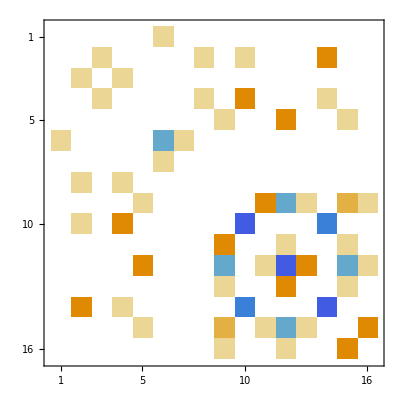

```mathematica
3a5m[[6]]//MatrixPlot
```

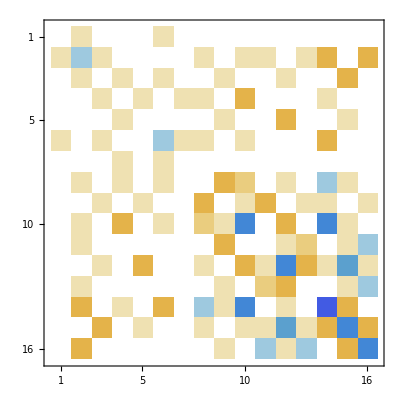

```mathematica
FF5-3 a5m[[2]]-3 a5m[[6]]//MatrixPlot
```

```mathematica
cluster5={{1,2,3,4,5}}
```

{{1,2,3,4,5}}

```mathematica
NMinimize[{func5/a5[[1]]},bb5]
```

{-7.71155,{b0→3.58717,b1→-2.77501,b2→1.05631,b3→-0.687325,b4→0.654281,b5→-1.83543,b6→0.654281,b7→-0.389561,b8→0.229108,b9→0.550013,b10→-0.0917971,b11→-0.389561,b12→0.124841,b13→1.67498,b14→-0.895859,b15→1.99589}}

```mathematica
-7.711545013271962/4
```

-1.92789

```mathematica
NMinimize[{func5/a5[[1]],a5[[2]]==a5[[6]]&&a5[[3]]==a5[[7]]},bb5]
```

{-7.47407,{b0→-0.296144,b1→0.18449,b2→-0.0821319,b3→0.0915366,b4→-0.082132,b5→0.184491,b6→-0.0822197,b7→0.0511467,b8→-0.0201828,b9→-0.0821533,b10→0.010803,b11→0.0511686,b12→-0.0202054,b13→-0.153506,b14→0.0511681,b15→-0.082155}}

```mathematica
-7.474068184959573/4
```

-1.86852

```mathematica
basisl5//TableForm
```

1
d[1,2]+d[4,5]
d[1,3]+d[3,5]
d[1,4]+d[2,5]
d[1,5]
d[2,3]+d[3,4]
d[2,4]
d[1,3] d[2,4]+d[2,4] d[3,5]
d[1,3] d[2,5]+d[1,4] d[3,5]
d[1,4] d[2,3]+d[2,5] d[3,4]
d[1,4] d[2,5]
d[1,5] d[2,3]+d[1,5] d[3,4]
d[1,5] d[2,4]
d[1,2] d[3,4]+d[2,3] d[4,5]
d[1,2] d[3,5]+d[1,3] d[4,5]
d[1,2] d[4,5]

```mathematica
basis5var={1};
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster5]];
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster5]];
(basis5var=basis5var//Flatten)//TableForm
```

1
d[1,2]+d[2,3]+d[3,4]+d[4,5]
d[1,3]+d[2,4]+d[3,5]
d[1,4]+d[2,5]
d[1,5]
d[1,3] d[2,4]+d[2,4] d[3,5]
d[1,3] d[2,5]+d[1,4] d[3,5]
d[1,4] d[2,3]+d[2,5] d[3,4]
d[1,4] d[2,5]
d[1,5] d[2,3]+d[1,5] d[3,4]
d[1,5] d[2,4]
d[1,2] d[3,4]+d[2,3] d[4,5]
d[1,2] d[3,5]+d[1,3] d[4,5]
d[1,2] d[4,5]

```mathematica
Urs5=((FF5+λ0 a5m[[1]]+λ1(a5m[[2]]-a5m[[6]])+λ2(a5m[[3]]-a5m[[7]])).bb5)~FE~(#==0&);
AppendTo[Urs5,bb5.a5m[[1]].bb5==1];
AppendTo[Urs5,bb5.(a5m[[2]]-a5m[[6]]).bb5==0];
AppendTo[Urs5,bb5.(a5m[[3]]-a5m[[7]]).bb5==0];
Urs5//TableForm
```

b0 λ0+b5 (6-λ1)+b1 (6+λ1)+b2 λ2-b6 λ2==0
b13 (18-3 λ1)+b1 (-12+6 λ0-2 λ1)+b2 (6-λ1)+b7 (6-λ1)+b9 (6-λ1)+b0 (6+λ1)+b10 (6+λ1)+b12 (6+λ1)+b15 (18+3 λ1)+b11 λ2+3 b14 λ2-2 b3 λ2+b5 λ2+b8 λ2==0
b1 (6-λ1)+b3 (6-λ1)+b11 (6+λ1)+b5 (6+λ1)+b8 (6+λ1)+b14 (18+3 λ1)+b2 (6 λ0-2 λ2)+b0 λ2-2 b13 λ2+b4 λ2-6 b7 λ2-2 b9 λ2==0
6 b3 λ0+b9 (18-3 λ1)+b13 (6-λ1)+b2 (6-λ1)+b7 (6-λ1)+b4 (6+λ1)+b6 (6+λ1)-2 b1 λ2+b11 λ2+b14 λ2+b5 λ2+3 b8 λ2==0
3 b4 λ0+b11 (18-3 λ1)+b14 (6-λ1)+b8 (6-λ1)+b3 (6+λ1)-b10 λ2-3 b12 λ2-b15 λ2+b2 λ2==0
b0 (6-λ1)+b6 (6-λ1)+b2 (6+λ1)+b7 (6+λ1)+b9 (6+λ1)+b13 (18+3 λ1)+b5 (-12+6 λ0+2 λ1-2 λ2)+b1 λ2+b3 λ2==0
b5 (6-λ1)+b3 (6+λ1)-b0 λ2+b13 λ2+3 b7 λ2+b9 λ2+b6 (3 λ0+2 λ2)==0
b1 (6-λ1)+b3 (6-λ1)+b11 (6+λ1)+b14 (6+λ1)+b5 (6+λ1)+b8 (18+3 λ1)+b10 λ2+3 b12 λ2+b15 λ2-6 b2 λ2+3 b6 λ2+b13 (-12+6 λ0-2 λ1+2 λ2)+b9 (12+6 λ0+2 λ1+2 λ2)+b7 (18 λ0+6 λ2)==0
b10 (18-3 λ1)+b12 (6-λ1)+b15 (6-λ1)+b4 (6-λ1)+b13 (6+λ1)+b2 (6+λ1)+b9 (6+λ1)+b7 (18+3 λ1)+b14 (6 λ0-4 λ1-10 λ2)+b8 (18 λ0-8 λ2)+b11 (6 λ0+4 λ1-2 λ2)+b1 λ2+3 b3 λ2==0
b3 (18-3 λ1)+b1 (6-λ1)+b14 (6+λ1)+b5 (6+λ1)+b8 (6+λ1)+b11 (18+3 λ1)+b9 (-36+18 λ0+6 λ1)+b13 (-36+6 λ0+2 λ1-2 λ2)+3 b10 λ2+b12 λ2+b15 λ2-2 b2 λ2+b6 λ2+b7 (12+6 λ0+2 λ1+2 λ2)==0
9 b10 λ0+b8 (18-3 λ1)+b11 (6-λ1)+b14 (6-λ1)+b1 (6+λ1)+b15 (-12+3 λ0-2 λ1-2 λ2)+b13 λ2-b4 λ2+b7 λ2+3 b9 λ2+b12 (12+3 λ0+2 λ1+2 λ2)==0
b12 (18-3 λ1)+b4 (18-3 λ1)+b10 (6-λ1)+b15 (6-λ1)+b13 (6+λ1)+b2 (6+λ1)+b7 (6+λ1)+b9 (18+3 λ1)+b11 (-36+18 λ0+6 λ1-6 λ2)+b14 (-24+6 λ0-2 λ2)+b8 (6 λ0+4 λ1-2 λ2)+b1 λ2+b3 λ2==0
b11 (18-3 λ1)+b14 (6-λ1)+b8 (6-λ1)+b1 (6+λ1)+b13 λ2-3 b4 λ2+3 b7 λ2+b9 λ2+b15 (-12+3 λ0-2 λ1+2 λ2)+b10 (12+3 λ0+2 λ1+2 λ2)+b12 (9 λ0+6 λ2)==0
b13 (-72+18 λ0)+b1 (18-3 λ1)+b3 (6-λ1)+b11 (6+λ1)+b8 (6+λ1)+b14 (18+3 λ1)+b5 (18+3 λ1)+b9 (-36+6 λ0+2 λ1-2 λ2)+b10 λ2+b12 λ2+3 b15 λ2-2 b2 λ2+b6 λ2+b7 (-12+6 λ0-2 λ1+2 λ2)==0
b15 (18-3 λ1)+b10 (6-λ1)+b12 (6-λ1)+b4 (6-λ1)+b7 (6+λ1)+b9 (6+λ1)+b13 (18+3 λ1)+b2 (18+3 λ1)+b8 (6 λ0-4 λ1-10 λ2)+b14 (-36+18 λ0-6 λ1-8 λ2)+b11 (-24+6 λ0-2 λ2)+3 b1 λ2+b3 λ2==0
b15 (-36+9 λ0-6 λ1)+b14 (18-3 λ1)+b11 (6-λ1)+b8 (6-λ1)+b1 (18+3 λ1)+b10 (-12+3 λ0-2 λ1-2 λ2)+3 b13 λ2-b4 λ2+b7 λ2+b9 λ2+b12 (-12+3 λ0-2 λ1+2 λ2)==0
b0^2+6 b1^2+b10 (9 b10+3 b12+3 b15)+b12 (3 b10+9 b12+3 b15)+b15 (3 b10+3 b12+9 b15)+6 b2^2+6 b3^2+3 b4^2+6 b5^2+3 b6^2+b11 (18 b11+6 b14+6 b8)+b14 (6 b11+18 b14+6 b8)+b8 (6 b11+6 b14+18 b8)+b13 (18 b13+6 b7+6 b9)+b7 (6 b13+18 b7+6 b9)+b9 (6 b13+6 b7+18 b9)==1
b0 (b1-b5)+(b3-b5) b6+b10 (b1-b11+2 b12-b14-2 b15-3 b8)+b15 (3 b1-2 b10-b11-2 b12-3 b14-6 b15-b8)+b12 (b1+2 b10-3 b11-b14-2 b15-b8)+b4 (-3 b11-b14+b3-b8)+b2 (-b1+b11+3 b14-b3+b5+b8)+b3 (-b13-b2+b4+b6-b7-3 b9)+b1 (b0-2 b1+b10+b12-3 b13+3 b15-b2-b7-b9)+b5 (-b0+3 b13+b2+2 b5-b6+b7+b9)+b8 (-3 b10+4 b11-b12+b13-4 b14-b15+b2-b4+3 b7+b9)+b14 (-b10-b12+3 b13-6 b14-3 b15+3 b2-b4+b7-4 b8+b9)+b13 (-3 b1+b11+3 b14-b3+3 b5-2 b7+b8+2 b9)+b7 (-b1+b11-2 b13+b14-b3+b5+3 b8+2 b9)+b11 (-b10+6 b11-3 b12+b13-b15+b2-3 b4+b7+4 b8+3 b9)+b9 (-b1+3 b11+2 b13+b14-3 b3+b5+2 b7+b8+6 b9)==0
(-b10-3 b12-b15+b2) b4+(b1+b3-2 b5) b5+b0 (b2-b6)+b14 (3 b1-2 b11-8 b14+b3-10 b8)+b11 (b1-6 b11-2 b14+b3-2 b8)+(b1-2 b11-10 b14+3 b3-8 b8) b8+b1 (b11+3 b14-2 b3+b5+b8)+b3 (-2 b1+b11+b14+b5+3 b8)+b2 (b0-2 b13-2 b2+b4-6 b7-2 b9)+b13 (b10+b12+3 b15-2 b2+b6+2 b7-2 b9)+(3 b10+b12-2 b13+b15-2 b2+b6+2 b7) b9+b15 (-2 b10+2 b12+3 b13-b4+b7+b9)+b12 (2 b10+6 b12+b13+2 b15-3 b4+3 b7+b9)+b6 (-b0+b13+2 b6+3 b7+b9)+b7 (b10+3 b12+2 b13+b15-6 b2+3 b6+6 b7+2 b9)+b10 (2 b12+b13-2 b15-b4+b7+3 b9)==0

```mathematica
vars5=bb5;
AppendTo[vars5,λ0];
AppendTo[vars5,λ1];
AppendTo[vars5,λ2];
vars5
```

{b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,λ0,λ1,λ2}

```mathematica
res5=NSolve[Urs5,vars5];
```

$Aborted

### 6 spins -1.99486 -> -1.8685 -> -1.7507

```mathematica
groupl6=generateGroup[{{1->6,2->5,3->4,4->3,5->2,6->1}}]//Keys
```

{{1→6,2→5,3→4,4→3,5→2,6→1},{1→1,2→2,3→3,4→4,5→5,6→6}}

```mathematica
basisl6={1};
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,6,groupl6]];
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,6,groupl6]];
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,6,groupl6]];
basisl6=basisl6//Flatten;
lb=Length[basisl6];
{Table[i,{i,1,lb}],basisl6}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[5,6]
3 | d[1,3]+d[4,6]
4 | d[1,4]+d[3,6]
5 | d[1,5]+d[2,6]
6 | d[1,6]
7 | d[2,3]+d[4,5]
8 | d[2,4]+d[3,5]
9 | d[2,5]
10 | d[3,4]
11 | d[1,3] d[2,4]+d[3,5] d[4,6]
12 | d[1,3] d[2,5]+d[2,5] d[4,6]
13 | d[1,3] d[2,6]+d[1,5] d[4,6]
14 | d[1,4] d[2,3]+d[3,6] d[4,5]
15 | d[1,4] d[2,5]+d[2,5] d[3,6]
16 | d[1,4] d[2,6]+d[1,5] d[3,6]
17 | d[1,5] d[2,3]+d[2,6] d[4,5]
18 | d[1,5] d[2,4]+d[2,6] d[3,5]
19 | d[1,5] d[2,6]
20 | d[1,6] d[2,3]+d[1,6] d[4,5]
21 | d[1,6] d[2,4]+d[1,6] d[3,5]
22 | d[1,6] d[2,5]
23 | d[1,2] d[3,4]+d[3,4] d[5,6]
24 | d[1,2] d[3,5]+d[2,4] d[5,6]
25 | d[1,2] d[3,6]+d[1,4] d[5,6]
26 | d[1,4] d[3,5]+d[2,4] d[3,6]
27 | d[1,4] d[3,6]
28 | d[1,5] d[3,4]+d[2,6] d[3,4]
29 | d[1,6] d[3,4]
30 | d[1,2] d[4,5]+d[2,3] d[5,6]
31 | d[1,2] d[4,6]+d[1,3] d[5,6]
32 | d[1,3] d[4,5]+d[2,3] d[4,6]
33 | d[1,3] d[4,6]
34 | d[1,2] d[5,6]
35 | d[2,4] d[3,5]
36 | d[2,5] d[3,4]
37 | d[2,3] d[4,5]
38 | d[1,4] d[2,5] d[3,6]
39 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]
40 | d[1,5] d[2,6] d[3,4]
41 | d[1,6] d[2,4] d[3,5]
42 | d[1,6] d[2,5] d[3,4]
43 | d[1,3] d[2,5] d[4,6]
44 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]
45 | d[1,6] d[2,3] d[4,5]
46 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]
47 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]
48 | d[1,2] d[3,4] d[5,6]

```mathematica
cluster6={{1,2,3,4,5,6}}
```

{{1,2,3,4,5,6}}

```mathematica
basis6var={1};
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster6]];
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster6]];
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[3,cluster6]];
basis6var=basis6var//Flatten;
{Table[i,{i,1,Length[basis6var]}],basis6var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]
3 | d[1,3]+d[2,4]+d[3,5]+d[4,6]
4 | d[1,4]+d[2,5]+d[3,6]
5 | d[1,5]+d[2,6]
6 | d[1,6]
7 | d[1,3] d[2,4]+d[2,4] d[3,5]+d[3,5] d[4,6]
8 | d[1,3] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,6]+d[2,5] d[4,6]
9 | d[1,3] d[2,6]+d[1,5] d[4,6]
10 | d[1,4] d[2,3]+d[2,5] d[3,4]+d[3,6] d[4,5]
11 | d[1,4] d[2,5]+d[2,5] d[3,6]
12 | d[1,4] d[2,6]+d[1,5] d[3,6]
13 | d[1,5] d[2,3]+d[1,5] d[3,4]+d[2,6] d[3,4]+d[2,6] d[4,5]
14 | d[1,5] d[2,4]+d[2,6] d[3,5]
15 | d[1,5] d[2,6]
16 | d[1,6] d[2,3]+d[1,6] d[4,5]
17 | d[1,6] d[2,4]+d[1,6] d[3,5]
18 | d[1,6] d[2,5]
19 | d[1,2] d[3,4]+d[2,3] d[4,5]+d[3,4] d[5,6]
20 | d[1,2] d[3,5]+d[1,3] d[4,5]+d[2,3] d[4,6]+d[2,4] d[5,6]
21 | d[1,2] d[3,6]+d[1,4] d[5,6]
22 | d[1,4] d[3,6]
23 | d[1,6] d[3,4]
24 | d[1,2] d[4,5]+d[2,3] d[5,6]
25 | d[1,2] d[4,6]+d[1,3] d[5,6]
26 | d[1,3] d[4,6]
27 | d[1,2] d[5,6]
28 | d[1,4] d[2,5] d[3,6]
29 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]
30 | d[1,5] d[2,6] d[3,4]
31 | d[1,6] d[2,4] d[3,5]
32 | d[1,6] d[2,5] d[3,4]
33 | d[1,3] d[2,5] d[4,6]
34 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]
35 | d[1,6] d[2,3] d[4,5]
36 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]
37 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]
38 | d[1,2] d[3,4] d[5,6]

```mathematica
bb6=Table[Symbol["b"<>ToString[i]],{i,1,lb}]
```

{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48}

```mathematica
τ6=basisl6.bb6//Expand
```

b1+b2 d[1,2]+b3 d[1,3]+b4 d[1,4]+b5 d[1,5]+b6 d[1,6]+b7 d[2,3]+b14 d[1,4] d[2,3]+b17 d[1,5] d[2,3]+b20 d[1,6] d[2,3]+b8 d[2,4]+b11 d[1,3] d[2,4]+b18 d[1,5] d[2,4]+b21 d[1,6] d[2,4]+b9 d[2,5]+b12 d[1,3] d[2,5]+b15 d[1,4] d[2,5]+b22 d[1,6] d[2,5]+b5 d[2,6]+b13 d[1,3] d[2,6]+b16 d[1,4] d[2,6]+b19 d[1,5] d[2,6]+b10 d[3,4]+b23 d[1,2] d[3,4]+b28 d[1,5] d[3,4]+b29 d[1,6] d[3,4]+b36 d[2,5] d[3,4]+b42 d[1,6] d[2,5] d[3,4]+b28 d[2,6] d[3,4]+b40 d[1,5] d[2,6] d[3,4]+b8 d[3,5]+b24 d[1,2] d[3,5]+b26 d[1,4] d[3,5]+b21 d[1,6] d[3,5]+b35 d[2,4] d[3,5]+b41 d[1,6] d[2,4] d[3,5]+b18 d[2,6] d[3,5]+b39 d[1,4] d[2,6] d[3,5]+b4 d[3,6]+b25 d[1,2] d[3,6]+b27 d[1,4] d[3,6]+b16 d[1,5] d[3,6]+b26 d[2,4] d[3,6]+b39 d[1,5] d[2,4] d[3,6]+b15 d[2,5] d[3,6]+b38 d[1,4] d[2,5] d[3,6]+b7 d[4,5]+b30 d[1,2] d[4,5]+b32 d[1,3] d[4,5]+b20 d[1,6] d[4,5]+b37 d[2,3] d[4,5]+b45 d[1,6] d[2,3] d[4,5]+b17 d[2,6] d[4,5]+b44 d[1,3] d[2,6] d[4,5]+b14 d[3,6] d[4,5]+b47 d[1,2] d[3,6] d[4,5]+b3 d[4,6]+b31 d[1,2] d[4,6]+b33 d[1,3] d[4,6]+b13 d[1,5] d[4,6]+b32 d[2,3] d[4,6]+b44 d[1,5] d[2,3] d[4,6]+b12 d[2,5] d[4,6]+b43 d[1,3] d[2,5] d[4,6]+b11 d[3,5] d[4,6]+b46 d[1,2] d[3,5] d[4,6]+b2 d[5,6]+b34 d[1,2] d[5,6]+b31 d[1,3] d[5,6]+b25 d[1,4] d[5,6]+b30 d[2,3] d[5,6]+b47 d[1,4] d[2,3] d[5,6]+b24 d[2,4] d[5,6]+b46 d[1,3] d[2,4] d[5,6]+b23 d[3,4] d[5,6]+b48 d[1,2] d[3,4] d[5,6]

```mathematica
Hl6=basisl6[[2]]+basisl6[[7]]+basisl6[[10]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]

```mathematica
ρ6=expandSigTimes[τ6,τ6]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

$Aborted

```mathematica
ρ6c=collectPP[ρ6];
basisl6s=basisl6~FE~((#//plusToList//First//collectPP)&);
Monitor[a6=Table[ρ6c/.ADR[pp[___],Except[basisl6s[[i]]],0]/.pp[___]->1,{i,1,lb}],
ProgressIndicator[i/lb]];
a6//TableForm
```

1
 |  |  |  |

```mathematica
SetDirectory["D:\\Users\\feelus\\YandexDisk\\mathematica-data"]
```

D:\Users\feelus\YandexDisk\mathematica-data

```mathematica
Put[a6,"real-var-6.m"];
```

```mathematica
a6=Get["real-var-6.m"];
```

```mathematica
func6=(6 a6[[2]]+6a6[[7]]+3a6[[10]])//Expand;
```

```mathematica
NMinimize[{func6/a6[[1]]},bb6]
```

{-9.97431,{b1→19.8015,b2→-17.6223,b3→5.10953,b4→-6.12828,b5→2.54798,b6→-3.70842,b7→-7.27483,b8→4.5332,b9→-1.98554,b10→-16.0411,b11→-4.33814,b12→1.31917,b13→-2.09057,b14→6.00937,b15→-0.30042,b16→0.419328,b17→-2.09057,b18→0.419333,b19→-0.876756,b20→3.35603,b21→-0.614405,b22→0.966794,b23→15.9511,b24→-4.33813,b25→6.00937,b26→0.419331,b27→-0.30042,b28→-0.87675,b29→0.966778,b30→6.00937,b31→-4.33813,b32→-2.09057,b33→1.31917,b34→15.9511,b35→-0.614404,b36→0.966788,b37→3.35603,b38→0.300423,b39→-0.419334,b40→0.876748,b41→0.614409,b42→-0.966789,b43→-1.31917,b44→2.09057,b45→-3.35603,b46→4.33813,b47→-6.00937,b48→-15.9511}}

```mathematica
-9.97430853555052/5
```

-1.99486

```mathematica
SetDirectory["D:\\Users\\feelus\\Repos\\ScalarMixedSpins\\matlab"]
```

D:\Users\feelus\Repos\ScalarMixedSpins\matlab

```mathematica
FF6=CoefficientArrays[func6,bb6,"Symmetric"->True]//Last//Normal;
```

```mathematica
a6m=Table[CoefficientArrays[a6[[i]],bb6,"Symmetric"->True]//Last//Normal,{i,1,Length[basisl6]}];
```

```mathematica
res6=<|"num"->FF6,"denum"->a6m[[1]],
"m2_7"->a6m[[2]]-a6m[[7]],
"m2_10"->a6m[[2]]-a6m[[10]],
"m3_8"->a6m[[3]]-a6m[[8]],
"m4_9"->a6m[[4]]-a6m[[9]],
"m11_35"->a6m[[11]]-a6m[[35]],
"m12_26"->a6m[[12]]-a6m[[26]],
"m14_36"->a6m[[14]]-a6m[[36]],
"m17_28"->a6m[[17]]-a6m[[28]],
"m23_37"->a6m[[23]]-a6m[[37]],
"m24_32"->a6m[[24]]-a6m[[32]],
"m235"->a6m[[12]]-a6m[[14]]-a6m[[15]]-a6m[[17]]+a6m[[18]]+a6m[[23]]-a6m[[3]]+a6m[[4]],
"m234_15"->a6m[[20]]-a6m[[29]]-a6m[[41]]+a6m[[42]],
"m234_16"->-a6m[[23]]+a6m[[30]]+a6m[[46]]-a6m[[47]],
"m235_14"->-a6m[[12]]+a6m[[15]]-a6m[[38]]+a6m[[39]],
"m235_16"->-a6m[[21]]+a6m[[22]]-a6m[[42]]+a6m[[45]],
"m235_46"->-a6m[[11]]+a6m[[12]]+a6m[[43]]-a6m[[44]]
|>;
```

```mathematica
Put[{res6,Keys[res6]},"m6.mm"]
```

```mathematica
-a6m[[21]]+a6m[[22]]-a6m[[42]]+a6m[[45]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 1 | 0 | 2 | 1 | -2 | -2 | 0 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -2 | 0 | -2 | -4 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -3 | 1 | 0 | 0 | -3 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 3 | 5 | 2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 4 | 2 | 0 | 0 | 0 | 4 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | 1 | 0 | 0 | 0 | -3 | 0 | 2 | -3 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -4 | -2 | 0 | -1 | -1 | 0 | 0 | 0 | -2 | 0 | 1 | 0 | -2 | 2 | 0 | -3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | -4 | 3 | 1 | 2 | -3 | 4 | 0 | -2 | -2 | 1 | 1 | 2 | -2 | 0 | -1 | 0 | 1 | 5 | 0 | -1 | 0 | -1 | -4 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 3 | -2 | 0 | 2 | 2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | 0 | 0 | -2 | -7 | 0 | -4 | 3 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 1 | 0 | 0 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | -1 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 4 | 5 | 0 | 5 | 0 | 1
0 | -1 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -2 | 2 | 2 | 0 | -2 | 2 | -2 | 0 | -2 | -1 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | -1 | 2 | -2 | 0 | 3 | 0 | 2 | 1 | -1 | -1 | 1 | -3 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 2 | -3 | 2 | -2 | 3 | 0 | 0 | 0 | 0 | -1 | 0 | 5 | 0 | -2 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -3 | 0 | 0 | 0 | 0 | 1 | 0 | -4 | -5 | -2
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | -1 | 4 | 0 | 0 | -2 | 3 | -4 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -3 | -3 | 1
0 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -4 | -1 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -2 | 0 | -1 | 0 | 1 | 0 | 1 | -1 | 0 | 0 | 2 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | -1 | -1 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 1 | -4 | -4 | 2 | 0 | 0 | -2 | 0 | 1 | 0 | 2 | 0 | -2 | 0 | 1 | 1 | -4 | -2 | -4 | 2 | 8 | 2 | 8 | 4 | 2 | 6 | 8 | 8 | 6 | 2
-1 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | -4 | -4 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -3 | 1 | -3 | -1 | 5 | -1 | 6 | -2 | -1 | 6 | 6 | 5 | 6 | -1
1 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | -2 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 4 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 2 | 2 | 1 | -2 | -4 | -1 | -4 | -4 | -2 | -2 | -2 | -4 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 1 | 0 | 2 | -2 | -1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | 9 | 10 | 0 | 0 | -1 | 9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -4 | 4 | 4 | -4 | 0 | 0 | 3 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -3 | 1 | 0 | 0 | 0 | -3 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | -1 | 0 | 0 | 5 | 2 | -1 | -2 | -2 | 1 | 0 | 4 | -4 | 4 | 0 | 1 | 1 | -3 | 2 | 3 | -1 | 0 | -4 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 4 | -4 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | -3 | 0 | -5 | -3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | 0 | 0 | -2 | 0 | 1 | 1 | 0 | 1 | -1 | -4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 2 | 2 | 2 | 1 | 0 | 0 | 0 | -1 | -3 | 2 | 2 | -1 | 2 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1 | -2 | 0 | -1 | -2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9 | 9 | 10
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 2 | -3 | -6 | -5 | -6 | -10 | -3 | -4 | -4 | -6 | -4 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 5 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 3 | -3 | 0 | 0 | -1 | 0 | -2 | 2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -4 | -2 | 0 | 0 | -1 | -5 | 0 | -3 | 1 | 0
0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 2 | 2 | 0 | -2 | -1 | 0 | 0 | -2 | 2 | 0 | 0 | -2 | 0 | 2 | -2 | 2 | 0 | 0 | -1 | 2 | -2 | -1 | -3 | -1 | 2 | 1 | 0 | -1 | 1 | 3 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 2 | -1 | 0 | 0 | 2 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | -2 | -4 | 0 | 0 | 0 | 0 | 3 | 0 | -5 | -7 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | 0 | 0 | -4 | 2 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | -2 | 0 | 0 | 0 | 1 | 2 | 2 | 1 | 2 | 2 | -1 | -1 | -3 | 0 | 0 | -1 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -4 | 2 | -2 | 1 | 0 | 0 | -2 | 1 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | -1 | 0 | 0 | 2 | -4 | -3 | 2 | 0 | 0 | -4 | 0 | 2 | 0 | 3 | 0 | -1 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 5 | 0 | 6 | -1 | 0 | 4 | 5 | 5 | 4 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 1 | 2 | 0 | 0 | -2 | 0 | 2 | 0 | 5 | 0 | 2 | 0 | 2 | 1 | 0 | 0 | 0 | -4 | -2 | -5 | -1 | -10 | -4 | -6 | -4 | -2 | -6 | -5
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 1 | -4 | -3 | 1 | 0 | 0 | -2 | 0 | 1 | 0 | 2 | 0 | -2 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 6 | -1 | 5 | -4 | -1 | 4 | 4 | 6 | 4 | -1
0 | 0 | -2 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 4 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 2 | -1 | -2 | 1 | -1 | 0 | 0 | 0 | -1 | -3 | 0 | -1 | -2 | 2 | 0 | 0 | -4 | -1 | 0 | 0 | 2 | 1 | 6 | -4 | -3 | 3 | -1 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -5 | 5 | 0 | -5 | 0 | 3 | -3 | 0 | 0 | 8 | 5 | -4 | 9 | -3 | 0 | 2 | 0 | 0 | -6 | -4 | -3 | -4 | 2 | 0 | 5 | -2 | 6 | 0 | -4 | 0 | -7 | 0 | -1 | 3 | -4 | 4 | 1 | 1
0 | -2 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | 10 | 1 | 0 | 0 | 0 | 0 | -5 | -2 | -1 | 0 | -1 | 0 | 0 | -5 | -1 | 2 | 0 | 0 | 1 | 5 | 3 | 0 | 3 | 1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4 | -3 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 8 | 6 | -4 | 0 | 0 | 0 | 0 | -1 | 0 | -6 | 0 | 2 | 0 | -1 | 0 | 6 | -1 | 5 | 1 | -7 | 1 | -12 | 2 | 1 | -6 | -10 | -7 | -6 | 1
-1 | 0 | 0 | 0 | 0 | 2 | -2 | 1 | 2 | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 4 | -2 | -4 | 0 | 0 | 0 | 0 | -3 | 0 | -10 | 0 | 1 | 0 | -3 | -1 | -1 | -10 | -4 | 6 | 0 | 5 | 2 | 20 | 6 | 2 | 8 | 0 | 2 | 5
0 | 0 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -2 | 4 | -1 | 0 | -1 | 0 | 2 | -1 | -2 | -1 | 0 | 0 | 1 | 2 | 1 | -3 | -1 | 0 | 0 | 0 | 1 | 0 | -4 | -1 | -4 | -1 | 3 | 1 | 6 | 0 | 0 | 3 | 0 | -3 | 2
0 | 2 | 0 | 2 | 0 | -2 | -2 | 0 | 0 | 0 | -3 | 0 | 0 | -7 | 5 | -1 | 1 | -1 | 0 | 6 | 6 | -2 | 9 | -3 | -2 | -3 | 2 | 0 | -4 | -5 | -1 | 3 | 0 | 0 | 4 | -6 | 4 | -3 | 3 | 0 | -6 | 2 | 0 | -4 | -4 | 1 | -2 | -1
1 | 0 | 0 | 0 | 0 | -2 | -4 | -3 | 1 | 2 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 6 | -2 | 0 | 0 | 2 | 0 | -1 | 0 | -4 | 0 | 1 | 0 | -1 | 0 | 5 | -4 | 4 | 3 | -4 | 3 | -10 | 8 | 3 | -4 | -8 | -4 | -4 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | -4 | 5 | -3 | -4 | -3 | 0 | 8 | 5 | -4 | 0 | 0 | 0 | -5 | 2 | 9 | -6 | -3 | 3 | -5 | 0 | 0 | 5 | -2 | 6 | -1 | 4 | 1 | -7 | 0 | 0 | 1 | -4 | -4 | 3 | 0
0 | 0 | 2 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | -3 | 5 | -2 | 3 | 0 | -1 | -5 | -3 | 0 | 6 | 6 | -2 | 0 | -1 | 0 | -3 | 0 | 9 | -4 | 1 | -1 | -7 | 2 | 0 | 4 | -6 | 4 | 0 | 1 | -1 | -6 | 2 | -3 | -2 | -4 | 3 | -4 | 0
0 | 0 | 0 | 0 | -2 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | -2 | 1 | 0 | 2 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | 10 | -5 | 0 | 0 | 1 | 0 | 0 | 0 | -5 | -1 | 3 | 1 | 0 | 1 | 5 | 2 | -1 | 3 | 0 | 0 | 0)

```mathematica
NMinimize[{func6/a6[[1]],
a6[[2]]==a6[[7]]==a6[[10]],
a6[[3]]==a6[[8]],
a6[[4]]==a6[[9]],
a6[[11]]==a6[[35]],
a6[[12]]==a6[[26]],
a6[[14]]==a6[[36]],
a6[[17]]==a6[[28]],
a6[[23]]==a6[[37]],
a6[[24]]==a6[[32]]
},bb6]//Timing
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

$Aborted

```mathematica
-9.342585438438066/5
```

-1.86852

```mathematica
map=<||>;
bl6=basisl6~FE~plusToList;
For[i=1,i≤Length[bl6],i++,
For[j=1,j≤Length[bl6[[i]]],j++,
AppendTo[map,bl6[[i,j]]->i]
]
];
map
```

<|1→1,d[1,2]→2,d[5,6]→2,d[1,3]→3,d[4,6]→3,d[1,4]→4,d[3,6]→4,d[1,5]→5,d[2,6]→5,d[1,6]→6,d[2,3]→7,d[4,5]→7,d[2,4]→8,d[3,5]→8,d[2,5]→9,d[3,4]→10,d[1,3] d[2,4]→11,d[3,5] d[4,6]→11,d[1,3] d[2,5]→12,d[2,5] d[4,6]→12,d[1,3] d[2,6]→13,d[1,5] d[4,6]→13,d[1,4] d[2,3]→14,d[3,6] d[4,5]→14,d[1,4] d[2,5]→15,d[2,5] d[3,6]→15,d[1,4] d[2,6]→16,d[1,5] d[3,6]→16,d[1,5] d[2,3]→17,d[2,6] d[4,5]→17,d[1,5] d[2,4]→18,d[2,6] d[3,5]→18,d[1,5] d[2,6]→19,d[1,6] d[2,3]→20,d[1,6] d[4,5]→20,d[1,6] d[2,4]→21,d[1,6] d[3,5]→21,d[1,6] d[2,5]→22,d[1,2] d[3,4]→23,d[3,4] d[5,6]→23,d[1,2] d[3,5]→24,d[2,4] d[5,6]→24,d[1,2] d[3,6]→25,d[1,4] d[5,6]→25,d[1,4] d[3,5]→26,d[2,4] d[3,6]→26,d[1,4] d[3,6]→27,d[1,5] d[3,4]→28,d[2,6] d[3,4]→28,d[1,6] d[3,4]→29,d[1,2] d[4,5]→30,d[2,3] d[5,6]→30,d[1,2] d[4,6]→31,d[1,3] d[5,6]→31,d[1,3] d[4,5]→32,d[2,3] d[4,6]→32,d[1,3] d[4,6]→33,d[1,2] d[5,6]→34,d[2,4] d[3,5]→35,d[2,5] d[3,4]→36,d[2,3] d[4,5]→37,d[1,4] d[2,5] d[3,6]→38,d[1,4] d[2,6] d[3,5]→39,d[1,5] d[2,4] d[3,6]→39,d[1,5] d[2,6] d[3,4]→40,d[1,6] d[2,4] d[3,5]→41,d[1,6] d[2,5] d[3,4]→42,d[1,3] d[2,5] d[4,6]→43,d[1,3] d[2,6] d[4,5]→44,d[1,5] d[2,3] d[4,6]→44,d[1,6] d[2,3] d[4,5]→45,d[1,2] d[3,5] d[4,6]→46,d[1,3] d[2,4] d[5,6]→46,d[1,2] d[3,6] d[4,5]→47,d[1,4] d[2,3] d[5,6]→47,d[1,2] d[3,4] d[5,6]→48|>

```mathematica
firsteqs=basis6var~FE~((plusToList[#]~FE~(map[#]&)//Union)&)~Select~(Length[#]>1&)
```

{{2,7,10},{3,8},{4,9},{11,35},{12,26},{14,36},{17,28},{23,37},{24,32}}

```mathematica
mapvar=map;
For[i=1,i≤Length[firsteqs],i++,
For[j=2,j≤Length[firsteqs[[i]]],j++,
Print[firsteqs[[i,j]]," ",basisl6[[firsteqs[[i,j]]]]," -> ",firsteqs[[i,1]]];
keys=basisl6[[firsteqs[[i,j]]]]//plusToList;
For[k=1,k≤Length[keys],k++,
mapvar[keys[[k]]]=firsteqs[[i,1]]
]
]
];
mapvar
```

7 d[2,3]+d[4,5] -> 2

10 d[3,4] -> 2

8 d[2,4]+d[3,5] -> 3

9 d[2,5] -> 4

35 d[2,4] d[3,5] -> 11

26 d[1,4] d[3,5]+d[2,4] d[3,6] -> 12

36 d[2,5] d[3,4] -> 14

28 d[1,5] d[3,4]+d[2,6] d[3,4] -> 17

37 d[2,3] d[4,5] -> 23

32 d[1,3] d[4,5]+d[2,3] d[4,6] -> 24

<|1→1,d[1,2]→2,d[5,6]→2,d[1,3]→3,d[4,6]→3,d[1,4]→4,d[3,6]→4,d[1,5]→5,d[2,6]→5,d[1,6]→6,d[2,3]→2,d[4,5]→2,d[2,4]→3,d[3,5]→3,d[2,5]→4,d[3,4]→2,d[1,3] d[2,4]→11,d[3,5] d[4,6]→11,d[1,3] d[2,5]→12,d[2,5] d[4,6]→12,d[1,3] d[2,6]→13,d[1,5] d[4,6]→13,d[1,4] d[2,3]→14,d[3,6] d[4,5]→14,d[1,4] d[2,5]→15,d[2,5] d[3,6]→15,d[1,4] d[2,6]→16,d[1,5] d[3,6]→16,d[1,5] d[2,3]→17,d[2,6] d[4,5]→17,d[1,5] d[2,4]→18,d[2,6] d[3,5]→18,d[1,5] d[2,6]→19,d[1,6] d[2,3]→20,d[1,6] d[4,5]→20,d[1,6] d[2,4]→21,d[1,6] d[3,5]→21,d[1,6] d[2,5]→22,d[1,2] d[3,4]→23,d[3,4] d[5,6]→23,d[1,2] d[3,5]→24,d[2,4] d[5,6]→24,d[1,2] d[3,6]→25,d[1,4] d[5,6]→25,d[1,4] d[3,5]→12,d[2,4] d[3,6]→12,d[1,4] d[3,6]→27,d[1,5] d[3,4]→17,d[2,6] d[3,4]→17,d[1,6] d[3,4]→29,d[1,2] d[4,5]→30,d[2,3] d[5,6]→30,d[1,2] d[4,6]→31,d[1,3] d[5,6]→31,d[1,3] d[4,5]→24,d[2,3] d[4,6]→24,d[1,3] d[4,6]→33,d[1,2] d[5,6]→34,d[2,4] d[3,5]→11,d[2,5] d[3,4]→14,d[2,3] d[4,5]→23,d[1,4] d[2,5] d[3,6]→38,d[1,4] d[2,6] d[3,5]→39,d[1,5] d[2,4] d[3,6]→39,d[1,5] d[2,6] d[3,4]→40,d[1,6] d[2,4] d[3,5]→41,d[1,6] d[2,5] d[3,4]→42,d[1,3] d[2,5] d[4,6]→43,d[1,3] d[2,6] d[4,5]→44,d[1,5] d[2,3] d[4,6]→44,d[1,6] d[2,3] d[4,5]→45,d[1,2] d[3,5] d[4,6]→46,d[1,3] d[2,4] d[5,6]→46,d[1,2] d[3,6] d[4,5]→47,d[1,4] d[2,3] d[5,6]→47,d[1,2] d[3,4] d[5,6]→48|>

### 7 spins -1.89083 -> -1.8255 -> -1.4985

```mathematica
groupl7=generateGroup[{{1->7,2->6,3->5,4->4,5->3,6->2,7->1}}]//Keys
```

{{1→7,2→6,3→5,4→4,5→3,6→2,7→1},{1→1,2→2,3→3,4→4,5→5,6→6,7→7}}

```mathematica
basisl7={1};
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,7,groupl7]];
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,7,groupl7]];
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,7,groupl7]];
basisl7=basisl7//Flatten;
lb=Length[basisl7];
bb7=Table[Symbol["b"<>ToString[i]],{i,1,lb}];
τ7=basisl7.bb7//Expand;
{Table[i,{i,1,lb}],basisl7}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[6,7]
3 | d[1,3]+d[5,7]
4 | d[1,4]+d[4,7]
5 | d[1,5]+d[3,7]
6 | d[1,6]+d[2,7]
7 | d[1,7]
8 | d[2,3]+d[5,6]
9 | d[2,4]+d[4,6]
10 | d[2,5]+d[3,6]
11 | d[2,6]
12 | d[3,4]+d[4,5]
13 | d[3,5]
14 | d[1,3] d[2,4]+d[4,6] d[5,7]
15 | d[1,3] d[2,5]+d[3,6] d[5,7]
16 | d[1,3] d[2,6]+d[2,6] d[5,7]
17 | d[1,3] d[2,7]+d[1,6] d[5,7]
18 | d[1,4] d[2,3]+d[4,7] d[5,6]
19 | d[1,4] d[2,5]+d[3,6] d[4,7]
20 | d[1,4] d[2,6]+d[2,6] d[4,7]
21 | d[1,4] d[2,7]+d[1,6] d[4,7]
22 | d[1,5] d[2,3]+d[3,7] d[5,6]
23 | d[1,5] d[2,4]+d[3,7] d[4,6]
24 | d[1,5] d[2,6]+d[2,6] d[3,7]
25 | d[1,5] d[2,7]+d[1,6] d[3,7]
26 | d[1,6] d[2,3]+d[2,7] d[5,6]
27 | d[1,6] d[2,4]+d[2,7] d[4,6]
28 | d[1,6] d[2,5]+d[2,7] d[3,6]
29 | d[1,6] d[2,7]
30 | d[1,7] d[2,3]+d[1,7] d[5,6]
31 | d[1,7] d[2,4]+d[1,7] d[4,6]
32 | d[1,7] d[2,5]+d[1,7] d[3,6]
33 | d[1,7] d[2,6]
34 | d[1,2] d[3,4]+d[4,5] d[6,7]
35 | d[1,2] d[3,5]+d[3,5] d[6,7]
36 | d[1,2] d[3,6]+d[2,5] d[6,7]
37 | d[1,2] d[3,7]+d[1,5] d[6,7]
38 | d[1,4] d[3,5]+d[3,5] d[4,7]
39 | d[1,4] d[3,6]+d[2,5] d[4,7]
40 | d[1,4] d[3,7]+d[1,5] d[4,7]
41 | d[1,5] d[3,4]+d[3,7] d[4,5]
42 | d[1,5] d[3,6]+d[2,5] d[3,7]
43 | d[1,5] d[3,7]
44 | d[1,6] d[3,4]+d[2,7] d[4,5]
45 | d[1,6] d[3,5]+d[2,7] d[3,5]
46 | d[1,7] d[3,4]+d[1,7] d[4,5]
47 | d[1,7] d[3,5]
48 | d[1,2] d[4,5]+d[3,4] d[6,7]
49 | d[1,2] d[4,6]+d[2,4] d[6,7]
50 | d[1,2] d[4,7]+d[1,4] d[6,7]
51 | d[1,3] d[4,5]+d[3,4] d[5,7]
52 | d[1,3] d[4,6]+d[2,4] d[5,7]
53 | d[1,3] d[4,7]+d[1,4] d[5,7]
54 | d[2,4] d[3,7]+d[1,5] d[4,6]
55 | d[2,7] d[3,4]+d[1,6] d[4,5]
56 | d[1,2] d[5,6]+d[2,3] d[6,7]
57 | d[1,2] d[5,7]+d[1,3] d[6,7]
58 | d[1,3] d[5,6]+d[2,3] d[5,7]
59 | d[1,3] d[5,7]
60 | d[2,3] d[4,7]+d[1,4] d[5,6]
61 | d[1,2] d[6,7]
62 | d[2,4] d[3,5]+d[3,5] d[4,6]
63 | d[2,4] d[3,6]+d[2,5] d[4,6]
64 | d[2,5] d[3,4]+d[3,6] d[4,5]
65 | d[2,5] d[3,6]
66 | d[2,6] d[3,4]+d[2,6] d[4,5]
67 | d[2,6] d[3,5]
68 | d[2,3] d[4,5]+d[3,4] d[5,6]
69 | d[2,3] d[4,6]+d[2,4] d[5,6]
70 | d[2,3] d[5,6]
71 | d[1,4] d[2,5] d[3,6]+d[2,5] d[3,6] d[4,7]
72 | d[1,4] d[2,5] d[3,7]+d[1,5] d[3,6] d[4,7]
73 | d[1,4] d[2,6] d[3,5]+d[2,6] d[3,5] d[4,7]
74 | d[1,4] d[2,6] d[3,7]+d[1,5] d[2,6] d[4,7]
75 | d[1,4] d[2,7] d[3,5]+d[1,6] d[3,5] d[4,7]
76 | d[1,4] d[2,7] d[3,6]+d[1,6] d[2,5] d[4,7]
77 | d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6]
78 | d[1,5] d[2,4] d[3,7]+d[1,5] d[3,7] d[4,6]
79 | d[1,5] d[2,6] d[3,4]+d[2,6] d[3,7] d[4,5]
80 | d[1,5] d[2,6] d[3,7]
81 | d[1,5] d[2,7] d[3,4]+d[1,6] d[3,7] d[4,5]
82 | d[1,5] d[2,7] d[3,6]+d[1,6] d[2,5] d[3,7]
83 | d[1,6] d[2,4] d[3,5]+d[2,7] d[3,5] d[4,6]
84 | d[1,6] d[2,4] d[3,7]+d[1,5] d[2,7] d[4,6]
85 | d[1,6] d[2,5] d[3,4]+d[2,7] d[3,6] d[4,5]
86 | d[1,6] d[2,7] d[3,4]+d[1,6] d[2,7] d[4,5]
87 | d[1,6] d[2,7] d[3,5]
88 | d[1,7] d[2,4] d[3,5]+d[1,7] d[3,5] d[4,6]
89 | d[1,7] d[2,4] d[3,6]+d[1,7] d[2,5] d[4,6]
90 | d[1,7] d[2,5] d[3,4]+d[1,7] d[3,6] d[4,5]
91 | d[1,7] d[2,5] d[3,6]
92 | d[1,7] d[2,6] d[3,4]+d[1,7] d[2,6] d[4,5]
93 | d[1,7] d[2,6] d[3,5]
94 | d[1,3] d[2,5] d[4,6]+d[2,4] d[3,6] d[5,7]
95 | d[1,3] d[2,5] d[4,7]+d[1,4] d[3,6] d[5,7]
96 | d[1,3] d[2,6] d[4,5]+d[2,6] d[3,4] d[5,7]
97 | d[1,3] d[2,6] d[4,7]+d[1,4] d[2,6] d[5,7]
98 | d[1,3] d[2,7] d[4,5]+d[1,6] d[3,4] d[5,7]
99 | d[1,3] d[2,7] d[4,6]+d[1,6] d[2,4] d[5,7]
100 | d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6]
101 | d[1,5] d[2,3] d[4,7]+d[1,4] d[3,7] d[5,6]
102 | d[1,6] d[2,3] d[4,5]+d[2,7] d[3,4] d[5,6]
103 | d[1,6] d[2,3] d[4,7]+d[1,4] d[2,7] d[5,6]
104 | d[1,7] d[2,3] d[4,5]+d[1,7] d[3,4] d[5,6]
105 | d[1,7] d[2,3] d[4,6]+d[1,7] d[2,4] d[5,6]
106 | d[1,3] d[2,4] d[5,6]+d[2,3] d[4,6] d[5,7]
107 | d[1,3] d[2,4] d[5,7]+d[1,3] d[4,6] d[5,7]
108 | d[1,3] d[2,6] d[5,7]
109 | d[1,3] d[2,7] d[5,6]+d[1,6] d[2,3] d[5,7]
110 | d[1,4] d[2,3] d[5,6]+d[2,3] d[4,7] d[5,6]
111 | d[1,3] d[4,7] d[5,6]+d[1,4] d[2,3] d[5,7]
112 | d[1,7] d[2,3] d[5,6]
113 | d[1,2] d[4,6] d[5,7]+d[1,3] d[2,4] d[6,7]
114 | d[1,2] d[3,6] d[5,7]+d[1,3] d[2,5] d[6,7]
115 | d[1,2] d[4,7] d[5,6]+d[1,4] d[2,3] d[6,7]
116 | d[1,2] d[3,6] d[4,7]+d[1,4] d[2,5] d[6,7]
117 | d[1,2] d[3,7] d[5,6]+d[1,5] d[2,3] d[6,7]
118 | d[1,2] d[3,7] d[4,6]+d[1,5] d[2,4] d[6,7]
119 | d[1,2] d[3,5] d[4,6]+d[2,4] d[3,5] d[6,7]
120 | d[1,2] d[3,5] d[4,7]+d[1,4] d[3,5] d[6,7]
121 | d[1,2] d[3,6] d[4,5]+d[2,5] d[3,4] d[6,7]
122 | d[1,2] d[3,7] d[4,5]+d[1,5] d[3,4] d[6,7]
123 | d[1,2] d[3,4] d[5,6]+d[2,3] d[4,5] d[6,7]
124 | d[1,2] d[3,4] d[5,7]+d[1,3] d[4,5] d[6,7]
125 | d[1,2] d[3,4] d[6,7]+d[1,2] d[4,5] d[6,7]
126 | d[1,2] d[3,5] d[6,7]

```mathematica
cluster7={{1,2,3,4,5,6,7}}
```

{{1,2,3,4,5,6,7}}

```mathematica
basis7var={1};
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster7]];
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster7]];
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[3,cluster7]];
basis7var=basis7var//Flatten;
{Table[i,{i,1,Length[basis7var]}],basis7var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]
3 | d[1,3]+d[2,4]+d[3,5]+d[4,6]+d[5,7]
4 | d[1,4]+d[2,5]+d[3,6]+d[4,7]
5 | d[1,5]+d[2,6]+d[3,7]
6 | d[1,6]+d[2,7]
7 | d[1,7]
8 | d[1,3] d[2,4]+d[2,4] d[3,5]+d[3,5] d[4,6]+d[4,6] d[5,7]
9 | d[1,3] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,6]+d[2,5] d[4,6]+d[3,5] d[4,7]+d[3,6] d[5,7]
10 | d[1,3] d[2,6]+d[2,4] d[3,7]+d[1,5] d[4,6]+d[2,6] d[5,7]
11 | d[1,3] d[2,7]+d[1,6] d[5,7]
12 | d[1,4] d[2,3]+d[2,5] d[3,4]+d[3,6] d[4,5]+d[4,7] d[5,6]
13 | d[1,4] d[2,5]+d[2,5] d[3,6]+d[3,6] d[4,7]
14 | d[1,4] d[2,6]+d[1,5] d[3,6]+d[2,5] d[3,7]+d[2,6] d[4,7]
15 | d[1,4] d[2,7]+d[1,6] d[4,7]
16 | d[1,5] d[2,3]+d[1,5] d[3,4]+d[2,6] d[3,4]+d[2,6] d[4,5]+d[3,7] d[4,5]+d[3,7] d[5,6]
17 | d[1,5] d[2,4]+d[2,6] d[3,5]+d[3,7] d[4,6]
18 | d[1,5] d[2,6]+d[2,6] d[3,7]
19 | d[1,5] d[2,7]+d[1,6] d[3,7]
20 | d[1,6] d[2,3]+d[2,7] d[3,4]+d[1,6] d[4,5]+d[2,7] d[5,6]
21 | d[1,6] d[2,4]+d[1,6] d[3,5]+d[2,7] d[3,5]+d[2,7] d[4,6]
22 | d[1,6] d[2,5]+d[2,7] d[3,6]
23 | d[1,6] d[2,7]
24 | d[1,7] d[2,3]+d[1,7] d[5,6]
25 | d[1,7] d[2,4]+d[1,7] d[4,6]
26 | d[1,7] d[2,5]+d[1,7] d[3,6]
27 | d[1,7] d[2,6]
28 | d[1,2] d[3,4]+d[2,3] d[4,5]+d[3,4] d[5,6]+d[4,5] d[6,7]
29 | d[1,2] d[3,5]+d[1,3] d[4,5]+d[2,3] d[4,6]+d[2,4] d[5,6]+d[3,4] d[5,7]+d[3,5] d[6,7]
30 | d[1,2] d[3,6]+d[2,3] d[4,7]+d[1,4] d[5,6]+d[2,5] d[6,7]
31 | d[1,2] d[3,7]+d[1,5] d[6,7]
32 | d[1,4] d[3,6]+d[2,5] d[4,7]
33 | d[1,4] d[3,7]+d[1,5] d[4,7]
34 | d[1,5] d[3,7]
35 | d[1,6] d[3,4]+d[2,7] d[4,5]
36 | d[1,7] d[3,4]+d[1,7] d[4,5]
37 | d[1,7] d[3,5]
38 | d[1,2] d[4,5]+d[2,3] d[5,6]+d[3,4] d[6,7]
39 | d[1,2] d[4,6]+d[1,3] d[5,6]+d[2,3] d[5,7]+d[2,4] d[6,7]
40 | d[1,2] d[4,7]+d[1,4] d[6,7]
41 | d[1,3] d[4,6]+d[2,4] d[5,7]
42 | d[1,3] d[4,7]+d[1,4] d[5,7]
43 | d[1,2] d[5,6]+d[2,3] d[6,7]
44 | d[1,2] d[5,7]+d[1,3] d[6,7]
45 | d[1,3] d[5,7]
46 | d[1,2] d[6,7]
47 | d[1,4] d[2,5] d[3,6]+d[2,5] d[3,6] d[4,7]
48 | d[1,4] d[2,5] d[3,7]+d[1,5] d[3,6] d[4,7]
49 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,7]
50 | d[1,4] d[2,6] d[3,7]+d[1,5] d[2,6] d[4,7]
51 | d[1,4] d[2,7] d[3,5]+d[1,6] d[3,5] d[4,7]
52 | d[1,4] d[2,7] d[3,6]+d[1,6] d[2,5] d[4,7]
53 | d[1,5] d[2,4] d[3,7]+d[1,5] d[3,7] d[4,6]
54 | d[1,5] d[2,6] d[3,4]+d[2,6] d[3,7] d[4,5]
55 | d[1,5] d[2,6] d[3,7]
56 | d[1,5] d[2,7] d[3,4]+d[1,6] d[3,7] d[4,5]
57 | d[1,5] d[2,7] d[3,6]+d[1,6] d[2,5] d[3,7]
58 | d[1,6] d[2,4] d[3,5]+d[2,7] d[3,5] d[4,6]
59 | d[1,6] d[2,4] d[3,7]+d[1,5] d[2,7] d[4,6]
60 | d[1,6] d[2,5] d[3,4]+d[2,7] d[3,6] d[4,5]
61 | d[1,6] d[2,7] d[3,4]+d[1,6] d[2,7] d[4,5]
62 | d[1,6] d[2,7] d[3,5]
63 | d[1,7] d[2,4] d[3,5]+d[1,7] d[3,5] d[4,6]
64 | d[1,7] d[2,4] d[3,6]+d[1,7] d[2,5] d[4,6]
65 | d[1,7] d[2,5] d[3,4]+d[1,7] d[3,6] d[4,5]
66 | d[1,7] d[2,5] d[3,6]
67 | d[1,7] d[2,6] d[3,4]+d[1,7] d[2,6] d[4,5]
68 | d[1,7] d[2,6] d[3,5]
69 | d[1,3] d[2,5] d[4,6]+d[2,4] d[3,6] d[5,7]
70 | d[1,3] d[2,5] d[4,7]+d[1,4] d[3,6] d[5,7]
71 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,7]
72 | d[1,3] d[2,6] d[4,7]+d[1,4] d[2,6] d[5,7]
73 | d[1,3] d[2,7] d[4,5]+d[1,6] d[3,4] d[5,7]
74 | d[1,3] d[2,7] d[4,6]+d[1,6] d[2,4] d[5,7]
75 | d[1,5] d[2,3] d[4,7]+d[1,4] d[3,7] d[5,6]
76 | d[1,6] d[2,3] d[4,5]+d[2,7] d[3,4] d[5,6]
77 | d[1,6] d[2,3] d[4,7]+d[1,4] d[2,7] d[5,6]
78 | d[1,7] d[2,3] d[4,5]+d[1,7] d[3,4] d[5,6]
79 | d[1,7] d[2,3] d[4,6]+d[1,7] d[2,4] d[5,6]
80 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]+d[2,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,7]
81 | d[1,3] d[2,4] d[5,7]+d[1,3] d[4,6] d[5,7]
82 | d[1,3] d[2,6] d[5,7]
83 | d[1,3] d[2,7] d[5,6]+d[1,6] d[2,3] d[5,7]
84 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]+d[2,3] d[4,7] d[5,6]+d[2,5] d[3,4] d[6,7]
85 | d[1,3] d[4,7] d[5,6]+d[1,4] d[2,3] d[5,7]
86 | d[1,7] d[2,3] d[5,6]
87 | d[1,2] d[4,6] d[5,7]+d[1,3] d[2,4] d[6,7]
88 | d[1,2] d[3,6] d[5,7]+d[1,3] d[2,5] d[6,7]
89 | d[1,2] d[4,7] d[5,6]+d[1,4] d[2,3] d[6,7]
90 | d[1,2] d[3,6] d[4,7]+d[1,4] d[2,5] d[6,7]
91 | d[1,2] d[3,7] d[5,6]+d[1,5] d[2,3] d[6,7]
92 | d[1,2] d[3,7] d[4,6]+d[1,5] d[2,4] d[6,7]
93 | d[1,2] d[3,5] d[4,7]+d[1,4] d[3,5] d[6,7]
94 | d[1,2] d[3,7] d[4,5]+d[1,5] d[3,4] d[6,7]
95 | d[1,2] d[3,4] d[5,6]+d[2,3] d[4,5] d[6,7]
96 | d[1,2] d[3,4] d[5,7]+d[1,3] d[4,5] d[6,7]
97 | d[1,2] d[3,4] d[6,7]+d[1,2] d[4,5] d[6,7]
98 | d[1,2] d[3,5] d[6,7]

```mathematica
Hl7=basisl7[[2]]+basisl7[[8]]+basisl7[[12]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]

```mathematica
Timing[ρ7=expandSigTimes[τ7,τ7]]//First
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

2603.42269

```mathematica
Print@First@Timing[ρ7c=collectPP[ρ7]];
```

```mathematica
basisl7s=basisl7~FE~((#//plusToList//First//collectPP)&);
Print@First@Timing@Monitor[
a7=Table[ρ7c/.ADR[pp[___],Except[basisl7s[[i]]],0]/.pp[___]->1,{i,1,lb}],
ProgressIndicator[i/lb]];
```

4557.81882

```mathematica
SetDirectory["D:\\Users\\feelus\\YandexDisk\\mathematica-data"];
```

```mathematica
Put[a7,"real-var-7.m"];
```

```mathematica
a7=Get["real-var-7.m"];
```

```mathematica
func7=(6 a7[[2]]+6a7[[8]]+6a7[[12]])//Expand;
```

```mathematica
NMinimize[{func7/a7[[1]]},bb7]
```

{-11.345,{b1→14.3035,b2→-11.626,b3→4.038,b4→-3.33238,b5→2.38984,b6→-1.45726,b7→1.69563,b8→-6.61463,b9→2.86179,b10→-2.29577,b11→1.20063,b12→-8.8046,b13→3.87557,b14→-2.08716,b15→0.942198,b16→-0.679176,b17→0.696376,b18→2.92425,b19→-0.327901,b20→0.168175,b21→-0.215537,b22→-1.57825,b23→0.452867,b24→-0.21118,b25→0.16696,b26→1.13049,b27→-0.254487,b28→0.242052,b29→-0.147045,b30→-1.21801,b31→0.335689,b32→-0.209731,b33→0.163437,b34→8.33765,b35→-3.41588,b36→2.12146,b37→-2.14603,b38→0.697537,b39→-0.219684,b40→0.309927,b41→-1.25944,b42→0.121626,b43→-0.105513,b44→0.557868,b45→-0.197132,b46→-0.790875,b47→0.211147,b48→6.5427,b49→-2.19518,b50→2.46748,b51→-2.77831,b52→0.829219,b53→-0.994787,b54→-0.530644,b55→0.934962,b56→5.60492,b57→-3.34446,b58→-1.72982,b59→1.06992,b60→1.8553,b61→9.2794,b62→-1.15005,b63→0.365825,b64→1.67138,b65→-0.115684,b66→-0.644549,b67→0.168775,b68→5.0378,b69→-1.48967,b70→2.69224,b71→0.064995,b72→-0.0400788,b73→-0.0956455,b74→0.0203026,b75→0.074132,b76→-0.0280871,b77→-0.0913411,b78→0.0562704,b79→0.197912,b80→-0.00703236,b81→-0.142517,b82→0.0098002,b83→0.14346,b84→-0.0342434,b85→-0.223762,b86→0.0837542,b87→-0.0204651,b88→-0.116838,b89→0.0488462,b90→0.175192,b91→-0.0143077,b92→-0.0929779,b93→0.0225179,b94→-0.323331,b95→0.182771,b96→0.539616,b97→-0.0928359,b98→-0.417855,b99→0.145267,b100→0.508614,b101→-0.290146,b102→-0.8762,b103→0.169495,b104→0.708661,b105→-0.267704,b106→1.24876,b107→-0.651154,b108→0.232398,b109→-0.423788,b110→-1.73465,b111→0.904847,b112→0.777054,b113→1.48956,b114→-0.801642,b115→-2.09445,b116→0.302987,b117→1.35979,b118→-0.417796,b119→1.12342,b120→-0.67602,b121→-1.6228,b122→1.20404,b123→-4.87026,b124→2.65655,b125→-6.12394,b126→2.96848}}

```mathematica
-11.344958722738077/6
```

-1.89083

```mathematica
FF7=CoefficientArrays[func7,bb7,"Symmetric"->True]//Last//Normal;
```

```mathematica
a7m=Table[CoefficientArrays[a7[[i]],bb7,"Symmetric"->True]//Last//Normal,{i,1,Length[basisl7]}];
```

```mathematica
map=<||>;
bl7=basisl7~FE~plusToList;
For[i=1,i≤Length[bl7],i++,
For[j=1,j≤Length[bl7[[i]]],j++,
AppendTo[map,bl7[[i,j]]->i]
]
];
map
```

<|1→1,d[1,2]→2,d[6,7]→2,d[1,3]→3,d[5,7]→3,d[1,4]→4,d[4,7]→4,d[1,5]→5,d[3,7]→5,d[1,6]→6,d[2,7]→6,d[1,7]→7,d[2,3]→8,d[5,6]→8,d[2,4]→9,d[4,6]→9,d[2,5]→10,d[3,6]→10,d[2,6]→11,d[3,4]→12,d[4,5]→12,d[3,5]→13,d[1,3] d[2,4]→14,d[4,6] d[5,7]→14,d[1,3] d[2,5]→15,d[3,6] d[5,7]→15,d[1,3] d[2,6]→16,d[2,6] d[5,7]→16,d[1,3] d[2,7]→17,d[1,6] d[5,7]→17,d[1,4] d[2,3]→18,d[4,7] d[5,6]→18,d[1,4] d[2,5]→19,d[3,6] d[4,7]→19,d[1,4] d[2,6]→20,d[2,6] d[4,7]→20,d[1,4] d[2,7]→21,d[1,6] d[4,7]→21,d[1,5] d[2,3]→22,d[3,7] d[5,6]→22,d[1,5] d[2,4]→23,d[3,7] d[4,6]→23,d[1,5] d[2,6]→24,d[2,6] d[3,7]→24,d[1,5] d[2,7]→25,d[1,6] d[3,7]→25,d[1,6] d[2,3]→26,d[2,7] d[5,6]→26,d[1,6] d[2,4]→27,d[2,7] d[4,6]→27,d[1,6] d[2,5]→28,d[2,7] d[3,6]→28,d[1,6] d[2,7]→29,d[1,7] d[2,3]→30,d[1,7] d[5,6]→30,d[1,7] d[2,4]→31,d[1,7] d[4,6]→31,d[1,7] d[2,5]→32,d[1,7] d[3,6]→32,d[1,7] d[2,6]→33,d[1,2] d[3,4]→34,d[4,5] d[6,7]→34,d[1,2] d[3,5]→35,d[3,5] d[6,7]→35,d[1,2] d[3,6]→36,d[2,5] d[6,7]→36,d[1,2] d[3,7]→37,d[1,5] d[6,7]→37,d[1,4] d[3,5]→38,d[3,5] d[4,7]→38,d[1,4] d[3,6]→39,d[2,5] d[4,7]→39,d[1,4] d[3,7]→40,d[1,5] d[4,7]→40,d[1,5] d[3,4]→41,d[3,7] d[4,5]→41,d[1,5] d[3,6]→42,d[2,5] d[3,7]→42,d[1,5] d[3,7]→43,d[1,6] d[3,4]→44,d[2,7] d[4,5]→44,d[1,6] d[3,5]→45,d[2,7] d[3,5]→45,d[1,7] d[3,4]→46,d[1,7] d[4,5]→46,d[1,7] d[3,5]→47,d[1,2] d[4,5]→48,d[3,4] d[6,7]→48,d[1,2] d[4,6]→49,d[2,4] d[6,7]→49,d[1,2] d[4,7]→50,d[1,4] d[6,7]→50,d[1,3] d[4,5]→51,d[3,4] d[5,7]→51,d[1,3] d[4,6]→52,d[2,4] d[5,7]→52,d[1,3] d[4,7]→53,d[1,4] d[5,7]→53,d[2,4] d[3,7]→54,d[1,5] d[4,6]→54,d[2,7] d[3,4]→55,d[1,6] d[4,5]→55,d[1,2] d[5,6]→56,d[2,3] d[6,7]→56,d[1,2] d[5,7]→57,d[1,3] d[6,7]→57,d[1,3] d[5,6]→58,d[2,3] d[5,7]→58,d[1,3] d[5,7]→59,d[2,3] d[4,7]→60,d[1,4] d[5,6]→60,d[1,2] d[6,7]→61,d[2,4] d[3,5]→62,d[3,5] d[4,6]→62,d[2,4] d[3,6]→63,d[2,5] d[4,6]→63,d[2,5] d[3,4]→64,d[3,6] d[4,5]→64,d[2,5] d[3,6]→65,d[2,6] d[3,4]→66,d[2,6] d[4,5]→66,d[2,6] d[3,5]→67,d[2,3] d[4,5]→68,d[3,4] d[5,6]→68,d[2,3] d[4,6]→69,d[2,4] d[5,6]→69,d[2,3] d[5,6]→70,d[1,4] d[2,5] d[3,6]→71,d[2,5] d[3,6] d[4,7]→71,d[1,4] d[2,5] d[3,7]→72,d[1,5] d[3,6] d[4,7]→72,d[1,4] d[2,6] d[3,5]→73,d[2,6] d[3,5] d[4,7]→73,d[1,4] d[2,6] d[3,7]→74,d[1,5] d[2,6] d[4,7]→74,d[1,4] d[2,7] d[3,5]→75,d[1,6] d[3,5] d[4,7]→75,d[1,4] d[2,7] d[3,6]→76,d[1,6] d[2,5] d[4,7]→76,d[1,5] d[2,4] d[3,6]→77,d[2,5] d[3,7] d[4,6]→77,d[1,5] d[2,4] d[3,7]→78,d[1,5] d[3,7] d[4,6]→78,d[1,5] d[2,6] d[3,4]→79,d[2,6] d[3,7] d[4,5]→79,d[1,5] d[2,6] d[3,7]→80,d[1,5] d[2,7] d[3,4]→81,d[1,6] d[3,7] d[4,5]→81,d[1,5] d[2,7] d[3,6]→82,d[1,6] d[2,5] d[3,7]→82,d[1,6] d[2,4] d[3,5]→83,d[2,7] d[3,5] d[4,6]→83,d[1,6] d[2,4] d[3,7]→84,d[1,5] d[2,7] d[4,6]→84,d[1,6] d[2,5] d[3,4]→85,d[2,7] d[3,6] d[4,5]→85,d[1,6] d[2,7] d[3,4]→86,d[1,6] d[2,7] d[4,5]→86,d[1,6] d[2,7] d[3,5]→87,d[1,7] d[2,4] d[3,5]→88,d[1,7] d[3,5] d[4,6]→88,d[1,7] d[2,4] d[3,6]→89,d[1,7] d[2,5] d[4,6]→89,d[1,7] d[2,5] d[3,4]→90,d[1,7] d[3,6] d[4,5]→90,d[1,7] d[2,5] d[3,6]→91,d[1,7] d[2,6] d[3,4]→92,d[1,7] d[2,6] d[4,5]→92,d[1,7] d[2,6] d[3,5]→93,d[1,3] d[2,5] d[4,6]→94,d[2,4] d[3,6] d[5,7]→94,d[1,3] d[2,5] d[4,7]→95,d[1,4] d[3,6] d[5,7]→95,d[1,3] d[2,6] d[4,5]→96,d[2,6] d[3,4] d[5,7]→96,d[1,3] d[2,6] d[4,7]→97,d[1,4] d[2,6] d[5,7]→97,d[1,3] d[2,7] d[4,5]→98,d[1,6] d[3,4] d[5,7]→98,d[1,3] d[2,7] d[4,6]→99,d[1,6] d[2,4] d[5,7]→99,d[1,5] d[2,3] d[4,6]→100,d[2,4] d[3,7] d[5,6]→100,d[1,5] d[2,3] d[4,7]→101,d[1,4] d[3,7] d[5,6]→101,d[1,6] d[2,3] d[4,5]→102,d[2,7] d[3,4] d[5,6]→102,d[1,6] d[2,3] d[4,7]→103,d[1,4] d[2,7] d[5,6]→103,d[1,7] d[2,3] d[4,5]→104,d[1,7] d[3,4] d[5,6]→104,d[1,7] d[2,3] d[4,6]→105,d[1,7] d[2,4] d[5,6]→105,d[1,3] d[2,4] d[5,6]→106,d[2,3] d[4,6] d[5,7]→106,d[1,3] d[2,4] d[5,7]→107,d[1,3] d[4,6] d[5,7]→107,d[1,3] d[2,6] d[5,7]→108,d[1,3] d[2,7] d[5,6]→109,d[1,6] d[2,3] d[5,7]→109,d[1,4] d[2,3] d[5,6]→110,d[2,3] d[4,7] d[5,6]→110,d[1,3] d[4,7] d[5,6]→111,d[1,4] d[2,3] d[5,7]→111,d[1,7] d[2,3] d[5,6]→112,d[1,2] d[4,6] d[5,7]→113,d[1,3] d[2,4] d[6,7]→113,d[1,2] d[3,6] d[5,7]→114,d[1,3] d[2,5] d[6,7]→114,d[1,2] d[4,7] d[5,6]→115,d[1,4] d[2,3] d[6,7]→115,d[1,2] d[3,6] d[4,7]→116,d[1,4] d[2,5] d[6,7]→116,d[1,2] d[3,7] d[5,6]→117,d[1,5] d[2,3] d[6,7]→117,d[1,2] d[3,7] d[4,6]→118,d[1,5] d[2,4] d[6,7]→118,d[1,2] d[3,5] d[4,6]→119,d[2,4] d[3,5] d[6,7]→119,d[1,2] d[3,5] d[4,7]→120,d[1,4] d[3,5] d[6,7]→120,d[1,2] d[3,6] d[4,5]→121,d[2,5] d[3,4] d[6,7]→121,d[1,2] d[3,7] d[4,5]→122,d[1,5] d[3,4] d[6,7]→122,d[1,2] d[3,4] d[5,6]→123,d[2,3] d[4,5] d[6,7]→123,d[1,2] d[3,4] d[5,7]→124,d[1,3] d[4,5] d[6,7]→124,d[1,2] d[3,4] d[6,7]→125,d[1,2] d[4,5] d[6,7]→125,d[1,2] d[3,5] d[6,7]→126|>

```mathematica
firsteqs=basis7var~FE~((plusToList[#]~FE~(map[#]&)//Union)&)~Select~(Length[#]>1&)
```

{{2,8,12},{3,9,13},{4,10},{5,11},{14,62},{15,38,63},{16,54},{18,64},{19,65},{20,42},{22,41,66},{23,67},{26,55},{27,45},{34,68},{35,51,69},{36,60},{48,70},{49,58},{73,77},{96,100},{106,119},{110,121}}

```mathematica
res7=<|"num"->FF7,"denum"->a7m[[1]]|>;
For[i=1,i≤Length[firsteqs],i++,
For[j=2,j≤Length[firsteqs[[i]]],j++,
AppendTo[res7,("m"<>ToString[firsteqs[[i,1]]]<>"_"<>ToString[firsteqs[[i,j]]])->
(a7m[[firsteqs[[i,1]]]]-a7m[[firsteqs[[i,j]]]])]
]
];
res7
```

<|1|>
 |  |  |  |

```mathematica
mapvar=map;
For[i=1,i≤Length[firsteqs],i++,
For[j=2,j≤Length[firsteqs[[i]]],j++,
Print[firsteqs[[i,j]]," ",basisl7[[firsteqs[[i,j]]]]," -> ",firsteqs[[i,1]]];
keys=basisl7[[firsteqs[[i,j]]]]//plusToList;
For[k=1,k≤Length[keys],k++,
mapvar[keys[[k]]]=firsteqs[[i,1]]
]
]
];
mapvar
```

8 d[2,3]+d[5,6] -> 2

12 d[3,4]+d[4,5] -> 2

9 d[2,4]+d[4,6] -> 3

13 d[3,5] -> 3

10 d[2,5]+d[3,6] -> 4

11 d[2,6] -> 5

62 d[2,4] d[3,5]+d[3,5] d[4,6] -> 14

38 d[1,4] d[3,5]+d[3,5] d[4,7] -> 15

63 d[2,4] d[3,6]+d[2,5] d[4,6] -> 15

54 d[2,4] d[3,7]+d[1,5] d[4,6] -> 16

64 d[2,5] d[3,4]+d[3,6] d[4,5] -> 18

65 d[2,5] d[3,6] -> 19

42 d[1,5] d[3,6]+d[2,5] d[3,7] -> 20

41 d[1,5] d[3,4]+d[3,7] d[4,5] -> 22

66 d[2,6] d[3,4]+d[2,6] d[4,5] -> 22

67 d[2,6] d[3,5] -> 23

55 d[2,7] d[3,4]+d[1,6] d[4,5] -> 26

45 d[1,6] d[3,5]+d[2,7] d[3,5] -> 27

68 d[2,3] d[4,5]+d[3,4] d[5,6] -> 34

51 d[1,3] d[4,5]+d[3,4] d[5,7] -> 35

69 d[2,3] d[4,6]+d[2,4] d[5,6] -> 35

60 d[2,3] d[4,7]+d[1,4] d[5,6] -> 36

70 d[2,3] d[5,6] -> 48

58 d[1,3] d[5,6]+d[2,3] d[5,7] -> 49

77 d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6] -> 73

100 d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6] -> 96

119 d[1,2] d[3,5] d[4,6]+d[2,4] d[3,5] d[6,7] -> 106

121 d[1,2] d[3,6] d[4,5]+d[2,5] d[3,4] d[6,7] -> 110

<|1→1,d[1,2]→2,d[6,7]→2,d[1,3]→3,d[5,7]→3,d[1,4]→4,d[4,7]→4,d[1,5]→5,d[3,7]→5,d[1,6]→6,d[2,7]→6,d[1,7]→7,d[2,3]→2,d[5,6]→2,d[2,4]→3,d[4,6]→3,d[2,5]→4,d[3,6]→4,d[2,6]→5,d[3,4]→2,d[4,5]→2,d[3,5]→3,d[1,3] d[2,4]→14,d[4,6] d[5,7]→14,d[1,3] d[2,5]→15,d[3,6] d[5,7]→15,d[1,3] d[2,6]→16,d[2,6] d[5,7]→16,d[1,3] d[2,7]→17,d[1,6] d[5,7]→17,d[1,4] d[2,3]→18,d[4,7] d[5,6]→18,d[1,4] d[2,5]→19,d[3,6] d[4,7]→19,d[1,4] d[2,6]→20,d[2,6] d[4,7]→20,d[1,4] d[2,7]→21,d[1,6] d[4,7]→21,d[1,5] d[2,3]→22,d[3,7] d[5,6]→22,d[1,5] d[2,4]→23,d[3,7] d[4,6]→23,d[1,5] d[2,6]→24,d[2,6] d[3,7]→24,d[1,5] d[2,7]→25,d[1,6] d[3,7]→25,d[1,6] d[2,3]→26,d[2,7] d[5,6]→26,d[1,6] d[2,4]→27,d[2,7] d[4,6]→27,d[1,6] d[2,5]→28,d[2,7] d[3,6]→28,d[1,6] d[2,7]→29,d[1,7] d[2,3]→30,d[1,7] d[5,6]→30,d[1,7] d[2,4]→31,d[1,7] d[4,6]→31,d[1,7] d[2,5]→32,d[1,7] d[3,6]→32,d[1,7] d[2,6]→33,d[1,2] d[3,4]→34,d[4,5] d[6,7]→34,d[1,2] d[3,5]→35,d[3,5] d[6,7]→35,d[1,2] d[3,6]→36,d[2,5] d[6,7]→36,d[1,2] d[3,7]→37,d[1,5] d[6,7]→37,d[1,4] d[3,5]→15,d[3,5] d[4,7]→15,d[1,4] d[3,6]→39,d[2,5] d[4,7]→39,d[1,4] d[3,7]→40,d[1,5] d[4,7]→40,d[1,5] d[3,4]→22,d[3,7] d[4,5]→22,d[1,5] d[3,6]→20,d[2,5] d[3,7]→20,d[1,5] d[3,7]→43,d[1,6] d[3,4]→44,d[2,7] d[4,5]→44,d[1,6] d[3,5]→27,d[2,7] d[3,5]→27,d[1,7] d[3,4]→46,d[1,7] d[4,5]→46,d[1,7] d[3,5]→47,d[1,2] d[4,5]→48,d[3,4] d[6,7]→48,d[1,2] d[4,6]→49,d[2,4] d[6,7]→49,d[1,2] d[4,7]→50,d[1,4] d[6,7]→50,d[1,3] d[4,5]→35,d[3,4] d[5,7]→35,d[1,3] d[4,6]→52,d[2,4] d[5,7]→52,d[1,3] d[4,7]→53,d[1,4] d[5,7]→53,d[2,4] d[3,7]→16,d[1,5] d[4,6]→16,d[2,7] d[3,4]→26,d[1,6] d[4,5]→26,d[1,2] d[5,6]→56,d[2,3] d[6,7]→56,d[1,2] d[5,7]→57,d[1,3] d[6,7]→57,d[1,3] d[5,6]→49,d[2,3] d[5,7]→49,d[1,3] d[5,7]→59,d[2,3] d[4,7]→36,d[1,4] d[5,6]→36,d[1,2] d[6,7]→61,d[2,4] d[3,5]→14,d[3,5] d[4,6]→14,d[2,4] d[3,6]→15,d[2,5] d[4,6]→15,d[2,5] d[3,4]→18,d[3,6] d[4,5]→18,d[2,5] d[3,6]→19,d[2,6] d[3,4]→22,d[2,6] d[4,5]→22,d[2,6] d[3,5]→23,d[2,3] d[4,5]→34,d[3,4] d[5,6]→34,d[2,3] d[4,6]→35,d[2,4] d[5,6]→35,d[2,3] d[5,6]→48,d[1,4] d[2,5] d[3,6]→71,d[2,5] d[3,6] d[4,7]→71,d[1,4] d[2,5] d[3,7]→72,d[1,5] d[3,6] d[4,7]→72,d[1,4] d[2,6] d[3,5]→73,d[2,6] d[3,5] d[4,7]→73,d[1,4] d[2,6] d[3,7]→74,d[1,5] d[2,6] d[4,7]→74,d[1,4] d[2,7] d[3,5]→75,d[1,6] d[3,5] d[4,7]→75,d[1,4] d[2,7] d[3,6]→76,d[1,6] d[2,5] d[4,7]→76,d[1,5] d[2,4] d[3,6]→73,d[2,5] d[3,7] d[4,6]→73,d[1,5] d[2,4] d[3,7]→78,d[1,5] d[3,7] d[4,6]→78,d[1,5] d[2,6] d[3,4]→79,d[2,6] d[3,7] d[4,5]→79,d[1,5] d[2,6] d[3,7]→80,d[1,5] d[2,7] d[3,4]→81,d[1,6] d[3,7] d[4,5]→81,d[1,5] d[2,7] d[3,6]→82,d[1,6] d[2,5] d[3,7]→82,d[1,6] d[2,4] d[3,5]→83,d[2,7] d[3,5] d[4,6]→83,d[1,6] d[2,4] d[3,7]→84,d[1,5] d[2,7] d[4,6]→84,d[1,6] d[2,5] d[3,4]→85,d[2,7] d[3,6] d[4,5]→85,d[1,6] d[2,7] d[3,4]→86,d[1,6] d[2,7] d[4,5]→86,d[1,6] d[2,7] d[3,5]→87,d[1,7] d[2,4] d[3,5]→88,d[1,7] d[3,5] d[4,6]→88,d[1,7] d[2,4] d[3,6]→89,d[1,7] d[2,5] d[4,6]→89,d[1,7] d[2,5] d[3,4]→90,d[1,7] d[3,6] d[4,5]→90,d[1,7] d[2,5] d[3,6]→91,d[1,7] d[2,6] d[3,4]→92,d[1,7] d[2,6] d[4,5]→92,d[1,7] d[2,6] d[3,5]→93,d[1,3] d[2,5] d[4,6]→94,d[2,4] d[3,6] d[5,7]→94,d[1,3] d[2,5] d[4,7]→95,d[1,4] d[3,6] d[5,7]→95,d[1,3] d[2,6] d[4,5]→96,d[2,6] d[3,4] d[5,7]→96,d[1,3] d[2,6] d[4,7]→97,d[1,4] d[2,6] d[5,7]→97,d[1,3] d[2,7] d[4,5]→98,d[1,6] d[3,4] d[5,7]→98,d[1,3] d[2,7] d[4,6]→99,d[1,6] d[2,4] d[5,7]→99,d[1,5] d[2,3] d[4,6]→96,d[2,4] d[3,7] d[5,6]→96,d[1,5] d[2,3] d[4,7]→101,d[1,4] d[3,7] d[5,6]→101,d[1,6] d[2,3] d[4,5]→102,d[2,7] d[3,4] d[5,6]→102,d[1,6] d[2,3] d[4,7]→103,d[1,4] d[2,7] d[5,6]→103,d[1,7] d[2,3] d[4,5]→104,d[1,7] d[3,4] d[5,6]→104,d[1,7] d[2,3] d[4,6]→105,d[1,7] d[2,4] d[5,6]→105,d[1,3] d[2,4] d[5,6]→106,d[2,3] d[4,6] d[5,7]→106,d[1,3] d[2,4] d[5,7]→107,d[1,3] d[4,6] d[5,7]→107,d[1,3] d[2,6] d[5,7]→108,d[1,3] d[2,7] d[5,6]→109,d[1,6] d[2,3] d[5,7]→109,d[1,4] d[2,3] d[5,6]→110,d[2,3] d[4,7] d[5,6]→110,d[1,3] d[4,7] d[5,6]→111,d[1,4] d[2,3] d[5,7]→111,d[1,7] d[2,3] d[5,6]→112,d[1,2] d[4,6] d[5,7]→113,d[1,3] d[2,4] d[6,7]→113,d[1,2] d[3,6] d[5,7]→114,d[1,3] d[2,5] d[6,7]→114,d[1,2] d[4,7] d[5,6]→115,d[1,4] d[2,3] d[6,7]→115,d[1,2] d[3,6] d[4,7]→116,d[1,4] d[2,5] d[6,7]→116,d[1,2] d[3,7] d[5,6]→117,d[1,5] d[2,3] d[6,7]→117,d[1,2] d[3,7] d[4,6]→118,d[1,5] d[2,4] d[6,7]→118,d[1,2] d[3,5] d[4,6]→106,d[2,4] d[3,5] d[6,7]→106,d[1,2] d[3,5] d[4,7]→120,d[1,4] d[3,5] d[6,7]→120,d[1,2] d[3,6] d[4,5]→110,d[2,5] d[3,4] d[6,7]→110,d[1,2] d[3,7] d[4,5]→122,d[1,5] d[3,4] d[6,7]→122,d[1,2] d[3,4] d[5,6]→123,d[2,3] d[4,5] d[6,7]→123,d[1,2] d[3,4] d[5,7]→124,d[1,3] d[4,5] d[6,7]→124,d[1,2] d[3,4] d[6,7]→125,d[1,2] d[4,5] d[6,7]→125,d[1,2] d[3,5] d[6,7]→126|>

### 8 spins -1.92853 ->

```mathematica
groupl8=generateGroup[{{1->8,2->7,3->6,4->5,5->4,6->3,7->2,8->1}}]//Keys
```

{{1→8,2→7,3→6,4→5,5→4,6→3,7→2,8→1},{1→1,2→2,3→3,4→4,5→5,6→6,7→7,8→8}}

```mathematica
basisl8={1};
AppendTo[basisl8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,8,groupl8]];
AppendTo[basisl8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,8,groupl8]];
AppendTo[basisl8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,8,groupl8]];
AppendTo[basisl8,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[4,8,groupl8]];
basisl8=basisl8//Flatten;
lb=Length[basisl8];
bb8=Table[Symbol["b"<>ToString[i]],{i,1,lb}];
τ8=basisl8.bb8//Expand;
{Table[i,{i,1,lb}],basisl8}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[7,8]
3 | d[1,3]+d[6,8]
4 | d[1,4]+d[5,8]
5 | d[1,5]+d[4,8]
6 | d[1,6]+d[3,8]
7 | d[1,7]+d[2,8]
8 | d[1,8]
9 | d[2,3]+d[6,7]
10 | d[2,4]+d[5,7]
11 | d[2,5]+d[4,7]
12 | d[2,6]+d[3,7]
13 | d[2,7]
14 | d[3,4]+d[5,6]
15 | d[3,5]+d[4,6]
16 | d[3,6]
17 | d[4,5]
18 | d[1,3] d[2,4]+d[5,7] d[6,8]
19 | d[1,3] d[2,5]+d[4,7] d[6,8]
20 | d[1,3] d[2,6]+d[3,7] d[6,8]
21 | d[1,3] d[2,7]+d[2,7] d[6,8]
22 | d[1,3] d[2,8]+d[1,7] d[6,8]
23 | d[1,4] d[2,3]+d[5,8] d[6,7]
24 | d[1,4] d[2,5]+d[4,7] d[5,8]
25 | d[1,4] d[2,6]+d[3,7] d[5,8]
26 | d[1,4] d[2,7]+d[2,7] d[5,8]
27 | d[1,4] d[2,8]+d[1,7] d[5,8]
28 | d[1,5] d[2,3]+d[4,8] d[6,7]
29 | d[1,5] d[2,4]+d[4,8] d[5,7]
30 | d[1,5] d[2,6]+d[3,7] d[4,8]
31 | d[1,5] d[2,7]+d[2,7] d[4,8]
32 | d[1,5] d[2,8]+d[1,7] d[4,8]
33 | d[1,6] d[2,3]+d[3,8] d[6,7]
34 | d[1,6] d[2,4]+d[3,8] d[5,7]
35 | d[1,6] d[2,5]+d[3,8] d[4,7]
36 | d[1,6] d[2,7]+d[2,7] d[3,8]
37 | d[1,6] d[2,8]+d[1,7] d[3,8]
38 | d[1,7] d[2,3]+d[2,8] d[6,7]
39 | d[1,7] d[2,4]+d[2,8] d[5,7]
40 | d[1,7] d[2,5]+d[2,8] d[4,7]
41 | d[1,7] d[2,6]+d[2,8] d[3,7]
42 | d[1,7] d[2,8]
43 | d[1,8] d[2,3]+d[1,8] d[6,7]
44 | d[1,8] d[2,4]+d[1,8] d[5,7]
45 | d[1,8] d[2,5]+d[1,8] d[4,7]
46 | d[1,8] d[2,6]+d[1,8] d[3,7]
47 | d[1,8] d[2,7]
48 | d[1,2] d[3,4]+d[5,6] d[7,8]
49 | d[1,2] d[3,5]+d[4,6] d[7,8]
50 | d[1,2] d[3,6]+d[3,6] d[7,8]
51 | d[1,2] d[3,7]+d[2,6] d[7,8]
52 | d[1,2] d[3,8]+d[1,6] d[7,8]
53 | d[1,4] d[3,5]+d[4,6] d[5,8]
54 | d[1,4] d[3,6]+d[3,6] d[5,8]
55 | d[1,4] d[3,7]+d[2,6] d[5,8]
56 | d[1,4] d[3,8]+d[1,6] d[5,8]
57 | d[1,5] d[3,4]+d[4,8] d[5,6]
58 | d[1,5] d[3,6]+d[3,6] d[4,8]
59 | d[1,5] d[3,7]+d[2,6] d[4,8]
60 | d[1,5] d[3,8]+d[1,6] d[4,8]
61 | d[1,6] d[3,4]+d[3,8] d[5,6]
62 | d[1,6] d[3,5]+d[3,8] d[4,6]
63 | d[1,6] d[3,7]+d[2,6] d[3,8]
64 | d[1,6] d[3,8]
65 | d[1,7] d[3,4]+d[2,8] d[5,6]
66 | d[1,7] d[3,5]+d[2,8] d[4,6]
67 | d[1,7] d[3,6]+d[2,8] d[3,6]
68 | d[1,8] d[3,4]+d[1,8] d[5,6]
69 | d[1,8] d[3,5]+d[1,8] d[4,6]
70 | d[1,8] d[3,6]
71 | d[1,2] d[4,5]+d[4,5] d[7,8]
72 | d[1,2] d[4,6]+d[3,5] d[7,8]
73 | d[1,2] d[4,7]+d[2,5] d[7,8]
74 | d[1,2] d[4,8]+d[1,5] d[7,8]
75 | d[1,3] d[4,5]+d[4,5] d[6,8]
76 | d[1,3] d[4,6]+d[3,5] d[6,8]
77 | d[1,3] d[4,7]+d[2,5] d[6,8]
78 | d[1,3] d[4,8]+d[1,5] d[6,8]
79 | d[1,5] d[4,6]+d[3,5] d[4,8]
80 | d[1,5] d[4,7]+d[2,5] d[4,8]
81 | d[1,5] d[4,8]
82 | d[1,6] d[4,5]+d[3,8] d[4,5]
83 | d[2,5] d[3,8]+d[1,6] d[4,7]
84 | d[1,7] d[4,5]+d[2,8] d[4,5]
85 | d[2,8] d[3,5]+d[1,7] d[4,6]
86 | d[1,8] d[4,5]
87 | d[1,2] d[5,6]+d[3,4] d[7,8]
88 | d[1,2] d[5,7]+d[2,4] d[7,8]
89 | d[1,2] d[5,8]+d[1,4] d[7,8]
90 | d[1,3] d[5,6]+d[3,4] d[6,8]
91 | d[1,3] d[5,7]+d[2,4] d[6,8]
92 | d[1,3] d[5,8]+d[1,4] d[6,8]
93 | d[1,4] d[5,6]+d[3,4] d[5,8]
94 | d[1,4] d[5,7]+d[2,4] d[5,8]
95 | d[1,4] d[5,8]
96 | d[2,4] d[3,8]+d[1,6] d[5,7]
97 | d[2,8] d[3,4]+d[1,7] d[5,6]
98 | d[1,2] d[6,7]+d[2,3] d[7,8]
99 | d[1,2] d[6,8]+d[1,3] d[7,8]
100 | d[1,3] d[6,7]+d[2,3] d[6,8]
101 | d[1,3] d[6,8]
102 | d[2,3] d[5,8]+d[1,4] d[6,7]
103 | d[2,3] d[4,8]+d[1,5] d[6,7]
104 | d[1,2] d[7,8]
105 | d[2,4] d[3,5]+d[4,6] d[5,7]
106 | d[2,4] d[3,6]+d[3,6] d[5,7]
107 | d[2,4] d[3,7]+d[2,6] d[5,7]
108 | d[2,5] d[3,4]+d[4,7] d[5,6]
109 | d[2,5] d[3,6]+d[3,6] d[4,7]
110 | d[2,5] d[3,7]+d[2,6] d[4,7]
111 | d[2,6] d[3,4]+d[3,7] d[5,6]
112 | d[2,6] d[3,5]+d[3,7] d[4,6]
113 | d[2,6] d[3,7]
114 | d[2,7] d[3,4]+d[2,7] d[5,6]
115 | d[2,7] d[3,5]+d[2,7] d[4,6]
116 | d[2,7] d[3,6]
117 | d[2,3] d[4,5]+d[4,5] d[6,7]
118 | d[2,3] d[4,6]+d[3,5] d[6,7]
119 | d[2,3] d[4,7]+d[2,5] d[6,7]
120 | d[2,5] d[4,6]+d[3,5] d[4,7]
121 | d[2,5] d[4,7]
122 | d[2,6] d[4,5]+d[3,7] d[4,5]
123 | d[2,7] d[4,5]
124 | d[2,3] d[5,6]+d[3,4] d[6,7]
125 | d[2,3] d[5,7]+d[2,4] d[6,7]
126 | d[2,4] d[5,6]+d[3,4] d[5,7]
127 | d[2,4] d[5,7]
128 | d[2,3] d[6,7]
129 | d[3,5] d[4,6]
130 | d[3,6] d[4,5]
131 | d[3,4] d[5,6]
132 | d[1,4] d[2,5] d[3,6]+d[3,6] d[4,7] d[5,8]
133 | d[1,4] d[2,5] d[3,7]+d[2,6] d[4,7] d[5,8]
134 | d[1,4] d[2,5] d[3,8]+d[1,6] d[4,7] d[5,8]
135 | d[1,4] d[2,6] d[3,5]+d[3,7] d[4,6] d[5,8]
136 | d[1,4] d[2,6] d[3,7]+d[2,6] d[3,7] d[5,8]
137 | d[1,4] d[2,6] d[3,8]+d[1,6] d[3,7] d[5,8]
138 | d[1,4] d[2,7] d[3,5]+d[2,7] d[4,6] d[5,8]
139 | d[1,4] d[2,7] d[3,6]+d[2,7] d[3,6] d[5,8]
140 | d[1,4] d[2,7] d[3,8]+d[1,6] d[2,7] d[5,8]
141 | d[1,4] d[2,8] d[3,5]+d[1,7] d[4,6] d[5,8]
142 | d[1,4] d[2,8] d[3,6]+d[1,7] d[3,6] d[5,8]
143 | d[1,4] d[2,8] d[3,7]+d[1,7] d[2,6] d[5,8]
144 | d[1,5] d[2,4] d[3,6]+d[3,6] d[4,8] d[5,7]
145 | d[1,5] d[2,4] d[3,7]+d[2,6] d[4,8] d[5,7]
146 | d[1,5] d[2,4] d[3,8]+d[1,6] d[4,8] d[5,7]
147 | d[1,5] d[2,6] d[3,4]+d[3,7] d[4,8] d[5,6]
148 | d[1,5] d[2,6] d[3,7]+d[2,6] d[3,7] d[4,8]
149 | d[1,5] d[2,6] d[3,8]+d[1,6] d[3,7] d[4,8]
150 | d[1,5] d[2,7] d[3,4]+d[2,7] d[4,8] d[5,6]
151 | d[1,5] d[2,7] d[3,6]+d[2,7] d[3,6] d[4,8]
152 | d[1,5] d[2,7] d[3,8]+d[1,6] d[2,7] d[4,8]
153 | d[1,5] d[2,8] d[3,4]+d[1,7] d[4,8] d[5,6]
154 | d[1,5] d[2,8] d[3,6]+d[1,7] d[3,6] d[4,8]
155 | d[1,5] d[2,8] d[3,7]+d[1,7] d[2,6] d[4,8]
156 | d[1,6] d[2,4] d[3,5]+d[3,8] d[4,6] d[5,7]
157 | d[1,6] d[2,4] d[3,7]+d[2,6] d[3,8] d[5,7]
158 | d[1,6] d[2,4] d[3,8]+d[1,6] d[3,8] d[5,7]
159 | d[1,6] d[2,5] d[3,4]+d[3,8] d[4,7] d[5,6]
160 | d[1,6] d[2,5] d[3,7]+d[2,6] d[3,8] d[4,7]
161 | d[1,6] d[2,5] d[3,8]+d[1,6] d[3,8] d[4,7]
162 | d[1,6] d[2,7] d[3,4]+d[2,7] d[3,8] d[5,6]
163 | d[1,6] d[2,7] d[3,5]+d[2,7] d[3,8] d[4,6]
164 | d[1,6] d[2,7] d[3,8]
165 | d[1,6] d[2,8] d[3,4]+d[1,7] d[3,8] d[5,6]
166 | d[1,6] d[2,8] d[3,5]+d[1,7] d[3,8] d[4,6]
167 | d[1,6] d[2,8] d[3,7]+d[1,7] d[2,6] d[3,8]
168 | d[1,7] d[2,4] d[3,5]+d[2,8] d[4,6] d[5,7]
169 | d[1,7] d[2,4] d[3,6]+d[2,8] d[3,6] d[5,7]
170 | d[1,7] d[2,4] d[3,8]+d[1,6] d[2,8] d[5,7]
171 | d[1,7] d[2,5] d[3,4]+d[2,8] d[4,7] d[5,6]
172 | d[1,7] d[2,5] d[3,6]+d[2,8] d[3,6] d[4,7]
173 | d[1,7] d[2,5] d[3,8]+d[1,6] d[2,8] d[4,7]
174 | d[1,7] d[2,6] d[3,4]+d[2,8] d[3,7] d[5,6]
175 | d[1,7] d[2,6] d[3,5]+d[2,8] d[3,7] d[4,6]
176 | d[1,7] d[2,8] d[3,4]+d[1,7] d[2,8] d[5,6]
177 | d[1,7] d[2,8] d[3,5]+d[1,7] d[2,8] d[4,6]
178 | d[1,7] d[2,8] d[3,6]
179 | d[1,8] d[2,4] d[3,5]+d[1,8] d[4,6] d[5,7]
180 | d[1,8] d[2,4] d[3,6]+d[1,8] d[3,6] d[5,7]
181 | d[1,8] d[2,4] d[3,7]+d[1,8] d[2,6] d[5,7]
182 | d[1,8] d[2,5] d[3,4]+d[1,8] d[4,7] d[5,6]
183 | d[1,8] d[2,5] d[3,6]+d[1,8] d[3,6] d[4,7]
184 | d[1,8] d[2,5] d[3,7]+d[1,8] d[2,6] d[4,7]
185 | d[1,8] d[2,6] d[3,4]+d[1,8] d[3,7] d[5,6]
186 | d[1,8] d[2,6] d[3,5]+d[1,8] d[3,7] d[4,6]
187 | d[1,8] d[2,6] d[3,7]
188 | d[1,8] d[2,7] d[3,4]+d[1,8] d[2,7] d[5,6]
189 | d[1,8] d[2,7] d[3,5]+d[1,8] d[2,7] d[4,6]
190 | d[1,8] d[2,7] d[3,6]
191 | d[1,3] d[2,5] d[4,6]+d[3,5] d[4,7] d[6,8]
192 | d[1,3] d[2,5] d[4,7]+d[2,5] d[4,7] d[6,8]
193 | d[1,3] d[2,5] d[4,8]+d[1,5] d[4,7] d[6,8]
194 | d[1,3] d[2,6] d[4,5]+d[3,7] d[4,5] d[6,8]
195 | d[1,3] d[2,6] d[4,7]+d[2,5] d[3,7] d[6,8]
196 | d[1,3] d[2,6] d[4,8]+d[1,5] d[3,7] d[6,8]
197 | d[1,3] d[2,7] d[4,5]+d[2,7] d[4,5] d[6,8]
198 | d[1,3] d[2,7] d[4,6]+d[2,7] d[3,5] d[6,8]
199 | d[1,3] d[2,7] d[4,8]+d[1,5] d[2,7] d[6,8]
200 | d[1,3] d[2,8] d[4,5]+d[1,7] d[4,5] d[6,8]
201 | d[1,3] d[2,8] d[4,6]+d[1,7] d[3,5] d[6,8]
202 | d[1,3] d[2,8] d[4,7]+d[1,7] d[2,5] d[6,8]
203 | d[1,5] d[2,3] d[4,6]+d[3,5] d[4,8] d[6,7]
204 | d[1,5] d[2,3] d[4,7]+d[2,5] d[4,8] d[6,7]
205 | d[1,5] d[2,3] d[4,8]+d[1,5] d[4,8] d[6,7]
206 | d[1,5] d[2,6] d[4,7]+d[2,5] d[3,7] d[4,8]
207 | d[1,5] d[2,6] d[4,8]+d[1,5] d[3,7] d[4,8]
208 | d[1,5] d[2,7] d[4,6]+d[2,7] d[3,5] d[4,8]
209 | d[1,5] d[2,7] d[4,8]
210 | d[1,5] d[2,8] d[4,6]+d[1,7] d[3,5] d[4,8]
211 | d[1,5] d[2,8] d[4,7]+d[1,7] d[2,5] d[4,8]
212 | d[1,6] d[2,3] d[4,5]+d[3,8] d[4,5] d[6,7]
213 | d[1,6] d[2,3] d[4,7]+d[2,5] d[3,8] d[6,7]
214 | d[1,6] d[2,3] d[4,8]+d[1,5] d[3,8] d[6,7]
215 | d[1,6] d[2,5] d[4,7]+d[2,5] d[3,8] d[4,7]
216 | d[1,5] d[3,8] d[4,7]+d[1,6] d[2,5] d[4,8]
217 | d[1,6] d[2,7] d[4,5]+d[2,7] d[3,8] d[4,5]
218 | d[1,6] d[2,8] d[4,5]+d[1,7] d[3,8] d[4,5]
219 | d[1,7] d[2,3] d[4,5]+d[2,8] d[4,5] d[6,7]
220 | d[1,7] d[2,3] d[4,6]+d[2,8] d[3,5] d[6,7]
221 | d[1,7] d[2,3] d[4,8]+d[1,5] d[2,8] d[6,7]
222 | d[1,7] d[2,5] d[4,6]+d[2,8] d[3,5] d[4,7]
223 | d[1,7] d[2,6] d[4,5]+d[2,8] d[3,7] d[4,5]
224 | d[1,7] d[2,8] d[4,5]
225 | d[1,8] d[2,3] d[4,5]+d[1,8] d[4,5] d[6,7]
226 | d[1,8] d[2,3] d[4,6]+d[1,8] d[3,5] d[6,7]
227 | d[1,8] d[2,3] d[4,7]+d[1,8] d[2,5] d[6,7]
228 | d[1,8] d[2,5] d[4,6]+d[1,8] d[3,5] d[4,7]
229 | d[1,8] d[2,5] d[4,7]
230 | d[1,8] d[2,6] d[4,5]+d[1,8] d[3,7] d[4,5]
231 | d[1,8] d[2,7] d[4,5]
232 | d[1,3] d[2,4] d[5,6]+d[3,4] d[5,7] d[6,8]
233 | d[1,3] d[2,4] d[5,7]+d[2,4] d[5,7] d[6,8]
234 | d[1,3] d[2,4] d[5,8]+d[1,4] d[5,7] d[6,8]
235 | d[1,3] d[2,6] d[5,7]+d[2,4] d[3,7] d[6,8]
236 | d[1,3] d[2,6] d[5,8]+d[1,4] d[3,7] d[6,8]
237 | d[1,3] d[2,7] d[5,6]+d[2,7] d[3,4] d[6,8]
238 | d[1,3] d[2,7] d[5,8]+d[1,4] d[2,7] d[6,8]
239 | d[1,3] d[2,8] d[5,6]+d[1,7] d[3,4] d[6,8]
240 | d[1,3] d[2,8] d[5,7]+d[1,7] d[2,4] d[6,8]
241 | d[1,4] d[2,3] d[5,6]+d[3,4] d[5,8] d[6,7]
242 | d[1,4] d[2,3] d[5,7]+d[2,4] d[5,8] d[6,7]
243 | d[1,4] d[2,3] d[5,8]+d[1,4] d[5,8] d[6,7]
244 | d[1,4] d[2,6] d[5,7]+d[2,4] d[3,7] d[5,8]
245 | d[1,4] d[2,6] d[5,8]+d[1,4] d[3,7] d[5,8]
246 | d[1,4] d[2,7] d[5,6]+d[2,7] d[3,4] d[5,8]
247 | d[1,4] d[2,7] d[5,8]
248 | d[1,4] d[2,8] d[5,6]+d[1,7] d[3,4] d[5,8]
249 | d[1,4] d[2,8] d[5,7]+d[1,7] d[2,4] d[5,8]
250 | d[1,6] d[2,3] d[5,7]+d[2,4] d[3,8] d[6,7]
251 | d[1,6] d[2,3] d[5,8]+d[1,4] d[3,8] d[6,7]
252 | d[1,6] d[2,4] d[5,7]+d[2,4] d[3,8] d[5,7]
253 | d[1,4] d[3,8] d[5,7]+d[1,6] d[2,4] d[5,8]
254 | d[1,7] d[2,3] d[5,6]+d[2,8] d[3,4] d[6,7]
255 | d[1,7] d[2,3] d[5,8]+d[1,4] d[2,8] d[6,7]
256 | d[1,7] d[2,4] d[5,6]+d[2,8] d[3,4] d[5,7]
257 | d[1,8] d[2,3] d[5,6]+d[1,8] d[3,4] d[6,7]
258 | d[1,8] d[2,3] d[5,7]+d[1,8] d[2,4] d[6,7]
259 | d[1,8] d[2,4] d[5,6]+d[1,8] d[3,4] d[5,7]
260 | d[1,8] d[2,4] d[5,7]
261 | d[1,3] d[2,4] d[6,7]+d[2,3] d[5,7] d[6,8]
262 | d[1,3] d[2,4] d[6,8]+d[1,3] d[5,7] d[6,8]
263 | d[1,3] d[2,5] d[6,7]+d[2,3] d[4,7] d[6,8]
264 | d[1,3] d[2,5] d[6,8]+d[1,3] d[4,7] d[6,8]
265 | d[1,3] d[2,7] d[6,8]
266 | d[1,3] d[2,8] d[6,7]+d[1,7] d[2,3] d[6,8]
267 | d[1,4] d[2,3] d[6,7]+d[2,3] d[5,8] d[6,7]
268 | d[1,3] d[5,8] d[6,7]+d[1,4] d[2,3] d[6,8]
269 | d[2,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[6,7]
270 | d[1,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[6,8]
271 | d[1,5] d[2,3] d[6,7]+d[2,3] d[4,8] d[6,7]
272 | d[1,3] d[4,8] d[6,7]+d[1,5] d[2,3] d[6,8]
273 | d[2,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[6,7]
274 | d[1,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[6,8]
275 | d[1,8] d[2,3] d[6,7]
276 | d[1,2] d[5,7] d[6,8]+d[1,3] d[2,4] d[7,8]
277 | d[1,2] d[4,7] d[6,8]+d[1,3] d[2,5] d[7,8]
278 | d[1,2] d[3,7] d[6,8]+d[1,3] d[2,6] d[7,8]
279 | d[1,2] d[5,8] d[6,7]+d[1,4] d[2,3] d[7,8]
280 | d[1,2] d[4,7] d[5,8]+d[1,4] d[2,5] d[7,8]
281 | d[1,2] d[3,7] d[5,8]+d[1,4] d[2,6] d[7,8]
282 | d[1,2] d[4,8] d[6,7]+d[1,5] d[2,3] d[7,8]
283 | d[1,2] d[4,8] d[5,7]+d[1,5] d[2,4] d[7,8]
284 | d[1,2] d[3,7] d[4,8]+d[1,5] d[2,6] d[7,8]
285 | d[1,2] d[3,8] d[6,7]+d[1,6] d[2,3] d[7,8]
286 | d[1,2] d[3,8] d[5,7]+d[1,6] d[2,4] d[7,8]
287 | d[1,2] d[3,8] d[4,7]+d[1,6] d[2,5] d[7,8]
288 | d[1,2] d[3,5] d[4,6]+d[3,5] d[4,6] d[7,8]
289 | d[1,2] d[3,5] d[4,7]+d[2,5] d[4,6] d[7,8]
290 | d[1,2] d[3,5] d[4,8]+d[1,5] d[4,6] d[7,8]
291 | d[1,2] d[3,6] d[4,5]+d[3,6] d[4,5] d[7,8]
292 | d[1,2] d[3,6] d[4,7]+d[2,5] d[3,6] d[7,8]
293 | d[1,2] d[3,6] d[4,8]+d[1,5] d[3,6] d[7,8]
294 | d[1,2] d[3,7] d[4,5]+d[2,6] d[4,5] d[7,8]
295 | d[1,2] d[3,7] d[4,6]+d[2,6] d[3,5] d[7,8]
296 | d[1,2] d[3,8] d[4,5]+d[1,6] d[4,5] d[7,8]
297 | d[1,2] d[3,8] d[4,6]+d[1,6] d[3,5] d[7,8]
298 | d[1,5] d[3,6] d[4,7]+d[2,5] d[3,6] d[4,8]
299 | d[1,5] d[3,6] d[4,8]
300 | d[1,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,8]
301 | d[1,5] d[3,8] d[4,6]+d[1,6] d[3,5] d[4,8]
302 | d[2,5] d[3,8] d[4,6]+d[1,6] d[3,5] d[4,7]
303 | d[1,6] d[3,7] d[4,5]+d[2,6] d[3,8] d[4,5]
304 | d[1,6] d[3,8] d[4,5]
305 | d[1,7] d[3,5] d[4,6]+d[2,8] d[3,5] d[4,6]
306 | d[1,7] d[3,6] d[4,5]+d[2,8] d[3,6] d[4,5]
307 | d[1,8] d[3,5] d[4,6]
308 | d[1,8] d[3,6] d[4,5]
309 | d[1,2] d[3,4] d[5,6]+d[3,4] d[5,6] d[7,8]
310 | d[1,2] d[3,4] d[5,7]+d[2,4] d[5,6] d[7,8]
311 | d[1,2] d[3,4] d[5,8]+d[1,4] d[5,6] d[7,8]
312 | d[1,2] d[3,6] d[5,7]+d[2,4] d[3,6] d[7,8]
313 | d[1,2] d[3,6] d[5,8]+d[1,4] d[3,6] d[7,8]
314 | d[1,2] d[3,7] d[5,6]+d[2,6] d[3,4] d[7,8]
315 | d[1,2] d[3,8] d[5,6]+d[1,6] d[3,4] d[7,8]
316 | d[1,4] d[3,6] d[5,7]+d[2,4] d[3,6] d[5,8]
317 | d[1,4] d[3,6] d[5,8]
318 | d[1,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,8]
319 | d[1,4] d[3,8] d[5,6]+d[1,6] d[3,4] d[5,8]
320 | d[2,4] d[3,8] d[5,6]+d[1,6] d[3,4] d[5,7]
321 | d[1,7] d[3,4] d[5,6]+d[2,8] d[3,4] d[5,6]
322 | d[1,8] d[3,4] d[5,6]
323 | d[1,2] d[3,4] d[6,7]+d[2,3] d[5,6] d[7,8]
324 | d[1,2] d[3,4] d[6,8]+d[1,3] d[5,6] d[7,8]
325 | d[1,2] d[3,5] d[6,7]+d[2,3] d[4,6] d[7,8]
326 | d[1,2] d[3,5] d[6,8]+d[1,3] d[4,6] d[7,8]
327 | d[2,3] d[4,6] d[5,8]+d[1,4] d[3,5] d[6,7]
328 | d[1,3] d[4,6] d[5,8]+d[1,4] d[3,5] d[6,8]
329 | d[2,3] d[4,8] d[5,6]+d[1,5] d[3,4] d[6,7]
330 | d[1,3] d[4,8] d[5,6]+d[1,5] d[3,4] d[6,8]
331 | d[1,2] d[3,4] d[7,8]+d[1,2] d[5,6] d[7,8]
332 | d[1,2] d[3,5] d[7,8]+d[1,2] d[4,6] d[7,8]
333 | d[1,2] d[3,6] d[7,8]
334 | d[1,2] d[4,6] d[5,8]+d[1,4] d[3,5] d[7,8]
335 | d[1,2] d[4,8] d[5,6]+d[1,5] d[3,4] d[7,8]
336 | d[1,2] d[4,6] d[5,7]+d[2,4] d[3,5] d[7,8]
337 | d[1,2] d[4,7] d[5,6]+d[2,5] d[3,4] d[7,8]
338 | d[1,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,8]
339 | d[1,3] d[4,7] d[5,6]+d[2,5] d[3,4] d[6,8]
340 | d[1,2] d[4,5] d[6,7]+d[2,3] d[4,5] d[7,8]
341 | d[1,2] d[4,5] d[6,8]+d[1,3] d[4,5] d[7,8]
342 | d[1,3] d[4,5] d[6,7]+d[2,3] d[4,5] d[6,8]
343 | d[1,3] d[4,5] d[6,8]
344 | d[1,2] d[4,5] d[7,8]
345 | d[2,5] d[3,6] d[4,7]
346 | d[2,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,7]
347 | d[2,6] d[3,7] d[4,5]
348 | d[2,7] d[3,5] d[4,6]
349 | d[2,7] d[3,6] d[4,5]
350 | d[2,4] d[3,6] d[5,7]
351 | d[2,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,7]
352 | d[2,7] d[3,4] d[5,6]
353 | d[2,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,7]
354 | d[2,3] d[4,7] d[5,6]+d[2,5] d[3,4] d[6,7]
355 | d[2,3] d[4,5] d[6,7]
356 | d[1,5] d[2,6] d[3,7] d[4,8]
357 | d[1,5] d[2,6] d[3,8] d[4,7]+d[1,6] d[2,5] d[3,7] d[4,8]
358 | d[1,5] d[2,7] d[3,6] d[4,8]
359 | d[1,5] d[2,7] d[3,8] d[4,6]+d[1,6] d[2,7] d[3,5] d[4,8]
360 | d[1,5] d[2,8] d[3,6] d[4,7]+d[1,7] d[2,5] d[3,6] d[4,8]
361 | d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,6] d[3,5] d[4,8]
362 | d[1,6] d[2,5] d[3,8] d[4,7]
363 | d[1,6] d[2,7] d[3,8] d[4,5]
364 | d[1,7] d[2,5] d[3,8] d[4,6]+d[1,6] d[2,8] d[3,5] d[4,7]
365 | d[1,6] d[2,8] d[3,7] d[4,5]+d[1,7] d[2,6] d[3,8] d[4,5]
366 | d[1,7] d[2,8] d[3,5] d[4,6]
367 | d[1,7] d[2,8] d[3,6] d[4,5]
368 | d[1,8] d[2,5] d[3,6] d[4,7]
369 | d[1,8] d[2,5] d[3,7] d[4,6]+d[1,8] d[2,6] d[3,5] d[4,7]
370 | d[1,8] d[2,6] d[3,7] d[4,5]
371 | d[1,8] d[2,7] d[3,5] d[4,6]
372 | d[1,8] d[2,7] d[3,6] d[4,5]
373 | d[1,4] d[2,6] d[3,7] d[5,8]
374 | d[1,4] d[2,6] d[3,8] d[5,7]+d[1,6] d[2,4] d[3,7] d[5,8]
375 | d[1,4] d[2,7] d[3,6] d[5,8]
376 | d[1,4] d[2,7] d[3,8] d[5,6]+d[1,6] d[2,7] d[3,4] d[5,8]
377 | d[1,4] d[2,8] d[3,6] d[5,7]+d[1,7] d[2,4] d[3,6] d[5,8]
378 | d[1,4] d[2,8] d[3,7] d[5,6]+d[1,7] d[2,6] d[3,4] d[5,8]
379 | d[1,6] d[2,4] d[3,8] d[5,7]
380 | d[1,7] d[2,4] d[3,8] d[5,6]+d[1,6] d[2,8] d[3,4] d[5,7]
381 | d[1,7] d[2,8] d[3,4] d[5,6]
382 | d[1,8] d[2,4] d[3,6] d[5,7]
383 | d[1,8] d[2,4] d[3,7] d[5,6]+d[1,8] d[2,6] d[3,4] d[5,7]
384 | d[1,8] d[2,7] d[3,4] d[5,6]
385 | d[1,3] d[2,6] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,7] d[6,8]
386 | d[1,6] d[2,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,8] d[6,7]
387 | d[1,3] d[2,7] d[4,6] d[5,8]+d[1,4] d[2,7] d[3,5] d[6,8]
388 | d[1,7] d[2,3] d[4,6] d[5,8]+d[1,4] d[2,8] d[3,5] d[6,7]
389 | d[1,3] d[2,6] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,7] d[6,8]
390 | d[1,6] d[2,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,8] d[6,7]
391 | d[1,3] d[2,7] d[4,8] d[5,6]+d[1,5] d[2,7] d[3,4] d[6,8]
392 | d[1,7] d[2,3] d[4,8] d[5,6]+d[1,5] d[2,8] d[3,4] d[6,7]
393 | d[1,3] d[2,8] d[4,6] d[5,7]+d[1,7] d[2,4] d[3,5] d[6,8]
394 | d[1,3] d[2,8] d[4,7] d[5,6]+d[1,7] d[2,5] d[3,4] d[6,8]
395 | d[1,8] d[2,3] d[4,6] d[5,7]+d[1,8] d[2,4] d[3,5] d[6,7]
396 | d[1,8] d[2,3] d[4,7] d[5,6]+d[1,8] d[2,5] d[3,4] d[6,7]
397 | d[1,2] d[3,6] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,6] d[7,8]
398 | d[1,2] d[3,7] d[4,6] d[5,8]+d[1,4] d[2,6] d[3,5] d[7,8]
399 | d[1,2] d[3,6] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,6] d[7,8]
400 | d[1,2] d[3,7] d[4,8] d[5,6]+d[1,5] d[2,6] d[3,4] d[7,8]
401 | d[1,2] d[3,8] d[4,6] d[5,7]+d[1,6] d[2,4] d[3,5] d[7,8]
402 | d[1,2] d[3,8] d[4,7] d[5,6]+d[1,6] d[2,5] d[3,4] d[7,8]
403 | d[1,3] d[2,5] d[4,7] d[6,8]
404 | d[1,3] d[2,5] d[4,8] d[6,7]+d[1,5] d[2,3] d[4,7] d[6,8]
405 | d[1,3] d[2,7] d[4,5] d[6,8]
406 | d[1,3] d[2,8] d[4,5] d[6,7]+d[1,7] d[2,3] d[4,5] d[6,8]
407 | d[1,5] d[2,3] d[4,8] d[6,7]
408 | d[1,8] d[2,3] d[4,5] d[6,7]
409 | d[1,2] d[3,5] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,6] d[7,8]
410 | d[1,2] d[3,7] d[4,5] d[6,8]+d[1,3] d[2,6] d[4,5] d[7,8]
411 | d[1,2] d[3,5] d[4,8] d[6,7]+d[1,5] d[2,3] d[4,6] d[7,8]
412 | d[1,2] d[3,8] d[4,5] d[6,7]+d[1,6] d[2,3] d[4,5] d[7,8]
413 | d[1,3] d[2,4] d[5,7] d[6,8]
414 | d[1,3] d[2,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,7] d[6,8]
415 | d[1,4] d[2,3] d[5,8] d[6,7]
416 | d[1,2] d[3,4] d[5,7] d[6,8]+d[1,3] d[2,4] d[5,6] d[7,8]
417 | d[1,2] d[3,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,6] d[7,8]
418 | d[1,2] d[3,5] d[4,6] d[7,8]
419 | d[1,2] d[3,6] d[4,5] d[7,8]
420 | d[1,2] d[3,4] d[5,6] d[7,8]

```mathematica
cluster8={{1,2,3,4,5,6,7,8}}
```

{{1,2,3,4,5,6,7,8}}

```mathematica
basis8var={1};
AppendTo[basis8var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster8]];
AppendTo[basis8var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster8]];
AppendTo[basis8var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[3,cluster8]];
AppendTo[basis8var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[4,cluster8]];
basis8var=basis8var//Flatten;
{Table[i,{i,1,Length[basis8var]}],basis8var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8]
3 | d[1,3]+d[2,4]+d[3,5]+d[4,6]+d[5,7]+d[6,8]
4 | d[1,4]+d[2,5]+d[3,6]+d[4,7]+d[5,8]
5 | d[1,5]+d[2,6]+d[3,7]+d[4,8]
6 | d[1,6]+d[2,7]+d[3,8]
7 | d[1,7]+d[2,8]
8 | d[1,8]
9 | d[1,3] d[2,4]+d[2,4] d[3,5]+d[3,5] d[4,6]+d[4,6] d[5,7]+d[5,7] d[6,8]
10 | d[1,3] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,6]+d[2,5] d[4,6]+d[3,5] d[4,7]+d[3,6] d[5,7]+d[4,6] d[5,8]+d[4,7] d[6,8]
11 | d[1,3] d[2,6]+d[2,4] d[3,7]+d[1,5] d[4,6]+d[3,5] d[4,8]+d[2,6] d[5,7]+d[3,7] d[6,8]
12 | d[1,3] d[2,7]+d[2,4] d[3,8]+d[1,6] d[5,7]+d[2,7] d[6,8]
13 | d[1,3] d[2,8]+d[1,7] d[6,8]
14 | d[1,4] d[2,3]+d[2,5] d[3,4]+d[3,6] d[4,5]+d[4,7] d[5,6]+d[5,8] d[6,7]
15 | d[1,4] d[2,5]+d[2,5] d[3,6]+d[3,6] d[4,7]+d[4,7] d[5,8]
16 | d[1,4] d[2,6]+d[1,5] d[3,6]+d[2,5] d[3,7]+d[2,6] d[4,7]+d[3,6] d[4,8]+d[3,7] d[5,8]
17 | d[1,4] d[2,7]+d[2,5] d[3,8]+d[1,6] d[4,7]+d[2,7] d[5,8]
18 | d[1,4] d[2,8]+d[1,7] d[5,8]
19 | d[1,5] d[2,3]+d[1,5] d[3,4]+d[2,6] d[3,4]+d[2,6] d[4,5]+d[3,7] d[4,5]+d[3,7] d[5,6]+d[4,8] d[5,6]+d[4,8] d[6,7]
20 | d[1,5] d[2,4]+d[2,6] d[3,5]+d[3,7] d[4,6]+d[4,8] d[5,7]
21 | d[1,5] d[2,6]+d[2,6] d[3,7]+d[3,7] d[4,8]
22 | d[1,5] d[2,7]+d[1,6] d[3,7]+d[2,6] d[3,8]+d[2,7] d[4,8]
23 | d[1,5] d[2,8]+d[1,7] d[4,8]
24 | d[1,6] d[2,3]+d[2,7] d[3,4]+d[1,6] d[4,5]+d[3,8] d[4,5]+d[2,7] d[5,6]+d[3,8] d[6,7]
25 | d[1,6] d[2,4]+d[1,6] d[3,5]+d[2,7] d[3,5]+d[2,7] d[4,6]+d[3,8] d[4,6]+d[3,8] d[5,7]
26 | d[1,6] d[2,5]+d[2,7] d[3,6]+d[3,8] d[4,7]
27 | d[1,6] d[2,7]+d[2,7] d[3,8]
28 | d[1,6] d[2,8]+d[1,7] d[3,8]
29 | d[1,7] d[2,3]+d[2,8] d[3,4]+d[1,7] d[5,6]+d[2,8] d[6,7]
30 | d[1,7] d[2,4]+d[2,8] d[3,5]+d[1,7] d[4,6]+d[2,8] d[5,7]
31 | d[1,7] d[2,5]+d[1,7] d[3,6]+d[2,8] d[3,6]+d[2,8] d[4,7]
32 | d[1,7] d[2,6]+d[2,8] d[3,7]
33 | d[1,7] d[2,8]
34 | d[1,8] d[2,3]+d[1,8] d[6,7]
35 | d[1,8] d[2,4]+d[1,8] d[5,7]
36 | d[1,8] d[2,5]+d[1,8] d[4,7]
37 | d[1,8] d[2,6]+d[1,8] d[3,7]
38 | d[1,8] d[2,7]
39 | d[1,2] d[3,4]+d[2,3] d[4,5]+d[3,4] d[5,6]+d[4,5] d[6,7]+d[5,6] d[7,8]
40 | d[1,2] d[3,5]+d[1,3] d[4,5]+d[2,3] d[4,6]+d[2,4] d[5,6]+d[3,4] d[5,7]+d[3,5] d[6,7]+d[4,5] d[6,8]+d[4,6] d[7,8]
41 | d[1,2] d[3,6]+d[2,3] d[4,7]+d[1,4] d[5,6]+d[3,4] d[5,8]+d[2,5] d[6,7]+d[3,6] d[7,8]
42 | d[1,2] d[3,7]+d[2,3] d[4,8]+d[1,5] d[6,7]+d[2,6] d[7,8]
43 | d[1,2] d[3,8]+d[1,6] d[7,8]
44 | d[1,4] d[3,6]+d[2,5] d[4,7]+d[3,6] d[5,8]
45 | d[1,4] d[3,7]+d[1,5] d[4,7]+d[2,5] d[4,8]+d[2,6] d[5,8]
46 | d[1,4] d[3,8]+d[1,6] d[5,8]
47 | d[1,5] d[3,7]+d[2,6] d[4,8]
48 | d[1,5] d[3,8]+d[1,6] d[4,8]
49 | d[1,6] d[3,4]+d[2,7] d[4,5]+d[3,8] d[5,6]
50 | d[1,6] d[3,8]
51 | d[1,7] d[3,4]+d[1,7] d[4,5]+d[2,8] d[4,5]+d[2,8] d[5,6]
52 | d[1,7] d[3,5]+d[2,8] d[4,6]
53 | d[1,8] d[3,4]+d[1,8] d[5,6]
54 | d[1,8] d[3,5]+d[1,8] d[4,6]
55 | d[1,8] d[3,6]
56 | d[1,2] d[4,5]+d[2,3] d[5,6]+d[3,4] d[6,7]+d[4,5] d[7,8]
57 | d[1,2] d[4,6]+d[1,3] d[5,6]+d[2,3] d[5,7]+d[2,4] d[6,7]+d[3,4] d[6,8]+d[3,5] d[7,8]
58 | d[1,2] d[4,7]+d[2,3] d[5,8]+d[1,4] d[6,7]+d[2,5] d[7,8]
59 | d[1,2] d[4,8]+d[1,5] d[7,8]
60 | d[1,3] d[4,6]+d[2,4] d[5,7]+d[3,5] d[6,8]
61 | d[1,3] d[4,7]+d[1,4] d[5,7]+d[2,4] d[5,8]+d[2,5] d[6,8]
62 | d[1,3] d[4,8]+d[1,5] d[6,8]
63 | d[1,5] d[4,8]
64 | d[1,8] d[4,5]
65 | d[1,2] d[5,6]+d[2,3] d[6,7]+d[3,4] d[7,8]
66 | d[1,2] d[5,7]+d[1,3] d[6,7]+d[2,3] d[6,8]+d[2,4] d[7,8]
67 | d[1,2] d[5,8]+d[1,4] d[7,8]
68 | d[1,3] d[5,7]+d[2,4] d[6,8]
69 | d[1,3] d[5,8]+d[1,4] d[6,8]
70 | d[1,4] d[5,8]
71 | d[1,2] d[6,7]+d[2,3] d[7,8]
72 | d[1,2] d[6,8]+d[1,3] d[7,8]
73 | d[1,3] d[6,8]
74 | d[1,2] d[7,8]
75 | d[1,4] d[2,5] d[3,6]+d[2,5] d[3,6] d[4,7]+d[3,6] d[4,7] d[5,8]
76 | d[1,4] d[2,5] d[3,7]+d[1,5] d[3,6] d[4,7]+d[2,5] d[3,6] d[4,8]+d[2,6] d[4,7] d[5,8]
77 | d[1,4] d[2,5] d[3,8]+d[1,6] d[4,7] d[5,8]
78 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,7]+d[3,6] d[4,8] d[5,7]+d[3,7] d[4,6] d[5,8]
79 | d[1,4] d[2,6] d[3,7]+d[1,5] d[2,6] d[4,7]+d[2,5] d[3,7] d[4,8]+d[2,6] d[3,7] d[5,8]
80 | d[1,4] d[2,6] d[3,8]+d[1,6] d[3,7] d[5,8]
81 | d[1,4] d[2,7] d[3,5]+d[2,5] d[3,8] d[4,6]+d[1,6] d[3,5] d[4,7]+d[2,7] d[4,6] d[5,8]
82 | d[1,4] d[2,7] d[3,6]+d[1,6] d[2,5] d[4,7]+d[2,5] d[3,8] d[4,7]+d[2,7] d[3,6] d[5,8]
83 | d[1,4] d[2,7] d[3,8]+d[1,6] d[2,7] d[5,8]
84 | d[1,4] d[2,8] d[3,5]+d[1,7] d[4,6] d[5,8]
85 | d[1,4] d[2,8] d[3,6]+d[1,7] d[3,6] d[5,8]
86 | d[1,4] d[2,8] d[3,7]+d[1,7] d[2,6] d[5,8]
87 | d[1,5] d[2,4] d[3,7]+d[1,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,8]+d[2,6] d[4,8] d[5,7]
88 | d[1,5] d[2,4] d[3,8]+d[1,6] d[4,8] d[5,7]
89 | d[1,5] d[2,6] d[3,4]+d[2,6] d[3,7] d[4,5]+d[3,7] d[4,8] d[5,6]
90 | d[1,5] d[2,6] d[3,7]+d[2,6] d[3,7] d[4,8]
91 | d[1,5] d[2,6] d[3,8]+d[1,6] d[3,7] d[4,8]
92 | d[1,5] d[2,7] d[3,4]+d[1,6] d[3,7] d[4,5]+d[2,6] d[3,8] d[4,5]+d[2,7] d[4,8] d[5,6]
93 | d[1,5] d[2,7] d[3,6]+d[1,6] d[2,5] d[3,7]+d[2,6] d[3,8] d[4,7]+d[2,7] d[3,6] d[4,8]
94 | d[1,5] d[2,7] d[3,8]+d[1,6] d[2,7] d[4,8]
95 | d[1,5] d[2,8] d[3,4]+d[1,7] d[4,8] d[5,6]
96 | d[1,5] d[2,8] d[3,6]+d[1,7] d[3,6] d[4,8]
97 | d[1,5] d[2,8] d[3,7]+d[1,7] d[2,6] d[4,8]
98 | d[1,6] d[2,4] d[3,5]+d[2,7] d[3,5] d[4,6]+d[3,8] d[4,6] d[5,7]
99 | d[1,6] d[2,4] d[3,7]+d[1,5] d[2,7] d[4,6]+d[2,7] d[3,5] d[4,8]+d[2,6] d[3,8] d[5,7]
100 | d[1,6] d[2,4] d[3,8]+d[1,6] d[3,8] d[5,7]
101 | d[1,6] d[2,5] d[3,4]+d[2,7] d[3,6] d[4,5]+d[3,8] d[4,7] d[5,6]
102 | d[1,6] d[2,5] d[3,8]+d[1,6] d[3,8] d[4,7]
103 | d[1,6] d[2,7] d[3,4]+d[1,6] d[2,7] d[4,5]+d[2,7] d[3,8] d[4,5]+d[2,7] d[3,8] d[5,6]
104 | d[1,6] d[2,7] d[3,5]+d[2,7] d[3,8] d[4,6]
105 | d[1,6] d[2,7] d[3,8]
106 | d[1,6] d[2,8] d[3,4]+d[1,7] d[3,8] d[5,6]
107 | d[1,6] d[2,8] d[3,5]+d[1,7] d[3,8] d[4,6]
108 | d[1,6] d[2,8] d[3,7]+d[1,7] d[2,6] d[3,8]
109 | d[1,7] d[2,4] d[3,5]+d[1,7] d[3,5] d[4,6]+d[2,8] d[3,5] d[4,6]+d[2,8] d[4,6] d[5,7]
110 | d[1,7] d[2,4] d[3,6]+d[1,7] d[2,5] d[4,6]+d[2,8] d[3,5] d[4,7]+d[2,8] d[3,6] d[5,7]
111 | d[1,7] d[2,4] d[3,8]+d[1,6] d[2,8] d[5,7]
112 | d[1,7] d[2,5] d[3,4]+d[1,7] d[3,6] d[4,5]+d[2,8] d[3,6] d[4,5]+d[2,8] d[4,7] d[5,6]
113 | d[1,7] d[2,5] d[3,6]+d[2,8] d[3,6] d[4,7]
114 | d[1,7] d[2,5] d[3,8]+d[1,6] d[2,8] d[4,7]
115 | d[1,7] d[2,6] d[3,4]+d[1,7] d[2,6] d[4,5]+d[2,8] d[3,7] d[4,5]+d[2,8] d[3,7] d[5,6]
116 | d[1,7] d[2,6] d[3,5]+d[2,8] d[3,7] d[4,6]
117 | d[1,7] d[2,8] d[3,4]+d[1,7] d[2,8] d[5,6]
118 | d[1,7] d[2,8] d[3,5]+d[1,7] d[2,8] d[4,6]
119 | d[1,7] d[2,8] d[3,6]
120 | d[1,8] d[2,4] d[3,5]+d[1,8] d[4,6] d[5,7]
121 | d[1,8] d[2,4] d[3,6]+d[1,8] d[3,6] d[5,7]
122 | d[1,8] d[2,4] d[3,7]+d[1,8] d[2,6] d[5,7]
123 | d[1,8] d[2,5] d[3,4]+d[1,8] d[4,7] d[5,6]
124 | d[1,8] d[2,5] d[3,6]+d[1,8] d[3,6] d[4,7]
125 | d[1,8] d[2,5] d[3,7]+d[1,8] d[2,6] d[4,7]
126 | d[1,8] d[2,6] d[3,4]+d[1,8] d[3,7] d[5,6]
127 | d[1,8] d[2,6] d[3,5]+d[1,8] d[3,7] d[4,6]
128 | d[1,8] d[2,6] d[3,7]
129 | d[1,8] d[2,7] d[3,4]+d[1,8] d[2,7] d[5,6]
130 | d[1,8] d[2,7] d[3,5]+d[1,8] d[2,7] d[4,6]
131 | d[1,8] d[2,7] d[3,6]
132 | d[1,3] d[2,5] d[4,6]+d[2,4] d[3,6] d[5,7]+d[3,5] d[4,7] d[6,8]
133 | d[1,3] d[2,5] d[4,7]+d[1,4] d[3,6] d[5,7]+d[2,4] d[3,6] d[5,8]+d[2,5] d[4,7] d[6,8]
134 | d[1,3] d[2,5] d[4,8]+d[1,5] d[4,7] d[6,8]
135 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,7]+d[3,5] d[4,8] d[6,7]+d[3,7] d[4,5] d[6,8]
136 | d[1,3] d[2,6] d[4,7]+d[1,4] d[2,6] d[5,7]+d[2,4] d[3,7] d[5,8]+d[2,5] d[3,7] d[6,8]
137 | d[1,3] d[2,6] d[4,8]+d[1,5] d[3,7] d[6,8]
138 | d[1,3] d[2,7] d[4,5]+d[2,4] d[3,8] d[5,6]+d[1,6] d[3,4] d[5,7]+d[2,7] d[4,5] d[6,8]
139 | d[1,3] d[2,7] d[4,6]+d[1,6] d[2,4] d[5,7]+d[2,4] d[3,8] d[5,7]+d[2,7] d[3,5] d[6,8]
140 | d[1,3] d[2,7] d[4,8]+d[1,5] d[2,7] d[6,8]
141 | d[1,3] d[2,8] d[4,5]+d[1,7] d[4,5] d[6,8]
142 | d[1,3] d[2,8] d[4,6]+d[1,7] d[3,5] d[6,8]
143 | d[1,3] d[2,8] d[4,7]+d[1,7] d[2,5] d[6,8]
144 | d[1,5] d[2,3] d[4,7]+d[1,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,8]+d[2,5] d[4,8] d[6,7]
145 | d[1,5] d[2,3] d[4,8]+d[1,5] d[4,8] d[6,7]
146 | d[1,5] d[2,6] d[4,8]+d[1,5] d[3,7] d[4,8]
147 | d[1,5] d[2,7] d[4,8]
148 | d[1,5] d[2,8] d[4,6]+d[1,7] d[3,5] d[4,8]
149 | d[1,5] d[2,8] d[4,7]+d[1,7] d[2,5] d[4,8]
150 | d[1,6] d[2,3] d[4,5]+d[2,7] d[3,4] d[5,6]+d[3,8] d[4,5] d[6,7]
151 | d[1,6] d[2,3] d[4,7]+d[1,4] d[2,7] d[5,6]+d[2,7] d[3,4] d[5,8]+d[2,5] d[3,8] d[6,7]
152 | d[1,6] d[2,3] d[4,8]+d[1,5] d[3,8] d[6,7]
153 | d[1,5] d[3,8] d[4,7]+d[1,6] d[2,5] d[4,8]
154 | d[1,6] d[2,8] d[4,5]+d[1,7] d[3,8] d[4,5]
155 | d[1,7] d[2,3] d[4,5]+d[1,7] d[3,4] d[5,6]+d[2,8] d[3,4] d[5,6]+d[2,8] d[4,5] d[6,7]
156 | d[1,7] d[2,3] d[4,6]+d[1,7] d[2,4] d[5,6]+d[2,8] d[3,4] d[5,7]+d[2,8] d[3,5] d[6,7]
157 | d[1,7] d[2,3] d[4,8]+d[1,5] d[2,8] d[6,7]
158 | d[1,7] d[2,8] d[4,5]
159 | d[1,8] d[2,3] d[4,5]+d[1,8] d[4,5] d[6,7]
160 | d[1,8] d[2,3] d[4,6]+d[1,8] d[3,5] d[6,7]
161 | d[1,8] d[2,3] d[4,7]+d[1,8] d[2,5] d[6,7]
162 | d[1,8] d[2,5] d[4,6]+d[1,8] d[3,5] d[4,7]
163 | d[1,8] d[2,5] d[4,7]
164 | d[1,8] d[2,6] d[4,5]+d[1,8] d[3,7] d[4,5]
165 | d[1,8] d[2,7] d[4,5]
166 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]+d[2,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,7]+d[3,4] d[5,7] d[6,8]+d[3,5] d[4,6] d[7,8]
167 | d[1,3] d[2,4] d[5,7]+d[1,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,8]+d[2,4] d[5,7] d[6,8]
168 | d[1,3] d[2,4] d[5,8]+d[1,4] d[5,7] d[6,8]
169 | d[1,3] d[2,6] d[5,7]+d[2,4] d[3,7] d[6,8]
170 | d[1,3] d[2,6] d[5,8]+d[1,4] d[3,7] d[6,8]
171 | d[1,3] d[2,7] d[5,6]+d[1,6] d[2,3] d[5,7]+d[2,4] d[3,8] d[6,7]+d[2,7] d[3,4] d[6,8]
172 | d[1,3] d[2,7] d[5,8]+d[1,4] d[2,7] d[6,8]
173 | d[1,3] d[2,8] d[5,6]+d[1,7] d[3,4] d[6,8]
174 | d[1,3] d[2,8] d[5,7]+d[1,7] d[2,4] d[6,8]
175 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]+d[2,3] d[4,7] d[5,6]+d[2,5] d[3,4] d[6,7]+d[3,4] d[5,8] d[6,7]+d[3,6] d[4,5] d[7,8]
176 | d[1,3] d[4,7] d[5,6]+d[1,4] d[2,3] d[5,7]+d[2,4] d[5,8] d[6,7]+d[2,5] d[3,4] d[6,8]
177 | d[1,4] d[2,3] d[5,8]+d[1,4] d[5,8] d[6,7]
178 | d[1,4] d[2,6] d[5,8]+d[1,4] d[3,7] d[5,8]
179 | d[1,4] d[2,7] d[5,8]
180 | d[1,4] d[2,8] d[5,6]+d[1,7] d[3,4] d[5,8]
181 | d[1,4] d[2,8] d[5,7]+d[1,7] d[2,4] d[5,8]
182 | d[1,6] d[2,3] d[5,8]+d[1,4] d[3,8] d[6,7]
183 | d[1,4] d[3,8] d[5,7]+d[1,6] d[2,4] d[5,8]
184 | d[1,7] d[2,3] d[5,6]+d[2,8] d[3,4] d[6,7]
185 | d[1,7] d[2,3] d[5,8]+d[1,4] d[2,8] d[6,7]
186 | d[1,8] d[2,3] d[5,6]+d[1,8] d[3,4] d[6,7]
187 | d[1,8] d[2,3] d[5,7]+d[1,8] d[2,4] d[6,7]
188 | d[1,8] d[2,4] d[5,6]+d[1,8] d[3,4] d[5,7]
189 | d[1,8] d[2,4] d[5,7]
190 | d[1,2] d[4,6] d[5,7]+d[1,3] d[2,4] d[6,7]+d[2,3] d[5,7] d[6,8]+d[2,4] d[3,5] d[7,8]
191 | d[1,3] d[2,4] d[6,8]+d[1,3] d[5,7] d[6,8]
192 | d[1,2] d[3,6] d[5,7]+d[1,3] d[2,5] d[6,7]+d[2,3] d[4,7] d[6,8]+d[2,4] d[3,6] d[7,8]
193 | d[1,3] d[2,5] d[6,8]+d[1,3] d[4,7] d[6,8]
194 | d[1,3] d[2,7] d[6,8]
195 | d[1,3] d[2,8] d[6,7]+d[1,7] d[2,3] d[6,8]
196 | d[1,2] d[4,7] d[5,6]+d[1,4] d[2,3] d[6,7]+d[2,3] d[5,8] d[6,7]+d[2,5] d[3,4] d[7,8]
197 | d[1,3] d[5,8] d[6,7]+d[1,4] d[2,3] d[6,8]
198 | d[1,2] d[3,6] d[4,7]+d[2,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[6,7]+d[2,5] d[3,6] d[7,8]
199 | d[1,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[6,8]
200 | d[1,2] d[3,7] d[5,6]+d[1,5] d[2,3] d[6,7]+d[2,3] d[4,8] d[6,7]+d[2,6] d[3,4] d[7,8]
201 | d[1,3] d[4,8] d[6,7]+d[1,5] d[2,3] d[6,8]
202 | d[1,2] d[3,7] d[4,6]+d[2,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[6,7]+d[2,6] d[3,5] d[7,8]
203 | d[1,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[6,8]
204 | d[1,8] d[2,3] d[6,7]
205 | d[1,2] d[5,7] d[6,8]+d[1,3] d[2,4] d[7,8]
206 | d[1,2] d[4,7] d[6,8]+d[1,3] d[2,5] d[7,8]
207 | d[1,2] d[3,7] d[6,8]+d[1,3] d[2,6] d[7,8]
208 | d[1,2] d[5,8] d[6,7]+d[1,4] d[2,3] d[7,8]
209 | d[1,2] d[4,7] d[5,8]+d[1,4] d[2,5] d[7,8]
210 | d[1,2] d[3,7] d[5,8]+d[1,4] d[2,6] d[7,8]
211 | d[1,2] d[4,8] d[6,7]+d[1,5] d[2,3] d[7,8]
212 | d[1,2] d[4,8] d[5,7]+d[1,5] d[2,4] d[7,8]
213 | d[1,2] d[3,7] d[4,8]+d[1,5] d[2,6] d[7,8]
214 | d[1,2] d[3,8] d[6,7]+d[1,6] d[2,3] d[7,8]
215 | d[1,2] d[3,8] d[5,7]+d[1,6] d[2,4] d[7,8]
216 | d[1,2] d[3,8] d[4,7]+d[1,6] d[2,5] d[7,8]
217 | d[1,2] d[3,5] d[4,7]+d[2,3] d[4,6] d[5,8]+d[1,4] d[3,5] d[6,7]+d[2,5] d[4,6] d[7,8]
218 | d[1,2] d[3,5] d[4,8]+d[1,5] d[4,6] d[7,8]
219 | d[1,2] d[3,6] d[4,8]+d[1,5] d[3,6] d[7,8]
220 | d[1,2] d[3,7] d[4,5]+d[2,3] d[4,8] d[5,6]+d[1,5] d[3,4] d[6,7]+d[2,6] d[4,5] d[7,8]
221 | d[1,2] d[3,8] d[4,5]+d[1,6] d[4,5] d[7,8]
222 | d[1,2] d[3,8] d[4,6]+d[1,6] d[3,5] d[7,8]
223 | d[1,5] d[3,6] d[4,8]
224 | d[1,5] d[3,8] d[4,6]+d[1,6] d[3,5] d[4,8]
225 | d[1,6] d[3,8] d[4,5]
226 | d[1,8] d[3,5] d[4,6]
227 | d[1,8] d[3,6] d[4,5]
228 | d[1,2] d[3,4] d[5,6]+d[2,3] d[4,5] d[6,7]+d[3,4] d[5,6] d[7,8]
229 | d[1,2] d[3,4] d[5,7]+d[1,3] d[4,5] d[6,7]+d[2,3] d[4,5] d[6,8]+d[2,4] d[5,6] d[7,8]
230 | d[1,2] d[3,4] d[5,8]+d[1,4] d[5,6] d[7,8]
231 | d[1,2] d[3,6] d[5,8]+d[1,4] d[3,6] d[7,8]
232 | d[1,2] d[3,8] d[5,6]+d[1,6] d[3,4] d[7,8]
233 | d[1,4] d[3,6] d[5,8]
234 | d[1,4] d[3,8] d[5,6]+d[1,6] d[3,4] d[5,8]
235 | d[1,8] d[3,4] d[5,6]
236 | d[1,2] d[3,4] d[6,7]+d[1,2] d[4,5] d[6,7]+d[2,3] d[4,5] d[7,8]+d[2,3] d[5,6] d[7,8]
237 | d[1,2] d[3,4] d[6,8]+d[1,3] d[5,6] d[7,8]
238 | d[1,2] d[3,5] d[6,7]+d[2,3] d[4,6] d[7,8]
239 | d[1,2] d[3,5] d[6,8]+d[1,3] d[4,6] d[7,8]
240 | d[1,3] d[4,6] d[5,8]+d[1,4] d[3,5] d[6,8]
241 | d[1,3] d[4,8] d[5,6]+d[1,5] d[3,4] d[6,8]
242 | d[1,2] d[3,4] d[7,8]+d[1,2] d[5,6] d[7,8]
243 | d[1,2] d[3,5] d[7,8]+d[1,2] d[4,6] d[7,8]
244 | d[1,2] d[3,6] d[7,8]
245 | d[1,2] d[4,6] d[5,8]+d[1,4] d[3,5] d[7,8]
246 | d[1,2] d[4,8] d[5,6]+d[1,5] d[3,4] d[7,8]
247 | d[1,2] d[4,5] d[6,8]+d[1,3] d[4,5] d[7,8]
248 | d[1,3] d[4,5] d[6,8]
249 | d[1,2] d[4,5] d[7,8]
250 | d[1,5] d[2,6] d[3,7] d[4,8]
251 | d[1,5] d[2,6] d[3,8] d[4,7]+d[1,6] d[2,5] d[3,7] d[4,8]
252 | d[1,5] d[2,7] d[3,6] d[4,8]
253 | d[1,5] d[2,7] d[3,8] d[4,6]+d[1,6] d[2,7] d[3,5] d[4,8]
254 | d[1,5] d[2,8] d[3,6] d[4,7]+d[1,7] d[2,5] d[3,6] d[4,8]
255 | d[1,5] d[2,8] d[3,7] d[4,6]+d[1,7] d[2,6] d[3,5] d[4,8]
256 | d[1,6] d[2,5] d[3,8] d[4,7]
257 | d[1,6] d[2,7] d[3,8] d[4,5]
258 | d[1,7] d[2,5] d[3,8] d[4,6]+d[1,6] d[2,8] d[3,5] d[4,7]
259 | d[1,6] d[2,8] d[3,7] d[4,5]+d[1,7] d[2,6] d[3,8] d[4,5]
260 | d[1,7] d[2,8] d[3,5] d[4,6]
261 | d[1,7] d[2,8] d[3,6] d[4,5]
262 | d[1,8] d[2,5] d[3,6] d[4,7]
263 | d[1,8] d[2,5] d[3,7] d[4,6]+d[1,8] d[2,6] d[3,5] d[4,7]
264 | d[1,8] d[2,6] d[3,7] d[4,5]
265 | d[1,8] d[2,7] d[3,5] d[4,6]
266 | d[1,8] d[2,7] d[3,6] d[4,5]
267 | d[1,4] d[2,6] d[3,7] d[5,8]
268 | d[1,4] d[2,6] d[3,8] d[5,7]+d[1,6] d[2,4] d[3,7] d[5,8]
269 | d[1,4] d[2,7] d[3,6] d[5,8]
270 | d[1,4] d[2,7] d[3,8] d[5,6]+d[1,6] d[2,7] d[3,4] d[5,8]
271 | d[1,4] d[2,8] d[3,6] d[5,7]+d[1,7] d[2,4] d[3,6] d[5,8]
272 | d[1,4] d[2,8] d[3,7] d[5,6]+d[1,7] d[2,6] d[3,4] d[5,8]
273 | d[1,6] d[2,4] d[3,8] d[5,7]
274 | d[1,7] d[2,4] d[3,8] d[5,6]+d[1,6] d[2,8] d[3,4] d[5,7]
275 | d[1,7] d[2,8] d[3,4] d[5,6]
276 | d[1,8] d[2,4] d[3,6] d[5,7]
277 | d[1,8] d[2,4] d[3,7] d[5,6]+d[1,8] d[2,6] d[3,4] d[5,7]
278 | d[1,8] d[2,7] d[3,4] d[5,6]
279 | d[1,3] d[2,6] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,7] d[6,8]
280 | d[1,6] d[2,3] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,8] d[6,7]
281 | d[1,3] d[2,7] d[4,6] d[5,8]+d[1,4] d[2,7] d[3,5] d[6,8]
282 | d[1,7] d[2,3] d[4,6] d[5,8]+d[1,4] d[2,8] d[3,5] d[6,7]
283 | d[1,3] d[2,6] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,7] d[6,8]
284 | d[1,6] d[2,3] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,8] d[6,7]
285 | d[1,3] d[2,7] d[4,8] d[5,6]+d[1,5] d[2,7] d[3,4] d[6,8]
286 | d[1,7] d[2,3] d[4,8] d[5,6]+d[1,5] d[2,8] d[3,4] d[6,7]
287 | d[1,3] d[2,8] d[4,6] d[5,7]+d[1,7] d[2,4] d[3,5] d[6,8]
288 | d[1,3] d[2,8] d[4,7] d[5,6]+d[1,7] d[2,5] d[3,4] d[6,8]
289 | d[1,8] d[2,3] d[4,6] d[5,7]+d[1,8] d[2,4] d[3,5] d[6,7]
290 | d[1,8] d[2,3] d[4,7] d[5,6]+d[1,8] d[2,5] d[3,4] d[6,7]
291 | d[1,2] d[3,6] d[4,7] d[5,8]+d[1,4] d[2,5] d[3,6] d[7,8]
292 | d[1,2] d[3,7] d[4,6] d[5,8]+d[1,4] d[2,6] d[3,5] d[7,8]
293 | d[1,2] d[3,6] d[4,8] d[5,7]+d[1,5] d[2,4] d[3,6] d[7,8]
294 | d[1,2] d[3,7] d[4,8] d[5,6]+d[1,5] d[2,6] d[3,4] d[7,8]
295 | d[1,2] d[3,8] d[4,6] d[5,7]+d[1,6] d[2,4] d[3,5] d[7,8]
296 | d[1,2] d[3,8] d[4,7] d[5,6]+d[1,6] d[2,5] d[3,4] d[7,8]
297 | d[1,3] d[2,5] d[4,7] d[6,8]
298 | d[1,3] d[2,5] d[4,8] d[6,7]+d[1,5] d[2,3] d[4,7] d[6,8]
299 | d[1,3] d[2,7] d[4,5] d[6,8]
300 | d[1,3] d[2,8] d[4,5] d[6,7]+d[1,7] d[2,3] d[4,5] d[6,8]
301 | d[1,5] d[2,3] d[4,8] d[6,7]
302 | d[1,8] d[2,3] d[4,5] d[6,7]
303 | d[1,2] d[3,5] d[4,7] d[6,8]+d[1,3] d[2,5] d[4,6] d[7,8]
304 | d[1,2] d[3,7] d[4,5] d[6,8]+d[1,3] d[2,6] d[4,5] d[7,8]
305 | d[1,2] d[3,5] d[4,8] d[6,7]+d[1,5] d[2,3] d[4,6] d[7,8]
306 | d[1,2] d[3,8] d[4,5] d[6,7]+d[1,6] d[2,3] d[4,5] d[7,8]
307 | d[1,3] d[2,4] d[5,7] d[6,8]
308 | d[1,3] d[2,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,7] d[6,8]
309 | d[1,4] d[2,3] d[5,8] d[6,7]
310 | d[1,2] d[3,4] d[5,7] d[6,8]+d[1,3] d[2,4] d[5,6] d[7,8]
311 | d[1,2] d[3,4] d[5,8] d[6,7]+d[1,4] d[2,3] d[5,6] d[7,8]
312 | d[1,2] d[3,5] d[4,6] d[7,8]
313 | d[1,2] d[3,6] d[4,5] d[7,8]
314 | d[1,2] d[3,4] d[5,6] d[7,8]

```mathematica
Hl8=basisl8[[2]]+basisl8[[9]]+basisl8[[14]]+basisl8[[17]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]+d[7,8]

```mathematica
Timing[ρ8=expandSigTimes[τ8,τ8]]//First
```

checked

Раскрыли d,t

Отсортировали

```mathematica
Print@First@Timing[ρ7c=collectPP[ρ7]];
```

```mathematica
basisl7s=basisl7~FE~((#//plusToList//First//collectPP)&);
Print@First@Timing@Monitor[
a7=Table[ρ7c/.ADR[pp[___],Except[basisl7s[[i]]],0]/.pp[___]->1,{i,1,lb}],
ProgressIndicator[i/lb]];
```

4557.81882

```mathematica
SetDirectory["D:\\Users\\feelus\\YandexDisk\\mathematica-data"];
```

```mathematica
Put[a7,"real-var-7.m"];
```

```mathematica
a7=Get["real-var-7.m"];
```

```mathematica
func7=(6 a7[[2]]+6a7[[8]]+6a7[[12]])//Expand;
```

```mathematica
NMinimize[{func7/a7[[1]]},bb7]
```

{-11.345,{b1→14.3035,b2→-11.626,b3→4.038,b4→-3.33238,b5→2.38984,b6→-1.45726,b7→1.69563,b8→-6.61463,b9→2.86179,b10→-2.29577,b11→1.20063,b12→-8.8046,b13→3.87557,b14→-2.08716,b15→0.942198,b16→-0.679176,b17→0.696376,b18→2.92425,b19→-0.327901,b20→0.168175,b21→-0.215537,b22→-1.57825,b23→0.452867,b24→-0.21118,b25→0.16696,b26→1.13049,b27→-0.254487,b28→0.242052,b29→-0.147045,b30→-1.21801,b31→0.335689,b32→-0.209731,b33→0.163437,b34→8.33765,b35→-3.41588,b36→2.12146,b37→-2.14603,b38→0.697537,b39→-0.219684,b40→0.309927,b41→-1.25944,b42→0.121626,b43→-0.105513,b44→0.557868,b45→-0.197132,b46→-0.790875,b47→0.211147,b48→6.5427,b49→-2.19518,b50→2.46748,b51→-2.77831,b52→0.829219,b53→-0.994787,b54→-0.530644,b55→0.934962,b56→5.60492,b57→-3.34446,b58→-1.72982,b59→1.06992,b60→1.8553,b61→9.2794,b62→-1.15005,b63→0.365825,b64→1.67138,b65→-0.115684,b66→-0.644549,b67→0.168775,b68→5.0378,b69→-1.48967,b70→2.69224,b71→0.064995,b72→-0.0400788,b73→-0.0956455,b74→0.0203026,b75→0.074132,b76→-0.0280871,b77→-0.0913411,b78→0.0562704,b79→0.197912,b80→-0.00703236,b81→-0.142517,b82→0.0098002,b83→0.14346,b84→-0.0342434,b85→-0.223762,b86→0.0837542,b87→-0.0204651,b88→-0.116838,b89→0.0488462,b90→0.175192,b91→-0.0143077,b92→-0.0929779,b93→0.0225179,b94→-0.323331,b95→0.182771,b96→0.539616,b97→-0.0928359,b98→-0.417855,b99→0.145267,b100→0.508614,b101→-0.290146,b102→-0.8762,b103→0.169495,b104→0.708661,b105→-0.267704,b106→1.24876,b107→-0.651154,b108→0.232398,b109→-0.423788,b110→-1.73465,b111→0.904847,b112→0.777054,b113→1.48956,b114→-0.801642,b115→-2.09445,b116→0.302987,b117→1.35979,b118→-0.417796,b119→1.12342,b120→-0.67602,b121→-1.6228,b122→1.20404,b123→-4.87026,b124→2.65655,b125→-6.12394,b126→2.96848}}

```mathematica
-11.344958722738077/6
```

-1.89083

```mathematica
FF7=CoefficientArrays[func7,bb7,"Symmetric"->True]//Last//Normal;
```

```mathematica
a7m=Table[CoefficientArrays[a7[[i]],bb7,"Symmetric"->True]//Last//Normal,{i,1,Length[basisl7]}];
```

```mathematica
map=<||>;
bl7=basisl7~FE~plusToList;
For[i=1,i≤Length[bl7],i++,
For[j=1,j≤Length[bl7[[i]]],j++,
AppendTo[map,bl7[[i,j]]->i]
]
];
map
```

<|1→1,d[1,2]→2,d[6,7]→2,d[1,3]→3,d[5,7]→3,d[1,4]→4,d[4,7]→4,d[1,5]→5,d[3,7]→5,d[1,6]→6,d[2,7]→6,d[1,7]→7,d[2,3]→8,d[5,6]→8,d[2,4]→9,d[4,6]→9,d[2,5]→10,d[3,6]→10,d[2,6]→11,d[3,4]→12,d[4,5]→12,d[3,5]→13,d[1,3] d[2,4]→14,d[4,6] d[5,7]→14,d[1,3] d[2,5]→15,d[3,6] d[5,7]→15,d[1,3] d[2,6]→16,d[2,6] d[5,7]→16,d[1,3] d[2,7]→17,d[1,6] d[5,7]→17,d[1,4] d[2,3]→18,d[4,7] d[5,6]→18,d[1,4] d[2,5]→19,d[3,6] d[4,7]→19,d[1,4] d[2,6]→20,d[2,6] d[4,7]→20,d[1,4] d[2,7]→21,d[1,6] d[4,7]→21,d[1,5] d[2,3]→22,d[3,7] d[5,6]→22,d[1,5] d[2,4]→23,d[3,7] d[4,6]→23,d[1,5] d[2,6]→24,d[2,6] d[3,7]→24,d[1,5] d[2,7]→25,d[1,6] d[3,7]→25,d[1,6] d[2,3]→26,d[2,7] d[5,6]→26,d[1,6] d[2,4]→27,d[2,7] d[4,6]→27,d[1,6] d[2,5]→28,d[2,7] d[3,6]→28,d[1,6] d[2,7]→29,d[1,7] d[2,3]→30,d[1,7] d[5,6]→30,d[1,7] d[2,4]→31,d[1,7] d[4,6]→31,d[1,7] d[2,5]→32,d[1,7] d[3,6]→32,d[1,7] d[2,6]→33,d[1,2] d[3,4]→34,d[4,5] d[6,7]→34,d[1,2] d[3,5]→35,d[3,5] d[6,7]→35,d[1,2] d[3,6]→36,d[2,5] d[6,7]→36,d[1,2] d[3,7]→37,d[1,5] d[6,7]→37,d[1,4] d[3,5]→38,d[3,5] d[4,7]→38,d[1,4] d[3,6]→39,d[2,5] d[4,7]→39,d[1,4] d[3,7]→40,d[1,5] d[4,7]→40,d[1,5] d[3,4]→41,d[3,7] d[4,5]→41,d[1,5] d[3,6]→42,d[2,5] d[3,7]→42,d[1,5] d[3,7]→43,d[1,6] d[3,4]→44,d[2,7] d[4,5]→44,d[1,6] d[3,5]→45,d[2,7] d[3,5]→45,d[1,7] d[3,4]→46,d[1,7] d[4,5]→46,d[1,7] d[3,5]→47,d[1,2] d[4,5]→48,d[3,4] d[6,7]→48,d[1,2] d[4,6]→49,d[2,4] d[6,7]→49,d[1,2] d[4,7]→50,d[1,4] d[6,7]→50,d[1,3] d[4,5]→51,d[3,4] d[5,7]→51,d[1,3] d[4,6]→52,d[2,4] d[5,7]→52,d[1,3] d[4,7]→53,d[1,4] d[5,7]→53,d[2,4] d[3,7]→54,d[1,5] d[4,6]→54,d[2,7] d[3,4]→55,d[1,6] d[4,5]→55,d[1,2] d[5,6]→56,d[2,3] d[6,7]→56,d[1,2] d[5,7]→57,d[1,3] d[6,7]→57,d[1,3] d[5,6]→58,d[2,3] d[5,7]→58,d[1,3] d[5,7]→59,d[2,3] d[4,7]→60,d[1,4] d[5,6]→60,d[1,2] d[6,7]→61,d[2,4] d[3,5]→62,d[3,5] d[4,6]→62,d[2,4] d[3,6]→63,d[2,5] d[4,6]→63,d[2,5] d[3,4]→64,d[3,6] d[4,5]→64,d[2,5] d[3,6]→65,d[2,6] d[3,4]→66,d[2,6] d[4,5]→66,d[2,6] d[3,5]→67,d[2,3] d[4,5]→68,d[3,4] d[5,6]→68,d[2,3] d[4,6]→69,d[2,4] d[5,6]→69,d[2,3] d[5,6]→70,d[1,4] d[2,5] d[3,6]→71,d[2,5] d[3,6] d[4,7]→71,d[1,4] d[2,5] d[3,7]→72,d[1,5] d[3,6] d[4,7]→72,d[1,4] d[2,6] d[3,5]→73,d[2,6] d[3,5] d[4,7]→73,d[1,4] d[2,6] d[3,7]→74,d[1,5] d[2,6] d[4,7]→74,d[1,4] d[2,7] d[3,5]→75,d[1,6] d[3,5] d[4,7]→75,d[1,4] d[2,7] d[3,6]→76,d[1,6] d[2,5] d[4,7]→76,d[1,5] d[2,4] d[3,6]→77,d[2,5] d[3,7] d[4,6]→77,d[1,5] d[2,4] d[3,7]→78,d[1,5] d[3,7] d[4,6]→78,d[1,5] d[2,6] d[3,4]→79,d[2,6] d[3,7] d[4,5]→79,d[1,5] d[2,6] d[3,7]→80,d[1,5] d[2,7] d[3,4]→81,d[1,6] d[3,7] d[4,5]→81,d[1,5] d[2,7] d[3,6]→82,d[1,6] d[2,5] d[3,7]→82,d[1,6] d[2,4] d[3,5]→83,d[2,7] d[3,5] d[4,6]→83,d[1,6] d[2,4] d[3,7]→84,d[1,5] d[2,7] d[4,6]→84,d[1,6] d[2,5] d[3,4]→85,d[2,7] d[3,6] d[4,5]→85,d[1,6] d[2,7] d[3,4]→86,d[1,6] d[2,7] d[4,5]→86,d[1,6] d[2,7] d[3,5]→87,d[1,7] d[2,4] d[3,5]→88,d[1,7] d[3,5] d[4,6]→88,d[1,7] d[2,4] d[3,6]→89,d[1,7] d[2,5] d[4,6]→89,d[1,7] d[2,5] d[3,4]→90,d[1,7] d[3,6] d[4,5]→90,d[1,7] d[2,5] d[3,6]→91,d[1,7] d[2,6] d[3,4]→92,d[1,7] d[2,6] d[4,5]→92,d[1,7] d[2,6] d[3,5]→93,d[1,3] d[2,5] d[4,6]→94,d[2,4] d[3,6] d[5,7]→94,d[1,3] d[2,5] d[4,7]→95,d[1,4] d[3,6] d[5,7]→95,d[1,3] d[2,6] d[4,5]→96,d[2,6] d[3,4] d[5,7]→96,d[1,3] d[2,6] d[4,7]→97,d[1,4] d[2,6] d[5,7]→97,d[1,3] d[2,7] d[4,5]→98,d[1,6] d[3,4] d[5,7]→98,d[1,3] d[2,7] d[4,6]→99,d[1,6] d[2,4] d[5,7]→99,d[1,5] d[2,3] d[4,6]→100,d[2,4] d[3,7] d[5,6]→100,d[1,5] d[2,3] d[4,7]→101,d[1,4] d[3,7] d[5,6]→101,d[1,6] d[2,3] d[4,5]→102,d[2,7] d[3,4] d[5,6]→102,d[1,6] d[2,3] d[4,7]→103,d[1,4] d[2,7] d[5,6]→103,d[1,7] d[2,3] d[4,5]→104,d[1,7] d[3,4] d[5,6]→104,d[1,7] d[2,3] d[4,6]→105,d[1,7] d[2,4] d[5,6]→105,d[1,3] d[2,4] d[5,6]→106,d[2,3] d[4,6] d[5,7]→106,d[1,3] d[2,4] d[5,7]→107,d[1,3] d[4,6] d[5,7]→107,d[1,3] d[2,6] d[5,7]→108,d[1,3] d[2,7] d[5,6]→109,d[1,6] d[2,3] d[5,7]→109,d[1,4] d[2,3] d[5,6]→110,d[2,3] d[4,7] d[5,6]→110,d[1,3] d[4,7] d[5,6]→111,d[1,4] d[2,3] d[5,7]→111,d[1,7] d[2,3] d[5,6]→112,d[1,2] d[4,6] d[5,7]→113,d[1,3] d[2,4] d[6,7]→113,d[1,2] d[3,6] d[5,7]→114,d[1,3] d[2,5] d[6,7]→114,d[1,2] d[4,7] d[5,6]→115,d[1,4] d[2,3] d[6,7]→115,d[1,2] d[3,6] d[4,7]→116,d[1,4] d[2,5] d[6,7]→116,d[1,2] d[3,7] d[5,6]→117,d[1,5] d[2,3] d[6,7]→117,d[1,2] d[3,7] d[4,6]→118,d[1,5] d[2,4] d[6,7]→118,d[1,2] d[3,5] d[4,6]→119,d[2,4] d[3,5] d[6,7]→119,d[1,2] d[3,5] d[4,7]→120,d[1,4] d[3,5] d[6,7]→120,d[1,2] d[3,6] d[4,5]→121,d[2,5] d[3,4] d[6,7]→121,d[1,2] d[3,7] d[4,5]→122,d[1,5] d[3,4] d[6,7]→122,d[1,2] d[3,4] d[5,6]→123,d[2,3] d[4,5] d[6,7]→123,d[1,2] d[3,4] d[5,7]→124,d[1,3] d[4,5] d[6,7]→124,d[1,2] d[3,4] d[6,7]→125,d[1,2] d[4,5] d[6,7]→125,d[1,2] d[3,5] d[6,7]→126|>

```mathematica
firsteqs=basis7var~FE~((plusToList[#]~FE~(map[#]&)//Union)&)~Select~(Length[#]>1&)
```

{{2,8,12},{3,9,13},{4,10},{5,11},{14,62},{15,38,63},{16,54},{18,64},{19,65},{20,42},{22,41,66},{23,67},{26,55},{27,45},{34,68},{35,51,69},{36,60},{48,70},{49,58},{73,77},{96,100},{106,119},{110,121}}

```mathematica
res7=<|"num"->FF7,"denum"->a7m[[1]]|>;
For[i=1,i≤Length[firsteqs],i++,
For[j=2,j≤Length[firsteqs[[i]]],j++,
AppendTo[res7,("m"<>ToString[firsteqs[[i,1]]]<>"_"<>ToString[firsteqs[[i,j]]])->
(a7m[[firsteqs[[i,1]]]]-a7m[[firsteqs[[i,j]]]])]
]
];
res7
```

<|1|>
 |  |  |  |

```mathematica
mapvar=map;
For[i=1,i≤Length[firsteqs],i++,
For[j=2,j≤Length[firsteqs[[i]]],j++,
Print[firsteqs[[i,j]]," ",basisl7[[firsteqs[[i,j]]]]," -> ",firsteqs[[i,1]]];
keys=basisl7[[firsteqs[[i,j]]]]//plusToList;
For[k=1,k≤Length[keys],k++,
mapvar[keys[[k]]]=firsteqs[[i,1]]
]
]
];
mapvar
```

8 d[2,3]+d[5,6] -> 2

12 d[3,4]+d[4,5] -> 2

9 d[2,4]+d[4,6] -> 3

13 d[3,5] -> 3

10 d[2,5]+d[3,6] -> 4

11 d[2,6] -> 5

62 d[2,4] d[3,5]+d[3,5] d[4,6] -> 14

38 d[1,4] d[3,5]+d[3,5] d[4,7] -> 15

63 d[2,4] d[3,6]+d[2,5] d[4,6] -> 15

54 d[2,4] d[3,7]+d[1,5] d[4,6] -> 16

64 d[2,5] d[3,4]+d[3,6] d[4,5] -> 18

65 d[2,5] d[3,6] -> 19

42 d[1,5] d[3,6]+d[2,5] d[3,7] -> 20

41 d[1,5] d[3,4]+d[3,7] d[4,5] -> 22

66 d[2,6] d[3,4]+d[2,6] d[4,5] -> 22

67 d[2,6] d[3,5] -> 23

55 d[2,7] d[3,4]+d[1,6] d[4,5] -> 26

45 d[1,6] d[3,5]+d[2,7] d[3,5] -> 27

68 d[2,3] d[4,5]+d[3,4] d[5,6] -> 34

51 d[1,3] d[4,5]+d[3,4] d[5,7] -> 35

69 d[2,3] d[4,6]+d[2,4] d[5,6] -> 35

60 d[2,3] d[4,7]+d[1,4] d[5,6] -> 36

70 d[2,3] d[5,6] -> 48

58 d[1,3] d[5,6]+d[2,3] d[5,7] -> 49

77 d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6] -> 73

100 d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6] -> 96

119 d[1,2] d[3,5] d[4,6]+d[2,4] d[3,5] d[6,7] -> 106

121 d[1,2] d[3,6] d[4,5]+d[2,5] d[3,4] d[6,7] -> 110

<|1→1,d[1,2]→2,d[6,7]→2,d[1,3]→3,d[5,7]→3,d[1,4]→4,d[4,7]→4,d[1,5]→5,d[3,7]→5,d[1,6]→6,d[2,7]→6,d[1,7]→7,d[2,3]→2,d[5,6]→2,d[2,4]→3,d[4,6]→3,d[2,5]→4,d[3,6]→4,d[2,6]→5,d[3,4]→2,d[4,5]→2,d[3,5]→3,d[1,3] d[2,4]→14,d[4,6] d[5,7]→14,d[1,3] d[2,5]→15,d[3,6] d[5,7]→15,d[1,3] d[2,6]→16,d[2,6] d[5,7]→16,d[1,3] d[2,7]→17,d[1,6] d[5,7]→17,d[1,4] d[2,3]→18,d[4,7] d[5,6]→18,d[1,4] d[2,5]→19,d[3,6] d[4,7]→19,d[1,4] d[2,6]→20,d[2,6] d[4,7]→20,d[1,4] d[2,7]→21,d[1,6] d[4,7]→21,d[1,5] d[2,3]→22,d[3,7] d[5,6]→22,d[1,5] d[2,4]→23,d[3,7] d[4,6]→23,d[1,5] d[2,6]→24,d[2,6] d[3,7]→24,d[1,5] d[2,7]→25,d[1,6] d[3,7]→25,d[1,6] d[2,3]→26,d[2,7] d[5,6]→26,d[1,6] d[2,4]→27,d[2,7] d[4,6]→27,d[1,6] d[2,5]→28,d[2,7] d[3,6]→28,d[1,6] d[2,7]→29,d[1,7] d[2,3]→30,d[1,7] d[5,6]→30,d[1,7] d[2,4]→31,d[1,7] d[4,6]→31,d[1,7] d[2,5]→32,d[1,7] d[3,6]→32,d[1,7] d[2,6]→33,d[1,2] d[3,4]→34,d[4,5] d[6,7]→34,d[1,2] d[3,5]→35,d[3,5] d[6,7]→35,d[1,2] d[3,6]→36,d[2,5] d[6,7]→36,d[1,2] d[3,7]→37,d[1,5] d[6,7]→37,d[1,4] d[3,5]→15,d[3,5] d[4,7]→15,d[1,4] d[3,6]→39,d[2,5] d[4,7]→39,d[1,4] d[3,7]→40,d[1,5] d[4,7]→40,d[1,5] d[3,4]→22,d[3,7] d[4,5]→22,d[1,5] d[3,6]→20,d[2,5] d[3,7]→20,d[1,5] d[3,7]→43,d[1,6] d[3,4]→44,d[2,7] d[4,5]→44,d[1,6] d[3,5]→27,d[2,7] d[3,5]→27,d[1,7] d[3,4]→46,d[1,7] d[4,5]→46,d[1,7] d[3,5]→47,d[1,2] d[4,5]→48,d[3,4] d[6,7]→48,d[1,2] d[4,6]→49,d[2,4] d[6,7]→49,d[1,2] d[4,7]→50,d[1,4] d[6,7]→50,d[1,3] d[4,5]→35,d[3,4] d[5,7]→35,d[1,3] d[4,6]→52,d[2,4] d[5,7]→52,d[1,3] d[4,7]→53,d[1,4] d[5,7]→53,d[2,4] d[3,7]→16,d[1,5] d[4,6]→16,d[2,7] d[3,4]→26,d[1,6] d[4,5]→26,d[1,2] d[5,6]→56,d[2,3] d[6,7]→56,d[1,2] d[5,7]→57,d[1,3] d[6,7]→57,d[1,3] d[5,6]→49,d[2,3] d[5,7]→49,d[1,3] d[5,7]→59,d[2,3] d[4,7]→36,d[1,4] d[5,6]→36,d[1,2] d[6,7]→61,d[2,4] d[3,5]→14,d[3,5] d[4,6]→14,d[2,4] d[3,6]→15,d[2,5] d[4,6]→15,d[2,5] d[3,4]→18,d[3,6] d[4,5]→18,d[2,5] d[3,6]→19,d[2,6] d[3,4]→22,d[2,6] d[4,5]→22,d[2,6] d[3,5]→23,d[2,3] d[4,5]→34,d[3,4] d[5,6]→34,d[2,3] d[4,6]→35,d[2,4] d[5,6]→35,d[2,3] d[5,6]→48,d[1,4] d[2,5] d[3,6]→71,d[2,5] d[3,6] d[4,7]→71,d[1,4] d[2,5] d[3,7]→72,d[1,5] d[3,6] d[4,7]→72,d[1,4] d[2,6] d[3,5]→73,d[2,6] d[3,5] d[4,7]→73,d[1,4] d[2,6] d[3,7]→74,d[1,5] d[2,6] d[4,7]→74,d[1,4] d[2,7] d[3,5]→75,d[1,6] d[3,5] d[4,7]→75,d[1,4] d[2,7] d[3,6]→76,d[1,6] d[2,5] d[4,7]→76,d[1,5] d[2,4] d[3,6]→73,d[2,5] d[3,7] d[4,6]→73,d[1,5] d[2,4] d[3,7]→78,d[1,5] d[3,7] d[4,6]→78,d[1,5] d[2,6] d[3,4]→79,d[2,6] d[3,7] d[4,5]→79,d[1,5] d[2,6] d[3,7]→80,d[1,5] d[2,7] d[3,4]→81,d[1,6] d[3,7] d[4,5]→81,d[1,5] d[2,7] d[3,6]→82,d[1,6] d[2,5] d[3,7]→82,d[1,6] d[2,4] d[3,5]→83,d[2,7] d[3,5] d[4,6]→83,d[1,6] d[2,4] d[3,7]→84,d[1,5] d[2,7] d[4,6]→84,d[1,6] d[2,5] d[3,4]→85,d[2,7] d[3,6] d[4,5]→85,d[1,6] d[2,7] d[3,4]→86,d[1,6] d[2,7] d[4,5]→86,d[1,6] d[2,7] d[3,5]→87,d[1,7] d[2,4] d[3,5]→88,d[1,7] d[3,5] d[4,6]→88,d[1,7] d[2,4] d[3,6]→89,d[1,7] d[2,5] d[4,6]→89,d[1,7] d[2,5] d[3,4]→90,d[1,7] d[3,6] d[4,5]→90,d[1,7] d[2,5] d[3,6]→91,d[1,7] d[2,6] d[3,4]→92,d[1,7] d[2,6] d[4,5]→92,d[1,7] d[2,6] d[3,5]→93,d[1,3] d[2,5] d[4,6]→94,d[2,4] d[3,6] d[5,7]→94,d[1,3] d[2,5] d[4,7]→95,d[1,4] d[3,6] d[5,7]→95,d[1,3] d[2,6] d[4,5]→96,d[2,6] d[3,4] d[5,7]→96,d[1,3] d[2,6] d[4,7]→97,d[1,4] d[2,6] d[5,7]→97,d[1,3] d[2,7] d[4,5]→98,d[1,6] d[3,4] d[5,7]→98,d[1,3] d[2,7] d[4,6]→99,d[1,6] d[2,4] d[5,7]→99,d[1,5] d[2,3] d[4,6]→96,d[2,4] d[3,7] d[5,6]→96,d[1,5] d[2,3] d[4,7]→101,d[1,4] d[3,7] d[5,6]→101,d[1,6] d[2,3] d[4,5]→102,d[2,7] d[3,4] d[5,6]→102,d[1,6] d[2,3] d[4,7]→103,d[1,4] d[2,7] d[5,6]→103,d[1,7] d[2,3] d[4,5]→104,d[1,7] d[3,4] d[5,6]→104,d[1,7] d[2,3] d[4,6]→105,d[1,7] d[2,4] d[5,6]→105,d[1,3] d[2,4] d[5,6]→106,d[2,3] d[4,6] d[5,7]→106,d[1,3] d[2,4] d[5,7]→107,d[1,3] d[4,6] d[5,7]→107,d[1,3] d[2,6] d[5,7]→108,d[1,3] d[2,7] d[5,6]→109,d[1,6] d[2,3] d[5,7]→109,d[1,4] d[2,3] d[5,6]→110,d[2,3] d[4,7] d[5,6]→110,d[1,3] d[4,7] d[5,6]→111,d[1,4] d[2,3] d[5,7]→111,d[1,7] d[2,3] d[5,6]→112,d[1,2] d[4,6] d[5,7]→113,d[1,3] d[2,4] d[6,7]→113,d[1,2] d[3,6] d[5,7]→114,d[1,3] d[2,5] d[6,7]→114,d[1,2] d[4,7] d[5,6]→115,d[1,4] d[2,3] d[6,7]→115,d[1,2] d[3,6] d[4,7]→116,d[1,4] d[2,5] d[6,7]→116,d[1,2] d[3,7] d[5,6]→117,d[1,5] d[2,3] d[6,7]→117,d[1,2] d[3,7] d[4,6]→118,d[1,5] d[2,4] d[6,7]→118,d[1,2] d[3,5] d[4,6]→106,d[2,4] d[3,5] d[6,7]→106,d[1,2] d[3,5] d[4,7]→120,d[1,4] d[3,5] d[6,7]→120,d[1,2] d[3,6] d[4,5]→110,d[2,5] d[3,4] d[6,7]→110,d[1,2] d[3,7] d[4,5]→122,d[1,5] d[3,4] d[6,7]→122,d[1,2] d[3,4] d[5,6]→123,d[2,3] d[4,5] d[6,7]→123,d[1,2] d[3,4] d[5,7]→124,d[1,3] d[4,5] d[6,7]→124,d[1,2] d[3,4] d[6,7]→125,d[1,2] d[4,5] d[6,7]→125,d[1,2] d[3,5] d[6,7]→126|>

### Target -1.77259

```mathematica
1-4Log[2.]
```

-1.77259